## Import

```mathematica
colorButton=Button[Tooltip["click",Column[{"Click this button to select a ColorScheme.","This button will be replaced with ColorData"}]],With[{box=EvaluationBox[]},SelectionMove[box,All,Expression];
FrontEndExecute@FrontEnd`AttachCell[box,FrontEndResource["ColorSchemeSelector"],{1,{Right,Top}},{Left,Top},"ClosingActions"->{"SelectionDeparture","ParentChanged","EvaluatorQuit"}]]];
```

```mathematica
icNeXus = Import["/Users/rafael/Dropbox/Mestrado/Pesquisa/Dissertacao/imports/icsNeXus/ic1.dat","Data"][[2;;]];
```

```mathematica
ic44 = Import["/Users/rafael/Dropbox/Mestrado/Pesquisa/Dissertacao/imports/ic1151.dat","Data"][[2;;]];
```

```mathematica
tube1={{-8,-8,7.55424*^-32},{-8,-7.92845,3.89249*^-31},{-8,-7.85689,1.93403*^-30},{-8,-7.78534,9.27241*^-30},{-8,-7.71378,4.2925*^-29},{-8,-7.64223,1.92*^-28},{-8,-7.57067,8.30324*^-28},{-8,-7.49912,3.474*^-27},{-8,-7.42757,1.40709*^-26},{-8,-7.35601,5.52067*^-26},{-8,-7.28446,2.09946*^-25},{-8,-7.2129,7.74341*^-25},{-8,-7.14135,2.77154*^-24},{-8,-7.0698,9.63226*^-24},{-8,-6.99824,3.2524*^-23},{-8,-6.92669,1.06757*^-22},{-8,-6.85513,3.40833*^-22},{-8,-6.78358,1.05897*^-21},{-8,-6.71202,3.2037*^-21},{-8,-6.64047,9.44235*^-21},{-8,-6.56892,2.71265*^-20},{-8,-6.49736,7.60001*^-20},{-8,-6.42581,2.0776*^-19},{-8,-6.35425,5.54436*^-19},{-8,-6.2827,1.44509*^-18},{-8,-6.21115,3.68046*^-18},{-8,-6.13959,9.16377*^-18},{-8,-6.06804,2.23159*^-17},{-8,-5.99648,5.31764*^-17},{-8,-5.92493,1.24046*^-16},{-8,-5.85337,2.83398*^-16},{-8,-5.78182,6.34378*^-16},{-8,-5.71027,1.39194*^-15},{-8,-5.63871,2.99496*^-15},{-8,-5.56716,6.32182*^-15},{-8,-5.4956,1.30962*^-14},{-8,-5.42405,2.66361*^-14},{-8,-5.3525,5.32091*^-14},{-8,-5.28094,1.04438*^-13},{-8,-5.20939,2.01485*^-13},{-8,-5.13783,3.82212*^-13},{-8,-5.06628,7.13172*^-13},{-8,-4.99472,1.30938*^-12},{-8,-4.92317,2.36628*^-12},{-8,-4.85162,4.21059*^-12},{-8,-4.78006,7.37971*^-12},{-8,-4.70851,1.27437*^-11},{-8,-4.63695,2.16894*^-11},{-8,-4.5654,3.63941*^-11},{-8,-4.49385,6.02252*^-11},{-8,-4.42229,9.83144*^-11},{-8,-4.35074,1.5837*^-10},{-8,-4.27918,2.5181*^-10},{-8,-4.20763,3.95305*^-10},{-8,-4.13607,6.12878*^-10},{-8,-4.06452,9.38665*^-10},{-8,-3.99297,1.42055*^-9},{-8,-3.92141,2.12482*^-9},{-8,-3.84986,3.14205*^-9},{-8,-3.7783,4.59448*^-9},{-8,-3.70675,6.64501*^-9},{-8,-3.6352,9.508*^-9},{-8,-3.56364,1.34622*^-8},{-8,-3.49209,1.88657*^-8},{-8,-3.42053,2.61728*^-8},{-8,-3.34898,3.59534*^-8},{-8,-3.27742,4.89139*^-8},{-8,-3.20587,6.5919*^-8},{-8,-3.13432,8.80158*^-8},{-8,-3.06276,1.16456*^-7},{-8,-2.99121,1.52721*^-7},{-8,-2.91965,1.98538*^-7},{-8,-2.8481,2.55901*^-7},{-8,-2.77655,3.27083*^-7},{-8,-2.70499,4.14642*^-7},{-8,-2.63344,5.21417*^-7},{-8,-2.56188,6.5052*^-7},{-8,-2.49033,8.05313*^-7},{-8,-2.41877,9.89372*^-7},{-8,-2.34722,1.20644*^-6},{-8,-2.27567,1.46036*^-6},{-8,-2.20411,1.75503*^-6},{-8,-2.13256,2.09424*^-6},{-8,-2.061,2.48166*^-6},{-8,-1.98945,2.92068*^-6},{-8,-1.9179,3.41427*^-6},{-8,-1.84634,3.9649*^-6},{-8,-1.77479,4.57437*^-6},{-8,-1.70323,5.24372*^-6},{-8,-1.63168,5.97306*^-6},{-8,-1.56012,6.76151*^-6},{-8,-1.48857,7.60707*^-6},{-8,-1.41702,8.50656*^-6},{-8,-1.34546,9.45559*^-6},{-8,-1.27391,0.0000104485},{-8,-1.20235,0.0000114783},{-8,-1.1308,0.0000125369},{-8,-1.05924,0.0000136151},{-8,-0.987691,0.0000147025},{-8,-0.916137,0.0000157881},{-8,-0.844582,0.0000168599},{-8,-0.773028,0.0000179056},{-8,-0.701474,0.0000189125},{-8,-0.62992,0.000019868},{-8,-0.558366,0.0000207595},{-8,-0.486812,0.0000215752},{-8,-0.415257,0.0000223036},{-8,-0.343703,0.0000229347},{-8,-0.272149,0.0000234592},{-8,-0.200595,0.0000238696},{-8,-0.129041,0.0000241598},{-8,-0.0574865,0.0000243255},{-8,0.0140676,0.0000243642},{-8,0.0856218,0.0000242754},{-8,0.157176,0.0000240603},{-8,0.22873,0.0000237223},{-8,0.300284,0.0000232662},{-8,0.371839,0.0000226988},{-8,0.443393,0.0000220283},{-8,0.514947,0.0000212643},{-8,0.586501,0.0000204174},{-8,0.658055,0.0000194993},{-8,0.729609,0.000018522},{-8,0.801164,0.0000174984},{-8,0.872718,0.0000164409},{-8,0.944272,0.0000153622},{-8,1.01583,0.0000142745},{-8,1.08738,0.0000131894},{-8,1.15893,0.0000121178},{-8,1.23049,0.0000110694},{-8,1.30204,0.0000100532},{-8,1.3736,9.07685*^-6},{-8,1.44515,8.1467*^-6},{-8,1.51671,7.26795*^-6},{-8,1.58826,6.44454*^-6},{-8,1.65981,5.67915*^-6},{-8,1.73137,4.97336*^-6},{-8,1.80292,4.32762*^-6},{-8,1.87448,3.74146*^-6},{-8,1.94603,3.21351*^-6},{-8,2.01758,2.7417*^-6},{-8,2.08914,2.32335*^-6},{-8,2.16069,1.95531*^-6},{-8,2.23225,1.63406*^-6},{-8,2.3038,1.35588*^-6},{-8,2.37536,1.11691*^-6},{-8,2.44691,9.13272*^-7},{-8,2.51846,7.41159*^-7},{-8,2.59002,5.96883*^-7},{-8,2.66157,4.76947*^-7},{-8,2.73313,3.78085*^-7},{-8,2.80468,2.97289*^-7},{-8,2.87623,2.31829*^-7},{-8,2.94779,1.79261*^-7},{-8,3.01934,1.37423*^-7},{-8,3.0909,1.04427*^-7},{-8,3.16245,7.86447*^-8},{-8,3.23401,5.86874*^-8},{-8,3.30556,4.3387*^-8},{-8,3.37711,3.17708*^-8},{-8,3.44867,2.30389*^-8},{-8,3.52022,1.65415*^-8},{-8,3.59178,1.17563*^-8},{-8,3.66333,8.26913*^-9},{-8,3.73488,5.75497*^-9},{-8,3.80644,3.96208*^-9},{-8,3.87799,2.69772*^-9},{-8,3.94955,1.8162*^-9},{-8,4.0211,1.20869*^-9},{-8,4.09266,7.9495*^-10},{-8,4.16421,5.16572*^-10},{-8,4.23576,3.31568*^-10},{-8,4.30732,2.1016*^-10},{-8,4.37887,1.31504*^-10},{-8,4.45043,8.12129*^-11},{-8,4.52198,4.94855*^-11},{-8,4.59353,2.97422*^-11},{-8,4.66509,1.76271*^-11},{-8,4.73664,1.02983*^-11},{-8,4.8082,5.92916*^-12},{-8,4.87975,3.363*^-12},{-8,4.95131,1.87855*^-12},{-8,5.02286,1.03309*^-12},{-8,5.09441,5.59146*^-13},{-8,5.16597,2.97738*^-13},{-8,5.23752,1.55924*^-13},{-8,5.30908,8.02789*^-14},{-8,5.38063,4.06204*^-14},{-8,5.45218,2.01919*^-14},{-8,5.52374,9.85677*^-15},{-8,5.59529,4.72333*^-15},{-8,5.66685,2.22099*^-15},{-8,5.7384,1.02436*^-15},{-8,5.80996,4.63225*^-16},{-8,5.88151,2.05295*^-16},{-8,5.95306,8.9131*^-17},{-8,6.02462,3.78925*^-17},{-8,6.09617,1.57675*^-17},{-8,6.16773,6.41887*^-18},{-8,6.23928,2.55531*^-18},{-8,6.31084,9.94295*^-19},{-8,6.38239,3.77979*^-19},{-8,6.45394,1.40311*^-19},{-8,6.5255,5.08361*^-20},{-8,6.59705,1.79678*^-20},{-8,6.66861,6.1921*^-21},{-8,6.74016,2.07959*^-21},{-8,6.81171,6.80278*^-22},{-8,6.88327,2.16636*^-22},{-8,6.95482,6.7124*^-23},{-8,7.02638,2.02249*^-23},{-8,7.09793,5.92259*^-24},{-8,7.16949,1.68465*^-24},{-8,7.24104,4.65184*^-25},{-8,7.31259,1.24625*^-25},{-8,7.38415,3.23736*^-26},{-8,7.4557,8.14925*^-27},{-8,7.52726,1.98664*^-27},{-8,7.59881,4.68728*^-28},{-8,7.67036,1.06967*^-28},{-8,7.74192,2.35952*^-29},{-8,7.81347,5.02758*^-30},{-8,7.88503,1.03411*^-30},{-8,7.95658,2.05189*^-31},{-7.92845,-8,3.89249*^-31},{-7.92845,-7.92845,1.96215*^-30},{-7.92845,-7.85689,9.54034*^-30},{-7.92845,-7.78534,4.47732*^-29},{-7.92845,-7.71378,2.02948*^-28},{-7.92845,-7.64223,8.89099*^-28},{-7.92845,-7.57067,3.767*^-27},{-7.92845,-7.49912,1.54454*^-26},{-7.92845,-7.42757,6.13248*^-26},{-7.92845,-7.35601,2.35924*^-25},{-7.92845,-7.28446,8.79985*^-25},{-7.92845,-7.2129,3.18423*^-24},{-7.92845,-7.14135,1.11845*^-23},{-7.92845,-7.0698,3.81563*^-23},{-7.92845,-6.99824,1.26503*^-22},{-7.92845,-6.92669,4.07817*^-22},{-7.92845,-6.85513,1.27909*^-21},{-7.92845,-6.78358,3.90521*^-21},{-7.92845,-6.71202,1.16126*^-20},{-7.92845,-6.64047,3.365*^-20},{-7.92845,-6.56892,9.50686*^-20},{-7.92845,-6.49736,2.62003*^-19},{-7.92845,-6.42581,7.04715*^-19},{-7.92845,-6.35425,1.85085*^-18},{-7.92845,-6.2827,4.74886*^-18},{-7.92845,-6.21115,1.1909*^-17},{-7.92845,-6.13959,2.92036*^-17},{-7.92845,-6.06804,7.00597*^-17},{-7.92845,-5.99648,1.64501*^-16},{-7.92845,-5.92493,3.7821*^-16},{-7.92845,-5.85337,8.51822*^-16},{-7.92845,-5.78182,1.88019*^-15},{-7.92845,-5.71027,4.06891*^-15},{-7.92845,-5.63871,8.63682*^-15},{-7.92845,-5.56716,1.7989*^-14},{-7.92845,-5.4956,3.67799*^-14},{-7.92845,-5.42405,7.38473*^-14},{-7.92845,-5.3525,1.45662*^-13},{-7.92845,-5.28094,2.82362*^-13},{-7.92845,-5.20939,5.38119*^-13},{-7.92845,-5.13783,1.0086*^-12},{-7.92845,-5.06628,1.85986*^-12},{-7.92845,-4.99472,3.37533*^-12},{-7.92845,-4.92317,6.03078*^-12},{-7.92845,-4.85162,1.0612*^-11},{-7.92845,-4.78006,1.83963*^-11},{-7.92845,-4.70851,3.14278*^-11},{-7.92845,-4.63695,5.29276*^-11},{-7.92845,-4.5654,8.7896*^-11},{-7.92845,-4.49385,1.43981*^-10},{-7.92845,-4.42229,2.32713*^-10},{-7.92845,-4.35074,3.71227*^-10},{-7.92845,-4.27918,5.84636*^-10},{-7.92845,-4.20763,9.09237*^-10},{-7.92845,-4.13607,1.3968*^-9},{-7.92845,-4.06452,2.12015*^-9},{-7.92845,-3.99297,3.18047*^-9},{-7.92845,-3.92141,4.71647*^-9},{-7.92845,-3.84986,6.91592*^-9},{-7.92845,-3.7783,1.00299*^-8},{-7.92845,-3.70675,1.43898*^-8},{-7.92845,-3.6352,2.04281*^-8},{-7.92845,-3.56364,2.8702*^-8},{-7.92845,-3.49209,3.99212*^-8},{-7.92845,-3.42053,5.49785*^-8},{-7.92845,-3.34898,7.49843*^-8},{-7.92845,-3.27742,1.01304*^-7},{-7.92845,-3.20587,1.35595*^-7},{-7.92845,-3.13432,1.79848*^-7},{-7.92845,-3.06276,2.36425*^-7},{-7.92845,-2.99121,3.08098*^-7},{-7.92845,-2.91965,3.98075*^-7},{-7.92845,-2.8481,5.10033*^-7},{-7.92845,-2.77655,6.48129*^-7},{-7.92845,-2.70499,8.17002*^-7},{-7.92845,-2.63344,1.02177*^-6},{-7.92845,-2.56188,1.26799*^-6},{-7.92845,-2.49033,1.56163*^-6},{-7.92845,-2.41877,1.90897*^-6},{-7.92845,-2.34722,2.31654*^-6},{-7.92845,-2.27567,2.79099*^-6},{-7.92845,-2.20411,3.33897*^-6},{-7.92845,-2.13256,3.96692*^-6},{-7.92845,-2.061,4.68096*^-6},{-7.92845,-1.98945,5.48665*^-6},{-7.92845,-1.9179,6.3888*^-6},{-7.92845,-1.84634,7.39123*^-6},{-7.92845,-1.77479,8.49659*^-6},{-7.92845,-1.70323,9.70613*^-6},{-7.92845,-1.63168,0.0000110195},{-7.92845,-1.56012,0.0000124346},{-7.92845,-1.48857,0.0000139474},{-7.92845,-1.41702,0.0000155517},{-7.92845,-1.34546,0.0000172396},{-7.92845,-1.27391,0.0000190006},{-7.92845,-1.20235,0.0000208224},{-7.92845,-1.1308,0.0000226907},{-7.92845,-1.05924,0.0000245891},{-7.92845,-0.987691,0.0000264997},{-7.92845,-0.916137,0.0000284032},{-7.92845,-0.844582,0.0000302791},{-7.92845,-0.773028,0.0000321062},{-7.92845,-0.701474,0.0000338628},{-7.92845,-0.62992,0.0000355273},{-7.92845,-0.558366,0.0000370784},{-7.92845,-0.486812,0.0000384959},{-7.92845,-0.415257,0.0000397607},{-7.92845,-0.343703,0.0000408554},{-7.92845,-0.272149,0.0000417647},{-7.92845,-0.200595,0.0000424757},{-7.92845,-0.129041,0.0000429783},{-7.92845,-0.0574865,0.0000432652},{-7.92845,0.0140676,0.0000433323},{-7.92845,0.0856218,0.0000431785},{-7.92845,0.157176,0.0000428061},{-7.92845,0.22873,0.0000422205},{-7.92845,0.300284,0.0000414301},{-7.92845,0.371839,0.0000404463},{-7.92845,0.443393,0.0000392828},{-7.92845,0.514947,0.0000379558},{-7.92845,0.586501,0.0000364834},{-7.92845,0.658055,0.0000348852},{-7.92845,0.729609,0.0000331819},{-7.92845,0.801164,0.000031395},{-7.92845,0.872718,0.0000295461},{-7.92845,0.944272,0.0000276569},{-7.92845,1.01583,0.0000257482},{-7.92845,1.08738,0.0000238401},{-7.92845,1.15893,0.0000219515},{-7.92845,1.23049,0.0000200997},{-7.92845,1.30204,0.0000183002},{-7.92845,1.3736,0.0000165666},{-7.92845,1.44515,0.0000149104},{-7.92845,1.51671,0.0000133412},{-7.92845,1.58826,0.0000118663},{-7.92845,1.65981,0.0000104908},{-7.92845,1.73137,9.21809*^-6},{-7.92845,1.80292,8.04957*^-6},{-7.92845,1.87448,6.98491*^-6},{-7.92845,1.94603,6.0223*^-6},{-7.92845,2.01758,5.15859*^-6},{-7.92845,2.08914,4.38956*^-6},{-7.92845,2.16069,3.71006*^-6},{-7.92845,2.23225,3.11431*^-6},{-7.92845,2.3038,2.59603*^-6},{-7.92845,2.37536,2.14867*^-6},{-7.92845,2.44691,1.76557*^-6},{-7.92845,2.51846,1.44012*^-6},{-7.92845,2.59002,1.16586*^-6},{-7.92845,2.66157,9.36627*^-7},{-7.92845,2.73313,7.46613*^-7},{-7.92845,2.80468,5.90425*^-7},{-7.92845,2.87623,4.63134*^-7},{-7.92845,2.94779,3.60288*^-7},{-7.92845,3.01934,2.7792*^-7},{-7.92845,3.0909,2.12541*^-7},{-7.92845,3.16245,1.61116*^-7},{-7.92845,3.23401,1.21041*^-7},{-7.92845,3.30556,9.01027*^-8},{-7.92845,3.37711,6.64465*^-8},{-7.92845,3.44867,4.85343*^-8},{-7.92845,3.52022,3.51058*^-8},{-7.92845,3.59178,2.51404*^-8},{-7.92845,3.66333,1.78211*^-8},{-7.92845,3.73488,1.25017*^-8},{-7.92845,3.80644,8.6772*^-9},{-7.92845,3.87799,5.9575*^-9},{-7.92845,3.94955,4.04501*^-9},{-7.92845,4.0211,2.71545*^-9},{-7.92845,4.09266,1.80186*^-9},{-7.92845,4.16421,1.18154*^-9},{-7.92845,4.23576,7.65433*^-10},{-7.92845,4.30732,4.89762*^-10},{-7.92845,4.37887,3.0943*^-10},{-7.92845,4.45043,1.92983*^-10},{-7.92845,4.52198,1.18776*^-10},{-7.92845,4.59353,7.21221*^-11},{-7.92845,4.66509,4.31923*^-11},{-7.92845,4.73664,2.55042*^-11},{-7.92845,4.8082,1.48439*^-11},{-7.92845,4.87975,8.51292*^-12},{-7.92845,4.95131,4.80909*^-12},{-7.92845,5.02286,2.67521*^-12},{-7.92845,5.09441,1.46493*^-12},{-7.92845,5.16597,7.89386*^-13},{-7.92845,5.23752,4.18432*^-13},{-7.92845,5.30908,2.18105*^-13},{-7.92845,5.38063,1.11752*^-13},{-7.92845,5.45218,5.62642*^-14},{-7.92845,5.52374,2.78247*^-14},{-7.92845,5.59529,1.35108*^-14},{-7.92845,5.66685,6.43897*^-15},{-7.92845,5.7384,3.01064*^-15},{-7.92845,5.80996,1.38049*^-15},{-7.92845,5.88151,6.20519*^-16},{-7.92845,5.95306,2.73302*^-16},{-7.92845,6.02462,1.17899*^-16},{-7.92845,6.09617,4.97924*^-17},{-7.92845,6.16773,2.05782*^-17},{-7.92845,6.23928,8.31854*^-18},{-7.92845,6.31084,3.2876*^-18},{-7.92845,6.38239,1.26969*^-18},{-7.92845,6.45394,4.78959*^-19},{-7.92845,6.5255,1.76386*^-19},{-7.92845,6.59705,6.33842*^-20},{-7.92845,6.66861,2.22141*^-20},{-7.92845,6.74016,7.589*^-21},{-7.92845,6.81171,2.52593*^-21},{-7.92845,6.88327,8.1867*^-22},{-7.92845,6.95482,2.58233*^-22},{-7.92845,7.02638,7.92301*^-23},{-7.92845,7.09793,2.36322*^-23},{-7.92845,7.16949,6.84866*^-24},{-7.92845,7.24104,1.92728*^-24},{-7.92845,7.31259,5.2634*^-25},{-7.92845,7.38415,1.39416*^-25},{-7.92845,7.4557,3.57949*^-26},{-7.92845,7.52726,8.90278*^-27},{-7.92845,7.59881,2.14365*^-27},{-7.92845,7.67036,4.99382*^-28},{-7.92845,7.74192,1.12482*^-28},{-7.92845,7.81347,2.44803*^-29},{-7.92845,7.88503,5.14459*^-30},{-7.92845,7.95658,1.04326*^-30},{-7.85689,-8,1.93403*^-30},{-7.85689,-7.92845,9.54034*^-30},{-7.85689,-7.85689,4.54066*^-29},{-7.85689,-7.78534,2.08652*^-28},{-7.85689,-7.71378,9.26323*^-28},{-7.85689,-7.64223,3.97581*^-27},{-7.85689,-7.57067,1.65079*^-26},{-7.85689,-7.49912,6.63495*^-26},{-7.85689,-7.42757,2.58307*^-25},{-7.85689,-7.35601,9.74668*^-25},{-7.85689,-7.28446,3.56666*^-24},{-7.85689,-7.2129,1.26652*^-23},{-7.85689,-7.14135,4.36678*^-23},{-7.85689,-7.0698,1.46273*^-22},{-7.85689,-6.99824,4.76286*^-22},{-7.85689,-6.92669,1.5084*^-21},{-7.85689,-6.85513,4.64888*^-21},{-7.85689,-6.78358,1.39509*^-20},{-7.85689,-6.71202,4.07858*^-20},{-7.85689,-6.64047,1.16224*^-19},{-7.85689,-6.56892,3.22992*^-19},{-7.85689,-6.49736,8.75816*^-19},{-7.85689,-6.42581,2.31835*^-18},{-7.85689,-6.35425,5.99381*^-18},{-7.85689,-6.2827,1.51424*^-17},{-7.85689,-6.21115,3.7399*^-17},{-7.85689,-6.13959,9.03449*^-17},{-7.85689,-6.06804,2.13561*^-16},{-7.85689,-5.99648,4.94213*^-16},{-7.85689,-5.92493,1.12013*^-15},{-7.85689,-5.85337,2.48759*^-15},{-7.85689,-5.78182,5.41534*^-15},{-7.85689,-5.71027,1.1561*^-14},{-7.85689,-5.63871,2.42137*^-14},{-7.85689,-5.56716,4.97742*^-14},{-7.85689,-5.4956,1.0046*^-13},{-7.85689,-5.42405,1.99159*^-13},{-7.85689,-5.3525,3.87961*^-13},{-7.85689,-5.28094,7.42885*^-13},{-7.85689,-5.20939,1.39881*^-12},{-7.85689,-5.13783,2.59094*^-12},{-7.85689,-5.06628,4.72249*^-12},{-7.85689,-4.99472,8.47322*^-12},{-7.85689,-4.92317,1.49706*^-11},{-7.85689,-4.85162,2.60547*^-11},{-7.85689,-4.78006,4.46818*^-11},{-7.85689,-4.70851,7.55287*^-11},{-7.85689,-4.63695,1.25883*^-10},{-7.85689,-4.5654,2.06932*^-10},{-7.85689,-4.49385,3.35602*^-10},{-7.85689,-4.42229,5.37136*^-10},{-7.85689,-4.35074,8.48657*^-10},{-7.85689,-4.27918,1.32401*^-9},{-7.85689,-4.20763,2.04022*^-9},{-7.85689,-4.13607,3.10607*^-9},{-7.85689,-4.06452,4.6731*^-9},{-7.85689,-3.99297,6.94978*^-9},{-7.85689,-3.92141,1.02192*^-8},{-7.85689,-3.84986,1.48611*^-8},{-7.85689,-3.7783,2.13784*^-8},{-7.85689,-3.70675,3.04293*^-8},{-7.85689,-3.6352,4.28648*^-8},{-7.85689,-3.56364,5.97719*^-8},{-7.85689,-3.49209,8.25233*^-8},{-7.85689,-3.42053,1.12831*^-7},{-7.85689,-3.34898,1.52808*^-7},{-7.85689,-3.27742,2.05029*^-7},{-7.85689,-3.20587,2.72596*^-7},{-7.85689,-3.13432,3.59205*^-7},{-7.85689,-3.06276,4.69208*^-7},{-7.85689,-2.99121,6.07667*^-7},{-7.85689,-2.91965,7.80404*^-7},{-7.85689,-2.8481,9.94033*^-7},{-7.85689,-2.77655,1.25598*^-6},{-7.85689,-2.70499,1.57447*^-6},{-7.85689,-2.63344,1.95849*^-6},{-7.85689,-2.56188,2.41775*^-6},{-7.85689,-2.49033,2.96257*^-6},{-7.85689,-2.41877,3.60374*^-6},{-7.85689,-2.34722,4.35236*^-6},{-7.85689,-2.27567,5.21966*^-6},{-7.85689,-2.20411,6.21671*^-6},{-7.85689,-2.13256,7.35416*^-6},{-7.85689,-2.061,8.64195*^-6},{-7.85689,-1.98945,0.000010089},{-7.85689,-1.9179,0.0000117027},{-7.85689,-1.84634,0.0000134888},{-7.85689,-1.77479,0.0000154511},{-7.85689,-1.70323,0.0000175906},{-7.85689,-1.63168,0.0000199058},{-7.85689,-1.56012,0.0000223922},{-7.85689,-1.48857,0.0000250418},{-7.85689,-1.41702,0.0000278436},{-7.85689,-1.34546,0.0000307828},{-7.85689,-1.27391,0.0000338412},{-7.85689,-1.20235,0.0000369971},{-7.85689,-1.1308,0.0000402257},{-7.85689,-1.05924,0.000043499},{-7.85689,-0.987691,0.0000467865},{-7.85689,-0.916137,0.0000500553},{-7.85689,-0.844582,0.0000532708},{-7.85689,-0.773028,0.0000563974},{-7.85689,-0.701474,0.0000593989},{-7.85689,-0.62992,0.0000622389},{-7.85689,-0.558366,0.0000648823},{-7.85689,-0.486812,0.0000672952},{-7.85689,-0.415257,0.0000694461},{-7.85689,-0.343703,0.0000713062},{-7.85689,-0.272149,0.0000728503},{-7.85689,-0.200595,0.0000740571},{-7.85689,-0.129041,0.0000749097},{-7.85689,-0.0574865,0.0000753963},{-7.85689,0.0140676,0.00007551},{-7.85689,0.0856218,0.0000752492},{-7.85689,0.157176,0.0000746176},{-7.85689,0.22873,0.000073624},{-7.85689,0.300284,0.0000722823},{-7.85689,0.371839,0.0000706112},{-7.85689,0.443393,0.0000686336},{-7.85689,0.514947,0.000066376},{-7.85689,0.586501,0.0000638686},{-7.85689,0.658055,0.0000611437},{-7.85689,0.729609,0.000058236},{-7.85689,0.801164,0.000055181},{-7.85689,0.872718,0.0000520151},{-7.85689,0.944272,0.0000487744},{-7.85689,1.01583,0.0000454942},{-7.85689,1.08738,0.0000422085},{-7.85689,1.15893,0.0000389492},{-7.85689,1.23049,0.0000357461},{-7.85689,1.30204,0.0000326257},{-7.85689,1.3736,0.0000296118},{-7.85689,1.44515,0.0000267247},{-7.85689,1.51671,0.0000239811},{-7.85689,1.58826,0.0000213945},{-7.85689,1.65981,0.0000189747},{-7.85689,1.73137,0.0000167282},{-7.85689,1.80292,0.0000146584},{-7.85689,1.87448,0.0000127657},{-7.85689,1.94603,0.0000110479},{-7.85689,2.01758,9.50048*^-6},{-7.85689,2.08914,8.11705*^-6},{-7.85689,2.16069,6.8895*^-6},{-7.85689,2.23225,5.8085*^-6},{-7.85689,2.3038,4.86377*^-6},{-7.85689,2.37536,4.04447*^-6},{-7.85689,2.44691,3.33943*^-6},{-7.85689,2.51846,2.73746*^-6},{-7.85689,2.59002,2.22755*^-6},{-7.85689,2.66157,1.79907*^-6},{-7.85689,2.73313,1.44193*^-6},{-7.85689,2.80468,1.14671*^-6},{-7.85689,2.87623,9.04699*^-7},{-7.85689,2.94779,7.07989*^-7},{-7.85689,3.01934,5.49475*^-7},{-7.85689,3.0909,4.22857*^-7},{-7.85689,3.16245,3.22616*^-7},{-7.85689,3.23401,2.43976*^-7},{-7.85689,3.30556,1.82849*^-7},{-7.85689,3.37711,1.35782*^-7},{-7.85689,3.44867,9.98873*^-8},{-7.85689,3.52022,7.2779*^-8},{-7.85689,3.59178,5.25098*^-8},{-7.85689,3.66333,3.75077*^-8},{-7.85689,3.73488,2.65186*^-8},{-7.85689,3.80644,1.85539*^-8},{-7.85689,3.87799,1.28431*^-8},{-7.85689,3.94955,8.79341*^-9},{-7.85689,4.0211,5.95373*^-9},{-7.85689,4.09266,3.98529*^-9},{-7.85689,4.16421,2.63669*^-9},{-7.85689,4.23576,1.72374*^-9},{-7.85689,4.30732,1.11324*^-9},{-7.85689,4.37887,7.10043*^-10},{-7.85689,4.45043,4.47141*^-10},{-7.85689,4.52198,2.77936*^-10},{-7.85689,4.59353,1.70474*^-10},{-7.85689,4.66509,1.03147*^-10},{-7.85689,4.73664,6.15471*^-11},{-7.85689,4.8082,3.62059*^-11},{-7.85689,4.87975,2.0991*^-11},{-7.85689,4.95131,1.19903*^-11},{-7.85689,5.02286,6.74573*^-12},{-7.85689,5.09441,3.73664*^-12},{-7.85689,5.16597,2.03723*^-12},{-7.85689,5.23752,1.09283*^-12},{-7.85689,5.30908,5.76587*^-13},{-7.85689,5.38063,2.99102*^-13},{-7.85689,5.45218,1.52495*^-13},{-7.85689,5.52374,7.63851*^-14},{-7.85689,5.59529,3.75762*^-14},{-7.85689,5.66685,1.81466*^-14},{-7.85689,5.7384,8.59974*^-15},{-7.85689,5.80996,3.99765*^-15},{-7.85689,5.88151,1.82211*^-15},{-7.85689,5.95306,8.13971*^-16},{-7.85689,6.02462,3.56224*^-16},{-7.85689,6.09617,1.5266*^-16},{-7.85689,6.16773,6.40362*^-17},{-7.85689,6.23928,2.62798*^-17},{-7.85689,6.31084,1.05467*^-17},{-7.85689,6.38239,4.13719*^-18},{-7.85689,6.45394,1.58555*^-18},{-7.85689,6.5255,5.93374*^-19},{-7.85689,6.59705,2.16739*^-19},{-7.85689,6.66861,7.72299*^-20},{-7.85689,6.74016,2.6832*^-20},{-7.85689,6.81171,9.08472*^-21},{-7.85689,6.88327,2.99594*^-21},{-7.85689,6.95482,9.61795*^-22},{-7.85689,7.02638,3.00416*^-22},{-7.85689,7.09793,9.12457*^-23},{-7.85689,7.16949,2.69343*^-23},{-7.85689,7.24104,7.72241*^-24},{-7.85689,7.31259,2.14932*^-24},{-7.85689,7.38415,5.80353*^-25},{-7.85689,7.4557,1.51937*^-25},{-7.85689,7.52726,3.85437*^-26},{-7.85689,7.59881,9.46864*^-27},{-7.85689,7.67036,2.25109*^-27},{-7.85689,7.74192,5.17599*^-28},{-7.85689,7.81347,1.15028*^-28},{-7.85689,7.88503,2.4691*^-29},{-7.85689,7.95658,5.11571*^-30},{-7.78534,-8,9.27241*^-30},{-7.78534,-7.92845,4.47732*^-29},{-7.78534,-7.85689,2.08652*^-28},{-7.78534,-7.78534,9.3907*^-28},{-7.78534,-7.71378,4.08447*^-27},{-7.78534,-7.64223,1.71798*^-26},{-7.78534,-7.57067,6.99237*^-26},{-7.78534,-7.49912,2.7557*^-25},{-7.78534,-7.42757,1.05223*^-24},{-7.78534,-7.35601,3.89521*^-24},{-7.78534,-7.28446,1.39879*^-23},{-7.78534,-7.2129,4.8757*^-23},{-7.78534,-7.14135,1.65058*^-22},{-7.78534,-7.0698,5.43007*^-22},{-7.78534,-6.99824,1.73696*^-21},{-7.78534,-6.92669,5.40542*^-21},{-7.78534,-6.85513,1.63745*^-20},{-7.78534,-6.78358,4.831*^-20},{-7.78534,-6.71202,1.3889*^-19},{-7.78534,-6.64047,3.8931*^-19},{-7.78534,-6.56892,1.06447*^-18},{-7.78534,-6.49736,2.84059*^-18},{-7.78534,-6.42581,7.40175*^-18},{-7.78534,-6.35425,1.88419*^-17},{-7.78534,-6.2827,4.68799*^-17},{-7.78534,-6.21115,1.14059*^-16},{-7.78534,-6.13959,2.71487*^-16},{-7.78534,-6.06804,6.32485*^-16},{-7.78534,-5.99648,1.44286*^-15},{-7.78534,-5.92493,3.22451*^-15},{-7.78534,-5.85337,7.06246*^-15},{-7.78534,-5.78182,1.51665*^-14},{-7.78534,-5.71027,3.19474*^-14},{-7.78534,-5.63871,6.60361*^-14},{-7.78534,-5.56716,1.33998*^-13},{-7.78534,-5.4956,2.6703*^-13},{-7.78534,-5.42405,5.22795*^-13},{-7.78534,-5.3525,1.00596*^-12},{-7.78534,-5.28094,1.90312*^-12},{-7.78534,-5.20939,3.5412*^-12},{-7.78534,-5.13783,6.48316*^-12},{-7.78534,-5.06628,1.16823*^-11},{-7.78534,-4.99472,2.07264*^-11},{-7.78534,-4.92317,3.62178*^-11},{-7.78534,-4.85162,6.23542*^-11},{-7.78534,-4.78006,1.05802*^-10},{-7.78534,-4.70851,1.7699*^-10},{-7.78534,-4.63695,2.91985*^-10},{-7.78534,-4.5654,4.75188*^-10},{-7.78534,-4.49385,7.63115*^-10},{-7.78534,-4.42229,1.20966*^-9},{-7.78534,-4.35074,1.89324*^-9},{-7.78534,-4.27918,2.92645*^-9},{-7.78534,-4.20763,4.46878*^-9},{-7.78534,-4.13607,6.74317*^-9},{-7.78534,-4.06452,1.00573*^-8},{-7.78534,-3.99297,1.48302*^-8},{-7.78534,-3.92141,2.16259*^-8},{-7.78534,-3.84986,3.11937*^-8},{-7.78534,-3.7783,4.45172*^-8},{-7.78534,-3.70675,6.28722*^-8},{-7.78534,-3.6352,8.78937*^-8},{-7.78534,-3.56364,1.21652*^-7},{-7.78534,-3.49209,1.66741*^-7},{-7.78534,-3.42053,2.26366*^-7},{-7.78534,-3.34898,3.04451*^-7},{-7.78534,-3.27742,4.05742*^-7},{-7.78534,-3.20587,5.35908*^-7},{-7.78534,-3.13432,7.01652*^-7},{-7.78534,-3.06276,9.10803*^-7},{-7.78534,-2.99121,1.1724*^-6},{-7.78534,-2.91965,1.49676*^-6},{-7.78534,-2.8481,1.8955*^-6},{-7.78534,-2.77655,2.38159*^-6},{-7.78534,-2.70499,2.96925*^-6},{-7.78534,-2.63344,3.67395*^-6},{-7.78534,-2.56188,4.51222*^-6},{-7.78534,-2.49033,5.50149*^-6},{-7.78534,-2.41877,6.65987*^-6},{-7.78534,-2.34722,8.0058*^-6},{-7.78534,-2.27567,9.55774*^-6},{-7.78534,-2.20411,0.0000113337},{-7.78534,-2.13256,0.0000133508},{-7.78534,-2.061,0.0000156248},{-7.78534,-1.98945,0.0000181695},{-7.78534,-1.9179,0.0000209961},{-7.78534,-1.84634,0.0000241128},{-7.78534,-1.77479,0.0000275242},{-7.78534,-1.70323,0.0000312307},{-7.78534,-1.63168,0.0000352282},{-7.78534,-1.56012,0.0000395073},{-7.78534,-1.48857,0.0000440534},{-7.78534,-1.41702,0.0000488465},{-7.78534,-1.34546,0.0000538606},{-7.78534,-1.27391,0.0000590643},{-7.78534,-1.20235,0.0000644205},{-7.78534,-1.1308,0.0000698871},{-7.78534,-1.05924,0.0000754172},{-7.78534,-0.987691,0.0000809598},{-7.78534,-0.916137,0.0000864602},{-7.78534,-0.844582,0.0000918614},{-7.78534,-0.773028,0.0000971045},{-7.78534,-0.701474,0.00010213},{-7.78534,-0.62992,0.000106879},{-7.78534,-0.558366,0.000111294},{-7.78534,-0.486812,0.000115319},{-7.78534,-0.415257,0.000118904},{-7.78534,-0.343703,0.000122002},{-7.78534,-0.272149,0.000124571},{-7.78534,-0.200595,0.000126578},{-7.78534,-0.129041,0.000127996},{-7.78534,-0.0574865,0.000128805},{-7.78534,0.0140676,0.000128994},{-7.78534,0.0856218,0.00012856},{-7.78534,0.157176,0.00012751},{-7.78534,0.22873,0.000125858},{-7.78534,0.300284,0.000123626},{-7.78534,0.371839,0.000120844},{-7.78534,0.443393,0.00011755},{-7.78534,0.514947,0.000113786},{-7.78534,0.586501,0.000109601},{-7.78534,0.658055,0.000105048},{-7.78534,0.729609,0.000100184},{-7.78534,0.801164,0.0000950655},{-7.78534,0.872718,0.0000897532},{-7.78534,0.944272,0.000084306},{-7.78534,1.01583,0.0000787824},{-7.78534,1.08738,0.0000732384},{-7.78534,1.15893,0.0000677274},{-7.78534,1.23049,0.0000622988},{-7.78534,1.30204,0.0000569978},{-7.78534,1.3736,0.0000518646},{-7.78534,1.44515,0.0000469339},{-7.78534,1.51671,0.0000422352},{-7.78534,1.58826,0.0000377919},{-7.78534,1.65981,0.0000336221},{-7.78534,1.73137,0.0000297383},{-7.78534,1.80292,0.0000261475},{-7.78534,1.87448,0.0000228523},{-7.78534,1.94603,0.0000198504},{-7.78534,2.01758,0.0000171358},{-7.78534,2.08914,0.0000146991},{-7.78534,2.16069,0.0000125279},{-7.78534,2.23225,0.0000106075},{-7.78534,2.3038,8.92177*^-6},{-7.78534,2.37536,7.45302*^-6},{-7.78534,2.44691,6.18305*^-6},{-7.78534,2.51846,5.09335*^-6},{-7.78534,2.59002,4.16558*^-6},{-7.78534,2.66157,3.38187*^-6},{-7.78534,2.73313,2.7251*^-6},{-7.78534,2.80468,2.17916*^-6},{-7.78534,2.87623,1.72904*^-6},{-7.78534,2.94779,1.36102*^-6},{-7.78534,3.01934,1.06265*^-6},{-7.78534,3.0909,8.22836*^-7},{-7.78534,3.16245,6.31763*^-7},{-7.78534,3.23401,4.80878*^-7},{-7.78534,3.30556,3.62805*^-7},{-7.78534,3.37711,2.71262*^-7},{-7.78534,3.44867,2.00953*^-7},{-7.78534,3.52022,1.4747*^-7},{-7.78534,3.59178,1.07183*^-7},{-7.78534,3.66333,7.71383*^-8},{-7.78534,3.73488,5.49591*^-8},{-7.78534,3.80644,3.8756*^-8},{-7.78534,3.87799,2.70439*^-8},{-7.78534,3.94955,1.86693*^-8},{-7.78534,4.0211,1.27471*^-8},{-7.78534,4.09266,8.60618*^-9},{-7.78534,4.16421,5.74406*^-9},{-7.78534,4.23576,3.78899*^-9},{-7.78534,4.30732,2.46951*^-9},{-7.78534,4.37887,1.58987*^-9},{-7.78534,4.45043,1.01079*^-9},{-7.78534,4.52198,6.34424*^-10},{-7.78534,4.59353,3.93005*^-10},{-7.78534,4.66509,2.40207*^-10},{-7.78534,4.73664,1.44815*^-10},{-7.78534,4.8082,8.60892*^-11},{-7.78534,4.87975,5.04491*^-11},{-7.78534,4.95131,2.91332*^-11},{-7.78534,5.02286,1.65735*^-11},{-7.78534,5.09441,9.28502*^-12},{-7.78534,5.16597,5.12092*^-12},{-7.78534,5.23752,2.77945*^-12},{-7.78534,5.30908,1.4841*^-12},{-7.78534,5.38063,7.79292*^-13},{-7.78534,5.45218,4.02266*^-13},{-7.78534,5.52374,2.0405*^-13},{-7.78534,5.59529,1.01673*^-13},{-7.78534,5.66685,4.97455*^-14},{-7.78534,5.7384,2.38893*^-14},{-7.78534,5.80996,1.12559*^-14},{-7.78534,5.88151,5.20122*^-15},{-7.78534,5.95306,2.35611*^-15},{-7.78534,6.02462,1.04584*^-15},{-7.78534,6.09617,4.54701*^-16},{-7.78534,6.16773,1.93546*^-16},{-7.78534,6.23928,8.06201*^-17},{-7.78534,6.31084,3.28476*^-17},{-7.78534,6.38239,1.30847*^-17},{-7.78534,6.45394,5.09345*^-18},{-7.78534,6.5255,1.93661*^-18},{-7.78534,6.59705,7.18854*^-19},{-7.78534,6.66861,2.60368*^-19},{-7.78534,6.74016,9.19731*^-20},{-7.78534,6.81171,3.16692*^-20},{-7.78534,6.88327,1.06239*^-20},{-7.78534,6.95482,3.47036*^-21},{-7.78534,7.02638,1.10323*^-21},{-7.78534,7.09793,3.41131*^-22},{-7.78534,7.16949,1.0254*^-22},{-7.78534,7.24104,2.99459*^-23},{-7.78534,7.31259,8.49173*^-24},{-7.78534,7.38415,2.33677*^-24},{-7.78534,7.4557,6.23643*^-25},{-7.78534,7.52726,1.61321*^-25},{-7.78534,7.59881,4.04213*^-26},{-7.78534,7.67036,9.80446*^-27},{-7.78534,7.74192,2.30066*^-27},{-7.78534,7.81347,5.21933*^-28},{-7.78534,7.88503,1.144*^-28},{-7.78534,7.95658,2.42099*^-29},{-7.71378,-8,4.2925*^-29},{-7.71378,-7.92845,2.02948*^-28},{-7.71378,-7.85689,9.26323*^-28},{-7.71378,-7.78534,4.08447*^-27},{-7.71378,-7.71378,1.74097*^-26},{-7.71378,-7.64223,7.17816*^-26},{-7.71378,-7.57067,2.86471*^-25},{-7.71378,-7.49912,1.1073*^-24},{-7.71378,-7.42757,4.14806*^-24},{-7.71378,-7.35601,1.50688*^-23},{-7.71378,-7.28446,5.3117*^-23},{-7.71378,-7.2129,1.81788*^-22},{-7.71378,-7.14135,6.04403*^-22},{-7.71378,-7.0698,1.95331*^-21},{-7.71378,-6.99824,6.13963*^-21},{-7.71378,-6.92669,1.87795*^-20},{-7.71378,-6.85513,5.59285*^-20},{-7.71378,-6.78358,1.62265*^-19},{-7.71378,-6.71202,4.5887*^-19},{-7.71378,-6.64047,1.26547*^-18},{-7.71378,-6.56892,3.40517*^-18},{-7.71378,-6.49736,8.94473*^-18},{-7.71378,-6.42581,2.29484*^-17},{-7.71378,-6.35425,5.75315*^-17},{-7.71378,-6.2827,1.41006*^-16},{-7.71378,-6.21115,3.38025*^-16},{-7.71378,-6.13959,7.92945*^-16},{-7.71378,-6.06804,1.82103*^-15},{-7.71378,-5.99648,4.09607*^-15},{-7.71378,-5.92493,9.02779*^-15},{-7.71378,-5.85337,1.9505*^-14},{-7.71378,-5.78182,4.13284*^-14},{-7.71378,-5.71027,8.59144*^-14},{-7.71378,-5.63871,1.75298*^-13},{-7.71378,-5.56716,3.512*^-13},{-7.71378,-5.4956,6.91147*^-13},{-7.71378,-5.42405,1.33657*^-12},{-7.71378,-5.3525,2.54086*^-12},{-7.71378,-5.28094,4.75009*^-12},{-7.71378,-5.20939,8.73596*^-12},{-7.71378,-5.13783,1.58111*^-11},{-7.71378,-5.06628,2.81715*^-11},{-7.71378,-4.99472,4.94311*^-11},{-7.71378,-4.92317,8.5444*^-11},{-7.71378,-4.85162,1.45544*^-10},{-7.71378,-4.78006,2.44389*^-10},{-7.71378,-4.70851,4.04648*^-10},{-7.71378,-4.63695,6.60874*^-10},{-7.71378,-4.5654,1.06496*^-9},{-7.71378,-4.49385,1.69377*^-9},{-7.71378,-4.42229,2.65954*^-9},{-7.71378,-4.35074,4.12393*^-9},{-7.71378,-4.27918,6.31671*^-9},{-7.71378,-4.20763,9.56009*^-9},{-7.71378,-4.13607,1.43002*^-8},{-7.71378,-4.06452,2.11466*^-8},{-7.71378,-3.99297,3.09221*^-8},{-7.71378,-3.92141,4.47235*^-8},{-7.71378,-3.84986,6.39949*^-8},{-7.71378,-3.7783,9.06151*^-8},{-7.71378,-3.70675,1.26999*^-7},{-7.71378,-3.6352,1.76216*^-7},{-7.71378,-3.56364,2.42119*^-7},{-7.71378,-3.49209,3.29491*^-7},{-7.71378,-3.42053,4.44202*^-7},{-7.71378,-3.34898,5.93374*^-7},{-7.71378,-3.27742,7.85548*^-7},{-7.71378,-3.20587,1.03086*^-6},{-7.71378,-3.13432,1.34117*^-6},{-7.71378,-3.06276,1.73027*^-6},{-7.71378,-2.99121,2.21392*^-6},{-7.71378,-2.91965,2.80998*^-6},{-7.71378,-2.8481,3.53843*^-6},{-7.71378,-2.77655,4.42136*^-6},{-7.71378,-2.70499,5.48286*^-6},{-7.71378,-2.63344,6.74887*^-6},{-7.71378,-2.56188,8.24693*^-6},{-7.71378,-2.49033,0.0000100058},{-7.71378,-2.41877,0.0000120552},{-7.71378,-2.34722,0.0000144251},{-7.71378,-2.27567,0.0000171449},{-7.71378,-2.20411,0.0000202434},{-7.71378,-2.13256,0.0000237474},{-7.71378,-2.061,0.000027681},{-7.71378,-1.98945,0.0000320651},{-7.71378,-1.9179,0.0000369159},{-7.71378,-1.84634,0.0000422446},{-7.71378,-1.77479,0.0000480561},{-7.71378,-1.70323,0.0000543486},{-7.71378,-1.63168,0.0000611124},{-7.71378,-1.56012,0.0000683299},{-7.71378,-1.48857,0.0000759747},{-7.71378,-1.41702,0.0000840114},{-7.71378,-1.34546,0.0000923957},{-7.71378,-1.27391,0.000101074},{-7.71378,-1.20235,0.000109986},{-7.71378,-1.1308,0.000119059},{-7.71378,-1.05924,0.000128219},{-7.71378,-0.987691,0.00013738},{-7.71378,-0.916137,0.000146454},{-7.71378,-0.844582,0.000155349},{-7.71378,-0.773028,0.000163969},{-7.71378,-0.701474,0.00017222},{-7.71378,-0.62992,0.000180006},{-7.71378,-0.558366,0.000187235},{-7.71378,-0.486812,0.00019382},{-7.71378,-0.415257,0.000199678},{-7.71378,-0.343703,0.000204737},{-7.71378,-0.272149,0.00020893},{-7.71378,-0.200595,0.000212204},{-7.71378,-0.129041,0.000214516},{-7.71378,-0.0574865,0.000215834},{-7.71378,0.0140676,0.000216142},{-7.71378,0.0856218,0.000215436},{-7.71378,0.157176,0.000213724},{-7.71378,0.22873,0.00021103},{-7.71378,0.300284,0.000207388},{-7.71378,0.371839,0.000202848},{-7.71378,0.443393,0.000197466},{-7.71378,0.514947,0.000191313},{-7.71378,0.586501,0.000184465},{-7.71378,0.658055,0.000177006},{-7.71378,0.729609,0.000169026},{-7.71378,0.801164,0.000160619},{-7.71378,0.872718,0.000151879},{-7.71378,0.944272,0.000142902},{-7.71378,1.01583,0.000133783},{-7.71378,1.08738,0.000124612},{-7.71378,1.15893,0.000115477},{-7.71378,1.23049,0.000106458},{-7.71378,1.30204,0.0000976306},{-7.71378,1.3736,0.0000890607},{-7.71378,1.44515,0.0000808072},{-7.71378,1.51671,0.0000729198},{-7.71378,1.58826,0.0000654394},{-7.71378,1.65981,0.0000583976},{-7.71378,1.73137,0.0000518174},{-7.71378,1.80292,0.0000457134},{-7.71378,1.87448,0.0000400919},{-7.71378,1.94603,0.000034952},{-7.71378,2.01758,0.0000302864},{-7.71378,2.08914,0.0000260816},{-7.71378,2.16069,0.0000223196},{-7.71378,2.23225,0.0000189781},{-7.71378,2.3038,0.0000160318},{-7.71378,2.37536,0.0000134531},{-7.71378,2.44691,0.0000112129},{-7.71378,2.51846,9.28124*^-6},{-7.71378,2.59002,7.62839*^-6},{-7.71378,2.66157,6.22494*^-6},{-7.71378,2.73313,5.04255*^-6},{-7.71378,2.80468,4.05426*^-6},{-7.71378,2.87623,3.23484*^-6},{-7.71378,2.94779,2.56096*^-6},{-7.71378,3.01934,2.01137*^-6},{-7.71378,3.0909,1.56692*^-6},{-7.71378,3.16245,1.21056*^-6},{-7.71378,3.23401,9.27344*^-7},{-7.71378,3.30556,7.04245*^-7},{-7.71378,3.37711,5.30096*^-7},{-7.71378,3.44867,3.95411*^-7},{-7.71378,3.52022,2.92226*^-7},{-7.71378,3.59178,2.13932*^-7},{-7.71378,3.66333,1.55106*^-7},{-7.71378,3.73488,1.11348*^-7},{-7.71378,3.80644,7.91302*^-8},{-7.71378,3.87799,5.56555*^-8},{-7.71378,3.94955,3.87329*^-8},{-7.71378,4.0211,2.66657*^-8},{-7.71378,4.09266,1.81561*^-8},{-7.71378,4.16421,1.2223*^-8},{-7.71378,4.23576,8.13412*^-9},{-7.71378,4.30732,5.34941*^-9},{-7.71378,4.37887,3.47574*^-9},{-7.71378,4.45043,2.23056*^-9},{-7.71378,4.52198,1.41348*^-9},{-7.71378,4.59353,8.84185*^-10},{-7.71378,4.66509,5.45824*^-10},{-7.71378,4.73664,3.32419*^-10},{-7.71378,4.8082,1.99669*^-10},{-7.71378,4.87975,1.18248*^-10},{-7.71378,4.95131,6.90227*^-11},{-7.71378,5.02286,3.9698*^-11},{-7.71378,5.09441,2.24894*^-11},{-7.71378,5.16597,1.25451*^-11},{-7.71378,5.23752,6.88817*^-12},{-7.71378,5.30908,3.7215*^-12},{-7.71378,5.38063,1.97769*^-12},{-7.71378,5.45218,1.03339*^-12},{-7.71378,5.52374,5.30736*^-13},{-7.71378,5.59529,2.67812*^-13},{-7.71378,5.66685,1.32725*^-13},{-7.71378,5.7384,6.45768*^-14},{-7.71378,5.80996,3.08335*^-14},{-7.71378,5.88151,1.44416*^-14},{-7.71378,5.95306,6.6324*^-15},{-7.71378,6.02462,2.98542*^-15},{-7.71378,6.09617,1.31653*^-15},{-7.71378,6.16773,5.6853*^-16},{-7.71378,6.23928,2.40314*^-16},{-7.71378,6.31084,9.93823*^-17},{-7.71378,6.38239,4.01921*^-17},{-7.71378,6.45394,1.5888*^-17},{-7.71378,6.5255,6.13594*^-18},{-7.71378,6.59705,2.31402*^-18},{-7.71378,6.66861,8.51743*^-19},{-7.71378,6.74016,3.05834*^-19},{-7.71378,6.81171,1.07071*^-19},{-7.71378,6.88327,3.65295*^-20},{-7.71378,6.95482,1.21385*^-20},{-7.71378,7.02638,3.92644*^-21},{-7.71378,7.09793,1.23569*^-21},{-7.71378,7.16949,3.78139*^-22},{-7.71378,7.24104,1.12455*^-22},{-7.71378,7.31259,3.24814*^-23},{-7.71378,7.38415,9.10686*^-24},{-7.71378,7.4557,2.47696*^-24},{-7.71378,7.52726,6.53164*^-25},{-7.71378,7.59881,1.66882*^-25},{-7.71378,7.67036,4.12867*^-26},{-7.71378,7.74192,9.88431*^-27},{-7.71378,7.81347,2.28843*^-27},{-7.71378,7.88503,5.12035*^-28},{-7.71378,7.95658,1.10648*^-28},{-7.64223,-8,1.92*^-28},{-7.64223,-7.92845,8.89099*^-28},{-7.64223,-7.85689,3.97581*^-27},{-7.64223,-7.78534,1.71798*^-26},{-7.64223,-7.71378,7.17816*^-26},{-7.64223,-7.64223,2.90198*^-25},{-7.64223,-7.57067,1.1359*^-24},{-7.64223,-7.49912,4.30749*^-24},{-7.64223,-7.42757,1.58349*^-23},{-7.64223,-7.35601,5.64651*^-23},{-7.64223,-7.28446,1.95425*^-22},{-7.64223,-7.2129,6.56855*^-22},{-7.64223,-7.14135,2.14538*^-21},{-7.64223,-7.0698,6.81294*^-21},{-7.64223,-6.99824,2.10476*^-20},{-7.64223,-6.92669,6.32925*^-20},{-7.64223,-6.85513,1.85361*^-19},{-7.64223,-6.78358,5.28977*^-19},{-7.64223,-6.71202,1.47176*^-18},{-7.64223,-6.64047,3.99431*^-18},{-7.64223,-6.56892,1.05798*^-17},{-7.64223,-6.49736,2.73625*^-17},{-7.64223,-6.42581,6.91351*^-17},{-7.64223,-6.35425,1.70732*^-16},{-7.64223,-6.2827,4.12295*^-16},{-7.64223,-6.21115,9.74062*^-16},{-7.64223,-6.13959,2.25241*^-15},{-7.64223,-6.06804,5.10024*^-15},{-7.64223,-5.99648,1.13137*^-14},{-7.64223,-5.92493,2.45971*^-14},{-7.64223,-5.85337,5.2434*^-14},{-7.64223,-5.78182,1.09641*^-13},{-7.64223,-5.71027,2.24981*^-13},{-7.64223,-5.63871,4.53219*^-13},{-7.64223,-5.56716,8.96665*^-13},{-7.64223,-5.4956,1.74295*^-12},{-7.64223,-5.42405,3.32993*^-12},{-7.64223,-5.3525,6.2553*^-12},{-7.64223,-5.28094,1.1558*^-11},{-7.64223,-5.20939,2.10133*^-11},{-7.64223,-5.13783,3.76045*^-11},{-7.64223,-5.06628,6.62627*^-11},{-7.64223,-4.99472,1.15008*^-10},{-7.64223,-4.92317,1.96683*^-10},{-7.64223,-4.85162,3.31531*^-10},{-7.64223,-4.78006,5.50985*^-10},{-7.64223,-4.70851,9.03129*^-10},{-7.64223,-4.63695,1.46045*^-9},{-7.64223,-4.5654,2.3307*^-9},{-7.64223,-4.49385,3.67172*^-9},{-7.64223,-4.42229,5.71172*^-9},{-7.64223,-4.35074,8.77603*^-9},{-7.64223,-4.27918,1.33225*^-8},{-7.64223,-4.20763,1.99867*^-8},{-7.64223,-4.13607,2.96406*^-8},{-7.64223,-4.06452,4.3464*^-8},{-7.64223,-3.99297,6.30347*^-8},{-7.64223,-3.92141,9.04368*^-8},{-7.64223,-3.84986,1.2839*^-7},{-7.64223,-3.7783,1.804*^-7},{-7.64223,-3.70675,2.50935*^-7},{-7.64223,-3.6352,3.45626*^-7},{-7.64223,-3.56364,4.71479*^-7},{-7.64223,-3.49209,6.37123*^-7},{-7.64223,-3.42053,8.53059*^-7},{-7.64223,-3.34898,1.13193*^-6},{-7.64223,-3.27742,1.48876*^-6},{-7.64223,-3.20587,1.94125*^-6},{-7.64223,-3.13432,2.50999*^-6},{-7.64223,-3.06276,3.21864*^-6},{-7.64223,-2.99121,4.09412*^-6},{-7.64223,-2.91965,5.16667*^-6},{-7.64223,-2.8481,6.46987*^-6},{-7.64223,-2.77655,8.04054*^-6},{-7.64223,-2.70499,9.91854*^-6},{-7.64223,-2.63344,0.0000121464},{-7.64223,-2.56188,0.0000147691},{-7.64223,-2.49033,0.000017833},{-7.64223,-2.41877,0.0000213855},{-7.64223,-2.34722,0.0000254741},{-7.64223,-2.27567,0.0000301451},{-7.64223,-2.20411,0.000035443},{-7.64223,-2.13256,0.0000414085},{-7.64223,-2.061,0.0000480781},{-7.64223,-1.98945,0.0000554817},{-7.64223,-1.9179,0.0000636423},{-7.64223,-1.84634,0.0000725737},{-7.64223,-1.77479,0.0000822799},{-7.64223,-1.70323,0.0000927536},{-7.64223,-1.63168,0.000103975},{-7.64223,-1.56012,0.000115912},{-7.64223,-1.48857,0.000128518},{-7.64223,-1.41702,0.000141733},{-7.64223,-1.34546,0.000155482},{-7.64223,-1.27391,0.000169678},{-7.64223,-1.20235,0.000184219},{-7.64223,-1.1308,0.000198991},{-7.64223,-1.05924,0.00021387},{-7.64223,-0.987691,0.000228723},{-7.64223,-0.916137,0.000243408},{-7.64223,-0.844582,0.000257777},{-7.64223,-0.773028,0.000271681},{-7.64223,-0.701474,0.000284969},{-7.64223,-0.62992,0.000297492},{-7.64223,-0.558366,0.000309106},{-7.64223,-0.486812,0.000319673},{-7.64223,-0.415257,0.000329067},{-7.64223,-0.343703,0.000337171},{-7.64223,-0.272149,0.000343885},{-7.64223,-0.200595,0.000349124},{-7.64223,-0.129041,0.000352821},{-7.64223,-0.0574865,0.00035493},{-7.64223,0.0140676,0.000355423},{-7.64223,0.0856218,0.000354293},{-7.64223,0.157176,0.000351555},{-7.64223,0.22873,0.000347244},{-7.64223,0.300284,0.000341416},{-7.64223,0.371839,0.000334145},{-7.64223,0.443393,0.000325521},{-7.64223,0.514947,0.000315651},{-7.64223,0.586501,0.000304657},{-7.64223,0.658055,0.000292669},{-7.64223,0.729609,0.000279827},{-7.64223,0.801164,0.000266279},{-7.64223,0.872718,0.000252174},{-7.64223,0.944272,0.000237663},{-7.64223,1.01583,0.000222895},{-7.64223,1.08738,0.000208015},{-7.64223,1.15893,0.000193163},{-7.64223,1.23049,0.000178467},{-7.64223,1.30204,0.000164049},{-7.64223,1.3736,0.000150018},{-7.64223,1.44515,0.000136469},{-7.64223,1.51671,0.000123485},{-7.64223,1.58826,0.000111136},{-7.64223,1.65981,0.0000994754},{-7.64223,1.73137,0.0000885447},{-7.64223,1.80292,0.0000783711},{-7.64223,1.87448,0.0000689694},{-7.64223,1.94603,0.0000603421},{-7.64223,2.01758,0.0000524814},{-7.64223,2.08914,0.0000453695},{-7.64223,2.16069,0.0000389808},{-7.64223,2.23225,0.0000332824},{-7.64223,2.3038,0.0000282361},{-7.64223,2.37536,0.0000237995},{-7.64223,2.44691,0.0000199273},{-7.64223,2.51846,0.0000165726},{-7.64223,2.59002,0.0000136878},{-7.64223,2.66157,0.0000112259},{-7.64223,2.73313,9.14077*^-6},{-7.64223,2.80468,7.38856*^-6},{-7.64223,2.87623,5.92765*^-6},{-7.64223,2.94779,4.71936*^-6},{-7.64223,3.01934,3.72812*^-6},{-7.64223,3.0909,2.92166*^-6},{-7.64223,3.16245,2.27105*^-6},{-7.64223,3.23401,1.75067*^-6},{-7.64223,3.30556,1.33808*^-6},{-7.64223,3.37711,1.01386*^-6},{-7.64223,3.44867,7.61396*^-7},{-7.64223,3.52022,5.66618*^-7},{-7.64223,3.59178,4.17763*^-7},{-7.64223,3.66333,3.05097*^-7},{-7.64223,3.73488,2.20659*^-7},{-7.64223,3.80644,1.5801*^-7},{-7.64223,3.87799,1.12003*^-7},{-7.64223,3.94955,7.85701*^-8},{-7.64223,4.0211,5.45333*^-8},{-7.64223,4.09266,3.74404*^-8},{-7.64223,4.16421,2.54204*^-8},{-7.64223,4.23576,1.7064*^-8},{-7.64223,4.30732,1.13219*^-8},{-7.64223,4.37887,7.42311*^-9},{-7.64223,4.45043,4.80794*^-9},{-7.64223,4.52198,3.07553*^-9},{-7.64223,4.59353,1.94242*^-9},{-7.64223,4.66509,1.21089*^-9},{-7.64223,4.73664,7.44856*^-10},{-7.64223,4.8082,4.51978*^-10},{-7.64223,4.87975,2.7046*^-10},{-7.64223,4.95131,1.59549*^-10},{-7.64223,5.02286,9.27572*^-11},{-7.64223,5.09441,5.31278*^-11},{-7.64223,5.16597,2.99688*^-11},{-7.64223,5.23752,1.66434*^-11},{-7.64223,5.30908,9.09677*^-12},{-7.64223,5.38063,4.89158*^-12},{-7.64223,5.45218,2.58685*^-12},{-7.64223,5.52374,1.3449*^-12},{-7.64223,5.59529,6.87131*^-13},{-7.64223,5.66685,3.4487*^-13},{-7.64223,5.7384,1.69967*^-13},{-7.64223,5.80996,8.22231*^-14},{-7.64223,5.88151,3.90269*^-14},{-7.64223,5.95306,1.81675*^-14},{-7.64223,6.02462,8.29095*^-15},{-7.64223,6.09617,3.70768*^-15},{-7.64223,6.16773,1.62404*^-15},{-7.64223,6.23928,6.96459*^-16},{-7.64223,6.31084,2.92281*^-16},{-7.64223,6.38239,1.1998*^-16},{-7.64223,6.45394,4.8152*^-17},{-7.64223,6.5255,1.88847*^-17},{-7.64223,6.59705,7.2341*^-18},{-7.64223,6.66861,2.70533*^-18},{-7.64223,6.74016,9.87183*^-19},{-7.64223,6.81171,3.51312*^-19},{-7.64223,6.88327,1.21865*^-19},{-7.64223,6.95482,4.11837*^-20},{-7.64223,7.02638,1.35518*^-20},{-7.64223,7.09793,4.33965*^-21},{-7.64223,7.16949,1.35162*^-21},{-7.64223,7.24104,4.09216*^-22},{-7.64223,7.31259,1.20364*^-22},{-7.64223,7.38415,3.43739*^-23},{-7.64223,7.4557,9.52566*^-24},{-7.64223,7.52726,2.55994*^-24},{-7.64223,7.59881,6.66757*^-25},{-7.64223,7.67036,1.68204*^-25},{-7.64223,7.74192,4.10733*^-26},{-7.64223,7.81347,9.70193*^-27},{-7.64223,7.88503,2.21538*^-27},{-7.64223,7.95658,4.88699*^-28},{-7.57067,-8,8.30324*^-28},{-7.57067,-7.92845,3.767*^-27},{-7.57067,-7.85689,1.65079*^-26},{-7.57067,-7.78534,6.99237*^-26},{-7.57067,-7.71378,2.86471*^-25},{-7.57067,-7.64223,1.1359*^-24},{-7.57067,-7.57067,4.36197*^-24},{-7.57067,-7.49912,1.62323*^-23},{-7.57067,-7.42757,5.85733*^-23},{-7.57067,-7.35601,2.05073*^-22},{-7.57067,-7.28446,6.97051*^-22},{-7.57067,-7.2129,2.30158*^-21},{-7.57067,-7.14135,7.38659*^-21},{-7.57067,-7.0698,2.30551*^-20},{-7.57067,-6.99824,7.0023*^-20},{-7.57067,-6.92669,2.07064*^-19},{-7.57067,-6.85513,5.96476*^-19},{-7.57067,-6.78358,1.67472*^-18},{-7.57067,-6.71202,4.5854*^-18},{-7.57067,-6.64047,1.22497*^-17},{-7.57067,-6.56892,3.19454*^-17},{-7.57067,-6.49736,8.13656*^-17},{-7.57067,-6.42581,2.02506*^-16},{-7.57067,-6.35425,4.92733*^-16},{-7.57067,-6.2827,1.17264*^-15},{-7.57067,-6.21115,2.73089*^-15},{-7.57067,-6.13959,6.22623*^-15},{-7.57067,-6.06804,1.39036*^-14},{-7.57067,-5.99648,3.04228*^-14},{-7.57067,-5.92493,6.52577*^-14},{-7.57067,-5.85337,1.37281*^-13},{-7.57067,-5.78182,2.83347*^-13},{-7.57067,-5.71027,5.74026*^-13},{-7.57067,-5.63871,1.1419*^-12},{-7.57067,-5.56716,2.23141*^-12},{-7.57067,-5.4956,4.28502*^-12},{-7.57067,-5.42405,8.08941*^-12},{-7.57067,-5.3525,1.50187*^-11},{-7.57067,-5.28094,2.74321*^-11},{-7.57067,-5.20939,4.93121*^-11},{-7.57067,-5.13783,8.72708*^-11},{-7.57067,-5.06628,1.52109*^-10},{-7.57067,-4.99472,2.61193*^-10},{-7.57067,-4.92317,4.42007*^-10},{-7.57067,-4.85162,7.37397*^-10},{-7.57067,-4.78006,1.21316*^-9},{-7.57067,-4.70851,1.96884*^-9},{-7.57067,-4.63695,3.15294*^-9},{-7.57067,-4.5654,4.98382*^-9},{-7.57067,-4.49385,7.77816*^-9},{-7.57067,-4.42229,1.19891*^-8},{-7.57067,-4.35074,1.82561*^-8},{-7.57067,-4.27918,2.74704*^-8},{-7.57067,-4.20763,4.08575*^-8},{-7.57067,-4.13607,6.00818*^-8},{-7.57067,-4.06452,8.73756*^-8},{-7.57067,-3.99297,1.25696*^-7},{-7.57067,-3.92141,1.78914*^-7},{-7.57067,-3.84986,2.52035*^-7},{-7.57067,-3.7783,3.51457*^-7},{-7.57067,-3.70675,4.85265*^-7},{-7.57067,-3.6352,6.63554*^-7},{-7.57067,-3.56364,8.98791*^-7},{-7.57067,-3.49209,1.2062*^-6},{-7.57067,-3.42053,1.60414*^-6},{-7.57067,-3.34898,2.11457*^-6},{-7.57067,-3.27742,2.76337*^-6},{-7.57067,-3.20587,3.58077*^-6},{-7.57067,-3.13432,4.60166*^-6},{-7.57067,-3.06276,5.86588*^-6},{-7.57067,-2.99121,7.41833*^-6},{-7.57067,-2.91965,9.30913*^-6},{-7.57067,-2.8481,0.0000115935},{-7.57067,-2.77655,0.0000143314},{-7.57067,-2.70499,0.0000175874},{-7.57067,-2.63344,0.0000214299},{-7.57067,-2.56188,0.0000259302},{-7.57067,-2.49033,0.0000311617},{-7.57067,-2.41877,0.0000371985},{-7.57067,-2.34722,0.000044114},{-7.57067,-2.27567,0.0000519793},{-7.57067,-2.20411,0.0000608613},{-7.57067,-2.13256,0.0000708208},{-7.57067,-2.061,0.0000819103},{-7.57067,-1.98945,0.0000941724},{-7.57067,-1.9179,0.000107637},{-7.57067,-1.84634,0.00012232},{-7.57067,-1.77479,0.000138222},{-7.57067,-1.70323,0.000155323},{-7.57067,-1.63168,0.000173588},{-7.57067,-1.56012,0.000192956},{-7.57067,-1.48857,0.000213351},{-7.57067,-1.41702,0.000234671},{-7.57067,-1.34546,0.000256794},{-7.57067,-1.27391,0.000279579},{-7.57067,-1.20235,0.000302861},{-7.57067,-1.1308,0.000326462},{-7.57067,-1.05924,0.000350184},{-7.57067,-0.987691,0.000373816},{-7.57067,-0.916137,0.000397138},{-7.57067,-0.844582,0.000419921},{-7.57067,-0.773028,0.000441931},{-7.57067,-0.701474,0.000462936},{-7.57067,-0.62992,0.000482707},{-7.57067,-0.558366,0.00050102},{-7.57067,-0.486812,0.000517666},{-7.57067,-0.415257,0.00053245},{-7.57067,-0.343703,0.000545195},{-7.57067,-0.272149,0.000555746},{-7.57067,-0.200595,0.000563976},{-7.57067,-0.129041,0.000569782},{-7.57067,-0.0574865,0.000573092},{-7.57067,0.0140676,0.000573866},{-7.57067,0.0856218,0.000572092},{-7.57067,0.157176,0.000567794},{-7.57067,0.22873,0.000561024},{-7.57067,0.300284,0.000551868},{-7.57067,0.371839,0.000540437},{-7.57067,0.443393,0.000526871},{-7.57067,0.514947,0.000511333},{-7.57067,0.586501,0.000494007},{-7.57067,0.658055,0.000475095},{-7.57067,0.729609,0.000454812},{-7.57067,0.801164,0.000433384},{-7.57067,0.872718,0.000411042},{-7.57067,0.944272,0.00038802},{-7.57067,1.01583,0.000364549},{-7.57067,1.08738,0.000340855},{-7.57067,1.15893,0.000317157},{-7.57067,1.23049,0.000293658},{-7.57067,1.30204,0.000270551},{-7.57067,1.3736,0.000248008},{-7.57067,1.44515,0.000226185},{-7.57067,1.51671,0.000205215},{-7.57067,1.58826,0.000185213},{-7.57067,1.65981,0.000166271},{-7.57067,1.73137,0.000148458},{-7.57067,1.80292,0.000131825},{-7.57067,1.87448,0.000116401},{-7.57067,1.94603,0.000102198},{-7.57067,2.01758,0.0000892088},{-7.57067,2.08914,0.0000774121},{-7.57067,2.16069,0.0000667726},{-7.57067,2.23225,0.0000572436},{-7.57067,2.3038,0.000048769},{-7.57067,2.37536,0.0000412854},{-7.57067,2.44691,0.000034724},{-7.57067,2.51846,0.0000290127},{-7.57067,2.59002,0.0000240775},{-7.57067,2.66157,0.0000198445},{-7.57067,2.73313,0.000016241},{-7.57067,2.80468,0.0000131967},{-7.57067,2.87623,0.0000106446},{-7.57067,2.94779,8.52189*^-6},{-7.57067,3.01934,6.77043*^-6},{-7.57067,3.0909,5.337*^-6},{-7.57067,3.16245,4.17354*^-6},{-7.57067,3.23401,3.23713*^-6},{-7.57067,3.30556,2.48992*^-6},{-7.57067,3.37711,1.89889*^-6},{-7.57067,3.44867,1.43555*^-6},{-7.57067,3.52022,1.07562*^-6},{-7.57067,3.59178,7.98595*^-7},{-7.57067,3.66333,5.87404*^-7},{-7.57067,3.73488,4.27953*^-7},{-7.57067,3.80644,3.08751*^-7},{-7.57067,3.87799,2.20534*^-7},{-7.57067,3.94955,1.55919*^-7},{-7.57067,4.0211,1.09088*^-7},{-7.57067,4.09266,7.55102*^-8},{-7.57067,4.16421,5.16981*^-8},{-7.57067,4.23576,3.50006*^-8},{-7.57067,4.30732,2.34259*^-8},{-7.57067,4.37887,1.54961*^-8},{-7.57067,4.45043,1.01283*^-8},{-7.57067,4.52198,6.53909*^-9},{-7.57067,4.59353,4.1691*^-9},{-7.57067,4.66509,2.62414*^-9},{-7.57067,4.73664,1.63012*^-9},{-7.57067,4.8082,9.99113*^-10},{-7.57067,4.87975,6.03996*^-10},{-7.57067,4.95131,3.60033*^-10},{-7.57067,5.02286,2.11543*^-10},{-7.57067,5.09441,1.22479*^-10},{-7.57067,5.16597,6.98533*^-11},{-7.57067,5.23752,3.92305*^-11},{-7.57067,5.30908,2.16881*^-11},{-7.57067,5.38063,1.17985*^-11},{-7.57067,5.45218,6.31366*^-12},{-7.57067,5.52374,3.32218*^-12},{-7.57067,5.59529,1.71826*^-12},{-7.57067,5.66685,8.732*^-13},{-7.57067,5.7384,4.35838*^-13},{-7.57067,5.80996,2.13575*^-13},{-7.57067,5.88151,1.0271*^-13},{-7.57067,5.95306,4.84541*^-14},{-7.57067,6.02462,2.24142*^-14},{-7.57067,6.09617,1.01625*^-14},{-7.57067,6.16773,4.51416*^-15},{-7.57067,6.23928,1.96361*^-15},{-7.57067,6.31084,8.36061*^-16},{-7.57067,6.38239,3.48278*^-16},{-7.57067,6.45394,1.41878*^-16},{-7.57067,6.5255,5.64933*^-17},{-7.57067,6.59705,2.19765*^-17},{-7.57067,6.66861,8.34811*^-18},{-7.57067,6.74016,3.09502*^-18},{-7.57067,6.81171,1.11935*^-18},{-7.57067,6.88327,3.94696*^-19},{-7.57067,6.95482,1.35622*^-19},{-7.57067,7.02638,4.53868*^-20},{-7.57067,7.09793,1.47851*^-20},{-7.57067,7.16949,4.68571*^-21},{-7.57067,7.24104,1.44389*^-21},{-7.57067,7.31259,4.32365*^-22},{-7.57067,7.38415,1.25739*^-22},{-7.57067,7.4557,3.54927*^-23},{-7.57067,7.52726,9.71831*^-24},{-7.57067,7.59881,2.57965*^-24},{-7.57067,7.67036,6.63405*^-25},{-7.57067,7.74192,1.65185*^-25},{-7.57067,7.81347,3.97975*^-26},{-7.57067,7.88503,9.27155*^-27},{-7.57067,7.95658,2.08724*^-27},{-7.49912,-8,3.474*^-27},{-7.49912,-7.92845,1.54454*^-26},{-7.49912,-7.85689,6.63495*^-26},{-7.49912,-7.78534,2.7557*^-25},{-7.49912,-7.71378,1.1073*^-24},{-7.49912,-7.64223,4.30749*^-24},{-7.49912,-7.57067,1.62323*^-23},{-7.49912,-7.49912,5.92932*^-23},{-7.49912,-7.42757,2.10072*^-22},{-7.49912,-7.35601,7.22325*^-22},{-7.49912,-7.28446,2.4119*^-21},{-7.49912,-7.2129,7.8253*^-21},{-7.49912,-7.14135,2.46838*^-20},{-7.49912,-7.0698,7.5742*^-20},{-7.49912,-6.99824,2.26215*^-19},{-7.49912,-6.92669,6.57966*^-19},{-7.49912,-6.85513,1.86475*^-18},{-7.49912,-6.78358,5.1523*^-18},{-7.49912,-6.71202,1.3886*^-17},{-7.49912,-6.64047,3.65231*^-17},{-7.49912,-6.56892,9.37987*^-17},{-7.49912,-6.49736,2.35332*^-16},{-7.49912,-6.42581,5.77072*^-16},{-7.49912,-6.35425,1.38375*^-15},{-7.49912,-6.2827,3.24612*^-15},{-7.49912,-6.21115,7.45343*^-15},{-7.49912,-6.13959,1.67583*^-14},{-7.49912,-6.06804,3.69131*^-14},{-7.49912,-5.99648,7.96893*^-14},{-7.49912,-5.92493,1.68685*^-13},{-7.49912,-5.85337,3.50262*^-13},{-7.49912,-5.78182,7.13729*^-13},{-7.49912,-5.71027,1.42782*^-12},{-7.49912,-5.63871,2.80536*^-12},{-7.49912,-5.56716,5.41566*^-12},{-7.49912,-5.4956,1.02761*^-11},{-7.49912,-5.42405,1.91727*^-11},{-7.49912,-5.3525,3.5187*^-11},{-7.49912,-5.28094,6.35447*^-11},{-7.49912,-5.20939,1.12962*^-10},{-7.49912,-5.13783,1.9774*^-10},{-7.49912,-5.06628,3.40969*^-10},{-7.49912,-4.99472,5.79346*^-10},{-7.49912,-4.92317,9.70308*^-10},{-7.49912,-4.85162,1.60239*^-9},{-7.49912,-4.78006,2.61009*^-9},{-7.49912,-4.70851,4.19472*^-9},{-7.49912,-4.63695,6.65339*^-9},{-7.49912,-4.5654,1.04185*^-8},{-7.49912,-4.49385,1.61108*^-8},{-7.49912,-4.42229,2.46094*^-8},{-7.49912,-4.35074,3.71432*^-8},{-7.49912,-4.27918,5.54076*^-8},{-7.49912,-4.20763,8.17124*^-8},{-7.49912,-4.13607,1.19165*^-7},{-7.49912,-4.06452,1.71893*^-7},{-7.49912,-3.99297,2.45318*^-7},{-7.49912,-3.92141,3.4647*^-7},{-7.49912,-3.84986,4.84362*^-7},{-7.49912,-3.7783,6.70416*^-7},{-7.49912,-3.70675,9.18937*^-7},{-7.49912,-3.6352,1.24764*^-6},{-7.49912,-3.56364,1.67823*^-6},{-7.49912,-3.49209,2.23697*^-6},{-7.49912,-3.42053,2.95532*^-6},{-7.49912,-3.34898,3.87055*^-6},{-7.49912,-3.27742,5.02629*^-6},{-7.49912,-3.20587,6.4731*^-6},{-7.49912,-3.13432,8.26886*^-6},{-7.49912,-3.06276,0.0000104792},{-7.49912,-2.99121,0.0000131774},{-7.49912,-2.91965,0.0000164447},{-7.49912,-2.8481,0.00002037},{-7.49912,-2.77655,0.0000250491},{-7.49912,-2.70499,0.0000305842},{-7.49912,-2.63344,0.0000370826},{-7.49912,-2.56188,0.0000446555},{-7.49912,-2.49033,0.0000534161},{-7.49912,-2.41877,0.0000634776},{-7.49912,-2.34722,0.0000749513},{-7.49912,-2.27567,0.0000879431},{-7.49912,-2.20411,0.000102552},{-7.49912,-2.13256,0.000118865},{-7.49912,-2.061,0.000136956},{-7.49912,-1.98945,0.000156884},{-7.49912,-1.9179,0.000178685},{-7.49912,-1.84634,0.000202375},{-7.49912,-1.77479,0.000227941},{-7.49912,-1.70323,0.000255347},{-7.49912,-1.63168,0.000284524},{-7.49912,-1.56012,0.000315373},{-7.49912,-1.48857,0.000347762},{-7.49912,-1.41702,0.000381527},{-7.49912,-1.34546,0.000416474},{-7.49912,-1.27391,0.000452376},{-7.49912,-1.20235,0.000488978},{-7.49912,-1.1308,0.000525998},{-7.49912,-1.05924,0.00056313},{-7.49912,-0.987691,0.000600052},{-7.49912,-0.916137,0.000636422},{-7.49912,-0.844582,0.000671893},{-7.49912,-0.773028,0.000706108},{-7.49912,-0.701474,0.000738714},{-7.49912,-0.62992,0.000769365},{-7.49912,-0.558366,0.000797724},{-7.49912,-0.486812,0.000823475},{-7.49912,-0.415257,0.000846325},{-7.49912,-0.343703,0.000866008},{-7.49912,-0.272149,0.000882295},{-7.49912,-0.200595,0.000894991},{-7.49912,-0.129041,0.000903945},{-7.49912,-0.0574865,0.000909049},{-7.49912,0.0140676,0.00091024},{-7.49912,0.0856218,0.000907506},{-7.49912,0.157176,0.000900878},{-7.49912,0.22873,0.000890438},{-7.49912,0.300284,0.000876309},{-7.49912,0.371839,0.000858662},{-7.49912,0.443393,0.000837704},{-7.49912,0.514947,0.00081368},{-7.49912,0.586501,0.000786867},{-7.49912,0.658055,0.000757568},{-7.49912,0.729609,0.000726108},{-7.49912,0.801164,0.000692827},{-7.49912,0.872718,0.000658076},{-7.49912,0.944272,0.000622209},{-7.49912,1.01583,0.000585581},{-7.49912,1.08738,0.000548536},{-7.49912,1.15893,0.00051141},{-7.49912,1.23049,0.00047452},{-7.49912,1.30204,0.000438161},{-7.49912,1.3736,0.000402606},{-7.49912,1.44515,0.000368098},{-7.49912,1.51671,0.000334852},{-7.49912,1.58826,0.000303051},{-7.49912,1.65981,0.000272846},{-7.49912,1.73137,0.000244356},{-7.49912,1.80292,0.000217666},{-7.49912,1.87448,0.000192835},{-7.49912,1.94603,0.000169888},{-7.49912,2.01758,0.000148826},{-7.49912,2.08914,0.000129626},{-7.49912,2.16069,0.000112242},{-7.49912,2.23225,0.0000966087},{-7.49912,2.3038,0.0000826471},{-7.49912,2.37536,0.0000702644},{-7.49912,2.44691,0.000059359},{-7.49912,2.51846,0.0000498224},{-7.49912,2.59002,0.0000415424},{-7.49912,2.66157,0.0000344055},{-7.49912,2.73313,0.0000282989},{-7.49912,2.80468,0.000023113},{-7.49912,2.87623,0.0000187421},{-7.49912,2.94779,0.0000150866},{-7.49912,3.01934,0.0000120532},{-7.49912,3.0909,9.55609*^-6},{-7.49912,3.16245,7.51712*^-6},{-7.49912,3.23401,5.86596*^-6},{-7.49912,3.30556,4.54009*^-6},{-7.49912,3.37711,3.48455*^-6},{-7.49912,3.44867,2.65158*^-6},{-7.49912,3.52022,2.00009*^-6},{-7.49912,3.59178,1.4952*^-6},{-7.49912,3.66333,1.10754*^-6},{-7.49912,3.73488,8.12716*^-7},{-7.49912,3.80644,5.9067*^-7},{-7.49912,3.87799,4.25089*^-7},{-7.49912,3.94955,3.02862*^-7},{-7.49912,4.0211,2.13569*^-7},{-7.49912,4.09266,1.49024*^-7},{-7.49912,4.16421,1.0287*^-7},{-7.49912,4.23576,7.02317*^-8},{-7.49912,4.30732,4.74104*^-8},{-7.49912,4.37887,3.16371*^-8},{-7.49912,4.45043,2.08634*^-8},{-7.49912,4.52198,1.35932*^-8},{-7.49912,4.59353,8.74745*^-9},{-7.49912,4.66509,5.55829*^-9},{-7.49912,4.73664,3.48636*^-9},{-7.49912,4.8082,2.15797*^-9},{-7.49912,4.87975,1.31773*^-9},{-7.49912,4.95131,7.93561*^-10},{-7.49912,5.02286,4.71159*^-10},{-7.49912,5.09441,2.75706*^-10},{-7.49912,5.16597,1.58954*^-10},{-7.49912,5.23752,9.02603*^-11},{-7.49912,5.30908,5.04627*^-11},{-7.49912,5.38063,2.77676*^-11},{-7.49912,5.45218,1.5033*^-11},{-7.49912,5.52374,8.00443*^-12},{-7.49912,5.59529,4.19016*^-12},{-7.49912,5.66685,2.15566*^-12},{-7.49912,5.7384,1.08945*^-12},{-7.49912,5.80996,5.40683*^-13},{-7.49912,5.88151,2.63396*^-13},{-7.49912,5.95306,1.259*^-13},{-7.49912,6.02462,5.9022*^-14},{-7.49912,6.09617,2.71259*^-14},{-7.49912,6.16773,1.22165*^-14},{-7.49912,6.23928,5.38905*^-15},{-7.49912,6.31084,2.32745*^-15},{-7.49912,6.38239,9.83682*^-16},{-7.49912,6.45394,4.06658*^-16},{-7.49912,6.5255,1.64361*^-16},{-7.49912,6.59705,6.4916*^-17},{-7.49912,6.66861,2.50423*^-17},{-7.49912,6.74016,9.43078*^-18},{-7.49912,6.81171,3.46538*^-18},{-7.49912,6.88327,1.24182*^-18},{-7.49912,6.95482,4.3375*^-19},{-7.49912,7.02638,1.47592*^-19},{-7.49912,7.09793,4.8898*^-20},{-7.49912,7.16949,1.57646*^-20},{-7.49912,7.24104,4.94301*^-21},{-7.49912,7.31259,1.50651*^-21},{-7.49912,7.38415,4.46033*^-22},{-7.49912,7.4557,1.2821*^-22},{-7.49912,7.52726,3.57582*^-23},{-7.49912,7.59881,9.67081*^-24},{-7.49912,7.67036,2.53462*^-24},{-7.49912,7.74192,6.4336*^-25},{-7.49912,7.81347,1.58054*^-25},{-7.49912,7.88503,3.75568*^-26},{-7.49912,7.95658,8.6261*^-27},{-7.42757,-8,1.40709*^-26},{-7.42757,-7.92845,6.13248*^-26},{-7.42757,-7.85689,2.58307*^-25},{-7.42757,-7.78534,1.05223*^-24},{-7.42757,-7.71378,4.14806*^-24},{-7.42757,-7.64223,1.58349*^-23},{-7.42757,-7.57067,5.85733*^-23},{-7.42757,-7.49912,2.10072*^-22},{-7.42757,-7.42757,7.30949*^-22},{-7.42757,-7.35601,2.469*^-21},{-7.42757,-7.28446,8.10077*^-21},{-7.42757,-7.2129,2.58321*^-20},{-7.42757,-7.14135,8.01069*^-20},{-7.42757,-7.0698,2.41716*^-19},{-7.42757,-6.99824,7.10078*^-19},{-7.42757,-6.92669,2.03195*^-18},{-7.42757,-6.85513,5.66707*^-18},{-7.42757,-6.78358,1.54126*^-17},{-7.42757,-6.71202,4.08968*^-17},{-7.42757,-6.64047,1.05931*^-16},{-7.42757,-6.56892,2.67978*^-16},{-7.42757,-6.49736,6.62415*^-16},{-7.42757,-6.42581,1.60077*^-15},{-7.42757,-6.35425,3.78358*^-15},{-7.42757,-6.2827,8.75103*^-15},{-7.42757,-6.21115,1.98151*^-14},{-7.42757,-6.13959,4.39454*^-14},{-7.42757,-6.06804,9.55003*^-14},{-7.42757,-5.99648,2.03451*^-13},{-7.42757,-5.92493,4.25076*^-13},{-7.42757,-5.85337,8.71384*^-13},{-7.42757,-5.78182,1.75335*^-12},{-7.42757,-5.71027,3.46433*^-12},{-7.42757,-5.63871,6.72414*^-12},{-7.42757,-5.56716,1.2826*^-11},{-7.42757,-5.4956,2.40521*^-11},{-7.42757,-5.42405,4.4359*^-11},{-7.42757,-5.3525,8.04897*^-11},{-7.42757,-5.28094,1.43743*^-10},{-7.42757,-5.20939,2.52741*^-10},{-7.42757,-5.13783,4.37683*^-10},{-7.42757,-5.06628,7.46769*^-10},{-7.42757,-4.99472,1.25575*^-9},{-7.42757,-4.92317,2.08184*^-9},{-7.42757,-4.85162,3.40382*^-9},{-7.42757,-4.78006,5.49027*^-9},{-7.42757,-4.70851,8.73902*^-9},{-7.42757,-4.63695,1.37311*^-8},{-7.42757,-4.5654,2.13035*^-8},{-7.42757,-4.49385,3.26457*^-8},{-7.42757,-4.42229,4.94255*^-8},{-7.42757,-4.35074,7.39516*^-8},{-7.42757,-4.27918,1.09379*^-7},{-7.42757,-4.20763,1.59965*^-7},{-7.42757,-4.13607,2.31383*^-7},{-7.42757,-4.06452,3.31106*^-7},{-7.42757,-3.99297,4.68851*^-7},{-7.42757,-3.92141,6.57117*^-7},{-7.42757,-3.84986,9.11784*^-7},{-7.42757,-3.7783,1.2528*^-6},{-7.42757,-3.70675,1.70495*^-6},{-7.42757,-3.6352,2.29867*^-6},{-7.42757,-3.56364,3.07092*^-6},{-7.42757,-3.49209,4.06609*^-6},{-7.42757,-3.42053,5.33693*^-6},{-7.42757,-3.34898,6.9454*^-6},{-7.42757,-3.27742,8.96352*^-6},{-7.42757,-3.20587,0.000011474},{-7.42757,-3.13432,0.000014571},{-7.42757,-3.06276,0.0000183602},{-7.42757,-2.99121,0.000022959},{-7.42757,-2.91965,0.0000284963},{-7.42757,-2.8481,0.000035112},{-7.42757,-2.77655,0.000042956},{-7.42757,-2.70499,0.0000521865},{-7.42757,-2.63344,0.0000629686},{-7.42757,-2.56188,0.0000754718},{-7.42757,-2.49033,0.0000898669},{-7.42757,-2.41877,0.000106323},{-7.42757,-2.34722,0.000125005},{-7.42757,-2.27567,0.000146067},{-7.42757,-2.20411,0.00016965},{-7.42757,-2.13256,0.000195879},{-7.42757,-2.061,0.000224853},{-7.42757,-1.98945,0.000256646},{-7.42757,-1.9179,0.000291303},{-7.42757,-1.84634,0.000328828},{-7.42757,-1.77479,0.000369192},{-7.42757,-1.70323,0.000412319},{-7.42757,-1.63168,0.000458091},{-7.42757,-1.56012,0.000506341},{-7.42757,-1.48857,0.000556858},{-7.42757,-1.41702,0.000609381},{-7.42757,-1.34546,0.000663601},{-7.42757,-1.27391,0.000719168},{-7.42757,-1.20235,0.000775689},{-7.42757,-1.1308,0.000832731},{-7.42757,-1.05924,0.00088983},{-7.42757,-0.987691,0.000946497},{-7.42757,-0.916137,0.00100222},{-7.42757,-0.844582,0.00105647},{-7.42757,-0.773028,0.00110873},{-7.42757,-0.701474,0.00115846},{-7.42757,-0.62992,0.00120514},{-7.42757,-0.558366,0.00124829},{-7.42757,-0.486812,0.00128743},{-7.42757,-0.415257,0.00132213},{-7.42757,-0.343703,0.00135201},{-7.42757,-0.272149,0.00137671},{-7.42757,-0.200595,0.00139595},{-7.42757,-0.129041,0.00140952},{-7.42757,-0.0574865,0.00141725},{-7.42757,0.0140676,0.00141906},{-7.42757,0.0856218,0.00141491},{-7.42757,0.157176,0.00140487},{-7.42757,0.22873,0.00138905},{-7.42757,0.300284,0.00136763},{-7.42757,0.371839,0.00134086},{-7.42757,0.443393,0.00130905},{-7.42757,0.514947,0.00127255},{-7.42757,0.586501,0.00123178},{-7.42757,0.658055,0.00118718},{-7.42757,0.729609,0.00113924},{-7.42757,0.801164,0.00108845},{-7.42757,0.872718,0.00103535},{-7.42757,0.944272,0.000980455},{-7.42757,1.01583,0.0009243},{-7.42757,1.08738,0.000867403},{-7.42757,1.15893,0.000810268},{-7.42757,1.23049,0.000753378},{-7.42757,1.30204,0.000697183},{-7.42757,1.3736,0.000642101},{-7.42757,1.44515,0.000588508},{-7.42757,1.51671,0.00053674},{-7.42757,1.58826,0.000487086},{-7.42757,1.65981,0.000439787},{-7.42757,1.73137,0.000395038},{-7.42757,1.80292,0.000352986},{-7.42757,1.87448,0.000313732},{-7.42757,1.94603,0.000277333},{-7.42757,2.01758,0.000243805},{-7.42757,2.08914,0.000213127},{-7.42757,2.16069,0.000185243},{-7.42757,2.23225,0.000160068},{-7.42757,2.3038,0.000137492},{-7.42757,2.37536,0.000117384},{-7.42757,2.44691,0.0000995961},{-7.42757,2.51846,0.0000839701},{-7.42757,2.59002,0.0000703393},{-7.42757,2.66157,0.0000585332},{-7.42757,2.73313,0.0000483812},{-7.42757,2.80468,0.0000397152},{-7.42757,2.87623,0.0000323727},{-7.42757,2.94779,0.0000261983},{-7.42757,3.01934,0.0000210462},{-7.42757,3.0909,0.0000167805},{-7.42757,3.16245,0.0000132768},{-7.42757,3.23401,0.0000104224},{-7.42757,3.30556,8.11608*^-6},{-7.42757,3.37711,6.2683*^-6},{-7.42757,3.44867,4.8006*^-6},{-7.42757,3.52022,3.64502*^-6},{-7.42757,3.59178,2.74331*^-6},{-7.42757,3.66333,2.04613*^-6},{-7.42757,3.73488,1.5121*^-6},{-7.42757,3.80644,1.10695*^-6},{-7.42757,3.87799,8.02552*^-7},{-7.42757,3.94955,5.76132*^-7},{-7.42757,4.0211,4.09423*^-7},{-7.42757,4.09266,2.87953*^-7},{-7.42757,4.16421,2.00384*^-7},{-7.42757,4.23576,1.37939*^-7},{-7.42757,4.30732,9.39042*^-8},{-7.42757,4.37887,6.32037*^-8},{-7.42757,4.45043,4.20478*^-8},{-7.42757,4.52198,2.7642*^-8},{-7.42757,4.59353,1.79514*^-8},{-7.42757,4.66509,1.15135*^-8},{-7.42757,4.73664,7.29064*^-9},{-7.42757,4.8082,4.55668*^-9},{-7.42757,4.87975,2.8101*^-9},{-7.42757,4.95131,1.70942*^-9},{-7.42757,5.02286,1.0254*^-9},{-7.42757,5.09441,6.06337*^-10},{-7.42757,5.16597,3.53318*^-10},{-7.42757,5.23752,2.02816*^-10},{-7.42757,5.30908,1.1465*^-10},{-7.42757,5.38063,6.38012*^-11},{-7.42757,5.45218,3.49389*^-11},{-7.42757,5.52374,1.88216*^-11},{-7.42757,5.59529,9.9703*^-12},{-7.42757,5.66685,5.19158*^-12},{-7.42757,5.7384,2.6562*^-12},{-7.42757,5.80996,1.33482*^-12},{-7.42757,5.88151,6.58576*^-13},{-7.42757,5.95306,3.18886*^-13},{-7.42757,6.02462,1.51471*^-13},{-7.42757,6.09617,7.05506*^-14},{-7.42757,6.16773,3.22079*^-14},{-7.42757,6.23928,1.44053*^-14},{-7.42757,6.31084,6.30933*^-15},{-7.42757,6.38239,2.70488*^-15},{-7.42757,6.45394,1.13452*^-15},{-7.42757,6.5255,4.65344*^-16},{-7.42757,6.59705,1.8656*^-16},{-7.42757,6.66861,7.30695*^-17},{-7.42757,6.74016,2.79452*^-17},{-7.42757,6.81171,1.04307*^-17},{-7.42757,6.88327,3.79773*^-18},{-7.42757,6.95482,1.34809*^-18},{-7.42757,7.02638,4.66293*^-19},{-7.42757,7.09793,1.57077*^-19},{-7.42757,7.16949,5.15036*^-20},{-7.42757,7.24104,1.64282*^-20},{-7.42757,7.31259,5.09474*^-21},{-7.42757,7.38415,1.53526*^-21},{-7.42757,7.4557,4.49275*^-22},{-7.42757,7.52726,1.27601*^-22},{-7.42757,7.59881,3.51514*^-23},{-7.42757,7.67036,9.38664*^-24},{-7.42757,7.74192,2.42819*^-24},{-7.42757,7.81347,6.08111*^-25},{-7.42757,7.88503,1.47343*^-25},{-7.42757,7.95658,3.45175*^-26},{-7.35601,-8,5.52067*^-26},{-7.35601,-7.92845,2.35924*^-25},{-7.35601,-7.85689,9.74668*^-25},{-7.35601,-7.78534,3.89521*^-24},{-7.35601,-7.71378,1.50688*^-23},{-7.35601,-7.64223,5.64651*^-23},{-7.35601,-7.57067,2.05073*^-22},{-7.35601,-7.49912,7.22325*^-22},{-7.35601,-7.42757,2.469*^-21},{-7.35601,-7.35601,8.19471*^-21},{-7.35601,-7.28446,2.64259*^-20},{-7.35601,-7.2129,8.28441*^-20},{-7.35601,-7.14135,2.52627*^-19},{-7.35601,-7.0698,7.49773*^-19},{-7.35601,-6.99824,2.16697*^-18},{-7.35601,-6.92669,6.1022*^-18},{-7.35601,-6.85513,1.67519*^-17},{-7.35601,-6.78358,4.48558*^-17},{-7.35601,-6.71202,1.17212*^-16},{-7.35601,-6.64047,2.99054*^-16},{-7.35601,-6.56892,7.45363*^-16},{-7.35601,-6.49736,1.81569*^-15},{-7.35601,-6.42581,4.32499*^-15},{-7.35601,-6.35425,1.00786*^-14},{-7.35601,-6.2827,2.29878*^-14},{-7.35601,-6.21115,5.13421*^-14},{-7.35601,-6.13959,1.12338*^-13},{-7.35601,-6.06804,2.40905*^-13},{-7.35601,-5.99648,5.06553*^-13},{-7.35601,-5.92493,1.04484*^-12},{-7.35601,-5.85337,2.11497*^-12},{-7.35601,-5.78182,4.20305*^-12},{-7.35601,-5.71027,8.20372*^-12},{-7.35601,-5.63871,1.57331*^-11},{-7.35601,-5.56716,2.96582*^-11},{-7.35601,-5.4956,5.49754*^-11},{-7.35601,-5.42405,1.00242*^-10},{-7.35601,-5.3525,1.79865*^-10},{-7.35601,-5.28094,3.17702*^-10},{-7.35601,-5.20939,5.52612*^-10},{-7.35601,-5.13783,9.46892*^-10},{-7.35601,-5.06628,1.59885*^-9},{-7.35601,-4.99472,2.66126*^-9},{-7.35601,-4.92317,4.36799*^-9},{-7.35601,-4.85162,7.07178*^-9},{-7.35601,-4.78006,1.12971*^-8},{-7.35601,-4.70851,1.78125*^-8},{-7.35601,-4.63695,2.77293*^-8},{-7.35601,-4.5654,4.26318*^-8},{-7.35601,-4.49385,6.47492*^-8},{-7.35601,-4.42229,9.71773*^-8},{-7.35601,-4.35074,1.4416*^-7},{-7.35601,-4.27918,2.1144*^-7},{-7.35601,-4.20763,3.06698*^-7},{-7.35601,-4.13607,4.40075*^-7},{-7.35601,-4.06452,6.24803*^-7},{-7.35601,-3.99297,8.77944*^-7},{-7.35601,-3.92141,1.22124*^-6},{-7.35601,-3.84986,1.6821*^-6},{-7.35601,-3.7783,2.29464*^-6},{-7.35601,-3.70675,3.10089*^-6},{-7.35601,-3.6352,4.15205*^-6},{-7.35601,-3.56364,5.50979*^-6},{-7.35601,-3.49209,7.2476*^-6},{-7.35601,-3.42053,9.45207*^-6},{-7.35601,-3.34898,0.0000122242},{-7.35601,-3.27742,0.0000156803},{-7.35601,-3.20587,0.0000199531},{-7.35601,-3.13432,0.0000251925},{-7.35601,-3.06276,0.0000315652},{-7.35601,-2.99121,0.0000392554},{-7.35601,-2.91965,0.0000484635},{-7.35601,-2.8481,0.0000594054},{-7.35601,-2.77655,0.0000723103},{-7.35601,-2.70499,0.0000874186},{-7.35601,-2.63344,0.000104979},{-7.35601,-2.56188,0.000125243},{-7.35601,-2.49033,0.000148465},{-7.35601,-2.41877,0.000174891},{-7.35601,-2.34722,0.000204758},{-7.35601,-2.27567,0.000238287},{-7.35601,-2.20411,0.000275674},{-7.35601,-2.13256,0.000317089},{-7.35601,-2.061,0.000362663},{-7.35601,-1.98945,0.000412487},{-7.35601,-1.9179,0.000466601},{-7.35601,-1.84634,0.000524995},{-7.35601,-1.77479,0.000587596},{-7.35601,-1.70323,0.000654271},{-7.35601,-1.63168,0.00072482},{-7.35601,-1.56012,0.000798972},{-7.35601,-1.48857,0.000876392},{-7.35601,-1.41702,0.000956672},{-7.35601,-1.34546,0.00103934},{-7.35601,-1.27391,0.00112386},{-7.35601,-1.20235,0.00120963},{-7.35601,-1.1308,0.00129601},{-7.35601,-1.05924,0.00138231},{-7.35601,-0.987691,0.00146779},{-7.35601,-0.916137,0.0015517},{-7.35601,-0.844582,0.00163327},{-7.35601,-0.773028,0.00171171},{-7.35601,-0.701474,0.00178626},{-7.35601,-0.62992,0.00185617},{-7.35601,-0.558366,0.0019207},{-7.35601,-0.486812,0.00197919},{-7.35601,-0.415257,0.00203099},{-7.35601,-0.343703,0.00207555},{-7.35601,-0.272149,0.00211238},{-7.35601,-0.200595,0.00214106},{-7.35601,-0.129041,0.00216127},{-7.35601,-0.0574865,0.00217278},{-7.35601,0.0140676,0.00217547},{-7.35601,0.0856218,0.0021693},{-7.35601,0.157176,0.00215435},{-7.35601,0.22873,0.00213077},{-7.35601,0.300284,0.00209885},{-7.35601,0.371839,0.00205893},{-7.35601,0.443393,0.00201145},{-7.35601,0.514947,0.00195695},{-7.35601,0.586501,0.00189601},{-7.35601,0.658055,0.00182928},{-7.35601,0.729609,0.00175746},{-7.35601,0.801164,0.00168129},{-7.35601,0.872718,0.00160152},{-7.35601,0.944272,0.00151894},{-7.35601,1.01583,0.00143432},{-7.35601,1.08738,0.00134843},{-7.35601,1.15893,0.00126202},{-7.35601,1.23049,0.00117579},{-7.35601,1.30204,0.00109044},{-7.35601,1.3736,0.00100658},{-7.35601,1.44515,0.000924793},{-7.35601,1.51671,0.000845585},{-7.35601,1.58826,0.000769405},{-7.35601,1.65981,0.000696633},{-7.35601,1.73137,0.00062758},{-7.35601,1.80292,0.000562486},{-7.35601,1.87448,0.000501527},{-7.35601,1.94603,0.000444811},{-7.35601,2.01758,0.000392385},{-7.35601,2.08914,0.00034424},{-7.35601,2.16069,0.000300315},{-7.35601,2.23225,0.000260502},{-7.35601,2.3038,0.000224653},{-7.35601,2.37536,0.000192589},{-7.35601,2.44691,0.000164102},{-7.35601,2.51846,0.000138965},{-7.35601,2.59002,0.000116936},{-7.35601,2.66157,0.0000977654},{-7.35601,2.73313,0.0000811994},{-7.35601,2.80468,0.0000669867},{-7.35601,2.87623,0.0000548818},{-7.35601,2.94779,0.0000446483},{-7.35601,3.01934,0.000036062},{-7.35601,3.0909,0.0000289128},{-7.35601,3.16245,0.0000230068},{-7.35601,3.23401,0.0000181664},{-7.35601,3.30556,0.0000142316},{-7.35601,3.37711,0.0000110594},{-7.35601,3.44867,8.52348*^-6},{-7.35601,3.52022,6.51372*^-6},{-7.35601,3.59178,4.93493*^-6},{-7.35601,3.66333,3.70582*^-6},{-7.35601,3.73488,2.75771*^-6},{-7.35601,3.80644,2.0332*^-6},{-7.35601,3.87799,1.48485*^-6},{-7.35601,3.94955,1.07389*^-6},{-7.35601,4.0211,7.68972*^-7},{-7.35601,4.09266,5.45046*^-7},{-7.35601,4.16421,3.82315*^-7},{-7.35601,4.23576,2.65318*^-7},{-7.35601,4.30732,1.82122*^-7},{-7.35601,4.37887,1.23621*^-7},{-7.35601,4.45043,8.29546*^-8},{-7.35601,4.52198,5.50163*^-8},{-7.35601,4.59353,3.60515*^-8},{-7.35601,4.66509,2.33353*^-8},{-7.35601,4.73664,1.49154*^-8},{-7.35601,4.8082,9.41148*^-9},{-7.35601,4.87975,5.86074*^-9},{-7.35601,4.95131,3.60067*^-9},{-7.35601,5.02286,2.18179*^-9},{-7.35601,5.09441,1.30347*^-9},{-7.35601,5.16597,7.6755*^-10},{-7.35601,5.23752,4.45329*^-10},{-7.35601,5.30908,2.54492*^-10},{-7.35601,5.38063,1.43198*^-10},{-7.35601,5.45218,7.93071*^-11},{-7.35601,5.52374,4.32157*^-11},{-7.35601,5.59529,2.31614*^-11},{-7.35601,5.66685,1.22044*^-11},{-7.35601,5.7384,6.32016*^-12},{-7.35601,5.80996,3.21536*^-12},{-7.35601,5.88151,1.60638*^-12},{-7.35601,5.95306,7.87775*^-13},{-7.35601,6.02462,3.79066*^-13},{-7.35601,6.09617,1.78895*^-13},{-7.35601,6.16773,8.27691*^-14},{-7.35601,6.23928,3.75259*^-14},{-7.35601,6.31084,1.66645*^-14},{-7.35601,6.38239,7.24529*^-15},{-7.35601,6.45394,3.08261*^-15},{-7.35601,6.5255,1.28284*^-15},{-7.35601,6.59705,5.21933*^-16},{-7.35601,6.66861,2.07505*^-16},{-7.35601,6.74016,8.05743*^-17},{-7.35601,6.81171,3.05423*^-17},{-7.35601,6.88327,1.12959*^-17},{-7.35601,6.95482,4.074*^-18},{-7.35601,7.02638,1.43211*^-18},{-7.35601,7.09793,4.90399*^-19},{-7.35601,7.16949,1.63494*^-19},{-7.35601,7.24104,5.30382*^-20},{-7.35601,7.31259,1.67326*^-20},{-7.35601,7.38415,5.13071*^-21},{-7.35601,7.4557,1.52817*^-21},{-7.35601,7.52726,4.41865*^-22},{-7.35601,7.59881,1.23956*^-22},{-7.35601,7.67036,3.37158*^-23},{-7.35601,7.74192,8.88631*^-24},{-7.35601,7.81347,2.26805*^-24},{-7.35601,7.88503,5.60203*^-25},{-7.35601,7.95658,1.33819*^-25},{-7.28446,-8,2.09946*^-25},{-7.28446,-7.92845,8.79985*^-25},{-7.28446,-7.85689,3.56666*^-24},{-7.28446,-7.78534,1.39879*^-23},{-7.28446,-7.71378,5.3117*^-23},{-7.28446,-7.64223,1.95425*^-22},{-7.28446,-7.57067,6.97051*^-22},{-7.28446,-7.49912,2.4119*^-21},{-7.28446,-7.42757,8.10077*^-21},{-7.28446,-7.35601,2.64259*^-20},{-7.28446,-7.28446,8.37768*^-20},{-7.28446,-7.2129,2.58264*^-19},{-7.28446,-7.14135,7.74632*^-19},{-7.28446,-7.0698,2.26186*^-18},{-7.28446,-6.99824,6.43301*^-18},{-7.28446,-6.92669,1.78311*^-17},{-7.28446,-6.85513,4.81939*^-17},{-7.28446,-6.78358,1.27081*^-16},{-7.28446,-6.71202,3.27096*^-16},{-7.28446,-6.64047,8.22227*^-16},{-7.28446,-6.56892,2.01953*^-15},{-7.28446,-6.49736,4.84914*^-15},{-7.28446,-6.42581,1.13879*^-14},{-7.28446,-6.35425,2.61697*^-14},{-7.28446,-6.2827,5.88745*^-14},{-7.28446,-6.21115,1.29727*^-13},{-7.28446,-6.13959,2.80096*^-13},{-7.28446,-6.06804,5.92851*^-13},{-7.28446,-5.99648,1.23066*^-12},{-7.28446,-5.92493,2.50649*^-12},{-7.28446,-5.85337,5.0109*^-12},{-7.28446,-5.78182,9.83705*^-12},{-7.28446,-5.71027,1.89709*^-11},{-7.28446,-5.63871,3.59549*^-11},{-7.28446,-5.56716,6.69953*^-11},{-7.28446,-5.4956,1.22776*^-10},{-7.28446,-5.42405,2.21372*^-10},{-7.28446,-5.3525,3.9286*^-10},{-7.28446,-5.28094,6.86456*^-10},{-7.28446,-5.20939,1.18141*^-9},{-7.28446,-5.13783,2.00332*^-9},{-7.28446,-5.06628,3.34821*^-9},{-7.28446,-4.99472,5.51732*^-9},{-7.28446,-4.92317,8.96685*^-9},{-7.28446,-4.85162,1.43776*^-8},{-7.28446,-4.78006,2.2751*^-8},{-7.28446,-4.70851,3.55401*^-8},{-7.28446,-4.63695,5.48238*^-8},{-7.28446,-4.5654,8.3537*^-8},{-7.28446,-4.49385,1.25769*^-7},{-7.28446,-4.42229,1.87142*^-7},{-7.28446,-4.35074,2.75291*^-7},{-7.28446,-4.27918,4.00457*^-7},{-7.28446,-4.20763,5.762*^-7},{-7.28446,-4.13607,8.20268*^-7},{-7.28446,-4.06452,1.15561*^-6},{-7.28446,-3.99297,1.61157*^-6},{-7.28446,-3.92141,2.22519*^-6},{-7.28446,-3.84986,3.04279*^-6},{-7.28446,-3.7783,4.12154*^-6},{-7.28446,-3.70675,5.53129*^-6},{-7.28446,-3.6352,7.35643*^-6},{-7.28446,-3.56364,9.69777*^-6},{-7.28446,-3.49209,0.0000126745},{-7.28446,-3.42053,0.000016426},{-7.28446,-3.34898,0.0000211134},{-7.28446,-3.27742,0.0000269211},{-7.28446,-3.20587,0.0000340577},{-7.28446,-3.13432,0.0000427568},{-7.28446,-3.06276,0.0000532767},{-7.28446,-2.99121,0.0000659001},{-7.28446,-2.91965,0.0000809325},{-7.28446,-2.8481,0.0000987002},{-7.28446,-2.77655,0.000119547},{-7.28446,-2.70499,0.00014383},{-7.28446,-2.63344,0.000171916},{-7.28446,-2.56188,0.000204173},{-7.28446,-2.49033,0.000240967},{-7.28446,-2.41877,0.000282651},{-7.28446,-2.34722,0.000329558},{-7.28446,-2.27567,0.000381995},{-7.28446,-2.20411,0.00044023},{-7.28446,-2.13256,0.000504485},{-7.28446,-2.061,0.000574925},{-7.28446,-1.98945,0.000651651},{-7.28446,-1.9179,0.000734692},{-7.28446,-1.84634,0.000823996},{-7.28446,-1.77479,0.000919424},{-7.28446,-1.70323,0.00102074},{-7.28446,-1.63168,0.00112763},{-7.28446,-1.56012,0.00123965},{-7.28446,-1.48857,0.00135629},{-7.28446,-1.41702,0.00147693},{-7.28446,-1.34546,0.00160084},{-7.28446,-1.27391,0.00172724},{-7.28446,-1.20235,0.00185522},{-7.28446,-1.1308,0.00198384},{-7.28446,-1.05924,0.00211208},{-7.28446,-0.987691,0.00223888},{-7.28446,-0.916137,0.00236314},{-7.28446,-0.844582,0.00248373},{-7.28446,-0.773028,0.00259954},{-7.28446,-0.701474,0.00270945},{-7.28446,-0.62992,0.00281239},{-7.28446,-0.558366,0.00290731},{-7.28446,-0.486812,0.00299325},{-7.28446,-0.415257,0.00306932},{-7.28446,-0.343703,0.0031347},{-7.28446,-0.272149,0.0031887},{-7.28446,-0.200595,0.00323074},{-7.28446,-0.129041,0.00326035},{-7.28446,-0.0574865,0.00327722},{-7.28446,0.0140676,0.00328116},{-7.28446,0.0856218,0.00327212},{-7.28446,0.157176,0.00325021},{-7.28446,0.22873,0.00321567},{-7.28446,0.300284,0.00316886},{-7.28446,0.371839,0.00311031},{-7.28446,0.443393,0.00304064},{-7.28446,0.514947,0.00296059},{-7.28446,0.586501,0.00287101},{-7.28446,0.658055,0.00277281},{-7.28446,0.729609,0.002667},{-7.28446,0.801164,0.00255464},{-7.28446,0.872718,0.00243682},{-7.28446,0.944272,0.00231465},{-7.28446,1.01583,0.00218927},{-7.28446,1.08738,0.00206177},{-7.28446,1.15893,0.00193325},{-7.28446,1.23049,0.00180477},{-7.28446,1.30204,0.0016773},{-7.28446,1.3736,0.00155178},{-7.28446,1.44515,0.00142906},{-7.28446,1.51671,0.00130992},{-7.28446,1.58826,0.00119502},{-7.28446,1.65981,0.00108496},{-7.28446,1.73137,0.00098022},{-7.28446,1.80292,0.000881184},{-7.28446,1.87448,0.000788141},{-7.28446,1.94603,0.000701288},{-7.28446,2.01758,0.000620729},{-7.28446,2.08914,0.000546482},{-7.28446,2.16069,0.00047849},{-7.28446,2.23225,0.000416625},{-7.28446,2.3038,0.000360699},{-7.28446,2.37536,0.000310471},{-7.28446,2.44691,0.000265655},{-7.28446,2.51846,0.000225935},{-7.28446,2.59002,0.000190968},{-7.28446,2.66157,0.000160395},{-7.28446,2.73313,0.000133849},{-7.28446,2.80468,0.00011096},{-7.28446,2.87623,0.000091366},{-7.28446,2.94779,0.0000747139},{-7.28446,3.01934,0.0000606666},{-7.28446,3.0909,0.0000489055},{-7.28446,3.16245,0.0000391339},{-7.28446,3.23401,0.0000310787},{-7.28446,3.30556,0.000024491},{-7.28446,3.37711,0.0000191474},{-7.28446,3.44867,0.0000148487},{-7.28446,3.52022,0.0000114198},{-7.28446,3.59178,8.70838*^-6},{-7.28446,3.66333,6.58317*^-6},{-7.28446,3.73488,4.93244*^-6},{-7.28446,3.80644,3.66206*^-6},{-7.28446,3.87799,2.69359*^-6},{-7.28446,3.94955,1.96237*^-6},{-7.28446,4.0211,1.41572*^-6},{-7.28446,4.09266,1.01115*^-6},{-7.28446,4.16421,7.14811*^-7},{-7.28446,4.23576,5.00034*^-7},{-7.28446,4.30732,3.46043*^-7},{-7.28446,4.37887,2.36848*^-7},{-7.28446,4.45043,1.60289*^-7},{-7.28446,4.52198,1.0723*^-7},{-7.28446,4.59353,7.08904*^-8},{-7.28446,4.66509,4.63013*^-8},{-7.28446,4.73664,2.98681*^-8},{-7.28446,4.8082,1.90241*^-8},{-7.28446,4.87975,1.19606*^-8},{-7.28446,4.95131,7.42021*^-9},{-7.28446,5.02286,4.54109*^-9},{-7.28446,5.09441,2.7406*^-9},{-7.28446,5.16597,1.63053*^-9},{-7.28446,5.23752,9.56014*^-10},{-7.28446,5.30908,5.52211*^-10},{-7.28446,5.38063,3.14122*^-10},{-7.28446,5.45218,1.7591*^-10},{-7.28446,5.52374,9.69446*^-11},{-7.28446,5.59529,5.25579*^-11},{-7.28446,5.66685,2.802*^-11},{-7.28446,5.7384,1.46841*^-11},{-7.28446,5.80996,7.5615*^-12},{-7.28446,5.88151,3.82449*^-12},{-7.28446,5.95306,1.89919*^-12},{-7.28446,6.02462,9.25577*^-13},{-7.28446,6.09617,4.42509*^-13},{-7.28446,6.16773,2.07448*^-13},{-7.28446,6.23928,9.53205*^-14},{-7.28446,6.31084,4.29099*^-14},{-7.28446,6.38239,1.89158*^-14},{-7.28446,6.45394,8.16187*^-15},{-7.28446,6.5255,3.44545*^-15},{-7.28446,6.59705,1.42228*^-15},{-7.28446,6.66861,5.7385*^-16},{-7.28446,6.74016,2.26187*^-16},{-7.28446,6.81171,8.70508*^-17},{-7.28446,6.88327,3.26959*^-17},{-7.28446,6.95482,1.19785*^-17},{-7.28446,7.02638,4.27827*^-18},{-7.28446,7.09793,1.48887*^-18},{-7.28446,7.16949,5.0458*^-19},{-7.28446,7.24104,1.66435*^-19},{-7.28446,7.31259,5.34019*^-20},{-7.28446,7.38415,1.66576*^-20},{-7.28446,7.4557,5.04849*^-21},{-7.28446,7.52726,1.48574*^-21},{-7.28446,7.59881,4.2432*^-22},{-7.28446,7.67036,1.1753*^-22},{-7.28446,7.74192,3.15525*^-23},{-7.28446,7.81347,8.20499*^-24},{-7.28446,7.88503,2.06538*^-24},{-7.28446,7.95658,5.02938*^-25},{-7.2129,-8,7.74341*^-25},{-7.2129,-7.92845,3.18423*^-24},{-7.2129,-7.85689,1.26652*^-23},{-7.2129,-7.78534,4.8757*^-23},{-7.2129,-7.71378,1.81788*^-22},{-7.2129,-7.64223,6.56855*^-22},{-7.2129,-7.57067,2.30158*^-21},{-7.2129,-7.49912,7.8253*^-21},{-7.2129,-7.42757,2.58321*^-20},{-7.2129,-7.35601,8.28441*^-20},{-7.2129,-7.28446,2.58264*^-19},{-7.2129,-7.2129,7.83098*^-19},{-7.2129,-7.14135,2.31083*^-18},{-7.2129,-7.0698,6.63992*^-18},{-7.2129,-6.99824,1.85884*^-17},{-7.2129,-6.92669,5.07268*^-17},{-7.2129,-6.85513,1.35016*^-16},{-7.2129,-6.78358,3.50681*^-16},{-7.2129,-6.71202,8.89288*^-16},{-7.2129,-6.64047,2.20291*^-15},{-7.2129,-6.56892,5.33325*^-15},{-7.2129,-6.49736,1.26253*^-14},{-7.2129,-6.42581,2.92384*^-14},{-7.2129,-6.35425,6.62727*^-14},{-7.2129,-6.2827,1.47091*^-13},{-7.2129,-6.21115,3.19824*^-13},{-7.2129,-6.13959,6.81552*^-13},{-7.2129,-6.06804,1.42411*^-12},{-7.2129,-5.99648,2.919*^-12},{-7.2129,-5.92493,5.87156*^-12},{-7.2129,-5.85337,1.15953*^-11},{-7.2129,-5.78182,2.24907*^-11},{-7.2129,-5.71027,4.28634*^-11},{-7.2129,-5.63871,8.0298*^-11},{-7.2129,-5.56716,1.4792*^-10},{-7.2129,-5.4956,2.6805*^-10},{-7.2129,-5.42405,4.78009*^-10},{-7.2129,-5.3525,8.39159*^-10},{-7.2129,-5.28094,1.45076*^-9},{-7.2129,-5.20939,2.47085*^-9},{-7.2129,-5.13783,4.14706*^-9},{-7.2129,-5.06628,6.86164*^-9},{-7.2129,-4.99472,1.11957*^-8},{-7.2129,-4.92317,1.80198*^-8},{-7.2129,-4.85162,2.86197*^-8},{-7.2129,-4.78006,4.4867*^-8},{-7.2129,-4.70851,6.94497*^-8},{-7.2129,-4.63695,1.06175*^-7},{-7.2129,-4.5654,1.60366*^-7},{-7.2129,-4.49385,2.39365*^-7},{-7.2129,-4.42229,3.53175*^-7},{-7.2129,-4.35074,5.15251*^-7},{-7.2129,-4.27918,7.43467*^-7},{-7.2129,-4.20763,1.06128*^-6},{-7.2129,-4.13607,1.49913*^-6},{-7.2129,-4.06452,2.09601*^-6},{-7.2129,-3.99297,2.90134*^-6},{-7.2129,-3.92141,3.97702*^-6},{-7.2129,-3.84986,5.39973*^-6},{-7.2129,-3.7783,7.26337*^-6},{-7.2129,-3.70675,9.68172*^-6},{-7.2129,-3.6352,0.0000127911},{-7.2129,-3.56364,0.0000167531},{-7.2129,-3.49209,0.0000217573},{-7.2129,-3.42053,0.0000280234},{-7.2129,-3.34898,0.0000358037},{-7.2129,-3.27742,0.0000453847},{-7.2129,-3.20587,0.0000570877},{-7.2129,-3.13432,0.00007127},{-7.2129,-3.06276,0.0000883236},{-7.2129,-2.99121,0.000108674},{-7.2129,-2.91965,0.000132778},{-7.2129,-2.8481,0.000161118},{-7.2129,-2.77655,0.000194201},{-7.2129,-2.70499,0.000232545},{-7.2129,-2.63344,0.000276681},{-7.2129,-2.56188,0.000327136},{-7.2129,-2.49033,0.000384425},{-7.2129,-2.41877,0.000449043},{-7.2129,-2.34722,0.000521448},{-7.2129,-2.27567,0.000602056},{-7.2129,-2.20411,0.000691218},{-7.2129,-2.13256,0.000789217},{-7.2129,-2.061,0.00089625},{-7.2129,-1.98945,0.00101242},{-7.2129,-1.9179,0.00113771},{-7.2129,-1.84634,0.001272},{-7.2129,-1.77479,0.00141504},{-7.2129,-1.70323,0.00156645},{-7.2129,-1.63168,0.00172571},{-7.2129,-1.56012,0.00189215},{-7.2129,-1.48857,0.00206499},{-7.2129,-1.41702,0.00224329},{-7.2129,-1.34546,0.00242599},{-7.2129,-1.27391,0.00261191},{-7.2129,-1.20235,0.00279976},{-7.2129,-1.1308,0.00298816},{-7.2129,-1.05924,0.00317565},{-7.2129,-0.987691,0.00336068},{-7.2129,-0.916137,0.0035417},{-7.2129,-0.844582,0.00371712},{-7.2129,-0.773028,0.00388532},{-7.2129,-0.701474,0.00404476},{-7.2129,-0.62992,0.0041939},{-7.2129,-0.558366,0.00433129},{-7.2129,-0.486812,0.00445555},{-7.2129,-0.415257,0.00456544},{-7.2129,-0.343703,0.00465984},{-7.2129,-0.272149,0.00473775},{-7.2129,-0.200595,0.00479838},{-7.2129,-0.129041,0.00484107},{-7.2129,-0.0574865,0.00486538},{-7.2129,0.0140676,0.00487106},{-7.2129,0.0856218,0.00485804},{-7.2129,0.157176,0.00482645},{-7.2129,0.22873,0.00477665},{-7.2129,0.300284,0.00470914},{-7.2129,0.371839,0.00462464},{-7.2129,0.443393,0.00452402},{-7.2129,0.514947,0.00440834},{-7.2129,0.586501,0.00427876},{-7.2129,0.658055,0.00413658},{-7.2129,0.729609,0.00398321},{-7.2129,0.801164,0.00382014},{-7.2129,0.872718,0.00364891},{-7.2129,0.944272,0.00347111},{-7.2129,1.01583,0.00328832},{-7.2129,1.08738,0.00310213},{-7.2129,1.15893,0.00291411},{-7.2129,1.23049,0.00272575},{-7.2129,1.30204,0.0025385},{-7.2129,1.3736,0.00235369},{-7.2129,1.44515,0.00217259},{-7.2129,1.51671,0.00199632},{-7.2129,1.58826,0.0018259},{-7.2129,1.65981,0.00166219},{-7.2129,1.73137,0.00150595},{-7.2129,1.80292,0.00135778},{-7.2129,1.87448,0.00121814},{-7.2129,1.94603,0.00108736},{-7.2129,2.01758,0.000965648},{-7.2129,2.08914,0.000853078},{-7.2129,2.16069,0.000749615},{-7.2129,2.23225,0.000655119},{-7.2129,2.3038,0.000569358},{-7.2129,2.37536,0.000492022},{-7.2129,2.44691,0.00042273},{-7.2129,2.51846,0.000361051},{-7.2129,2.59002,0.00030651},{-7.2129,2.66157,0.000258602},{-7.2129,2.73313,0.000216807},{-7.2129,2.80468,0.000180594},{-7.2129,2.87623,0.000149437},{-7.2129,2.94779,0.000122822},{-7.2129,3.01934,0.00010025},{-7.2129,3.0909,0.0000812491},{-7.2129,3.16245,0.0000653735},{-7.2129,3.23401,0.0000522109},{-7.2129,3.30556,0.0000413829},{-7.2129,3.37711,0.0000325463},{-7.2129,3.44867,0.0000253936},{-7.2129,3.52022,0.000019652},{-7.2129,3.59178,0.0000150821},{-7.2129,3.66333,0.0000114763},{-7.2129,3.73488,8.65646*^-6},{-7.2129,3.80644,6.47118*^-6},{-7.2129,3.87799,4.79333*^-6},{-7.2129,3.94955,3.51727*^-6},{-7.2129,4.0211,2.55617*^-6},{-7.2129,4.09266,1.83944*^-6},{-7.2129,4.16421,1.31037*^-6},{-7.2129,4.23576,9.23857*^-7},{-7.2129,4.30732,6.44481*^-7},{-7.2129,4.37887,4.44733*^-7},{-7.2129,4.45043,3.035*^-7},{-7.2129,4.52198,2.04771*^-7},{-7.2129,4.59353,1.36557*^-7},{-7.2129,4.66509,8.9985*^-8},{-7.2129,4.73664,5.85751*^-8},{-7.2129,4.8082,3.76544*^-8},{-7.2129,4.87975,2.38972*^-8},{-7.2129,4.95131,1.49684*^-8},{-7.2129,5.02286,9.25043*^-9},{-7.2129,5.09441,5.6386*^-9},{-7.2129,5.16597,3.38891*^-9},{-7.2129,5.23752,2.00763*^-9},{-7.2129,5.30908,1.17191*^-9},{-7.2129,5.38063,6.73822*^-10},{-7.2129,5.45218,3.81485*^-10},{-7.2129,5.52374,2.12587*^-10},{-7.2129,5.59529,1.16563*^-10},{-7.2129,5.66685,6.28623*^-11},{-7.2129,5.7384,3.33317*^-11},{-7.2129,5.80996,1.73697*^-11},{-7.2129,5.88151,8.89246*^-12},{-7.2129,5.95306,4.47066*^-12},{-7.2129,6.02462,2.20628*^-12},{-7.2129,6.09617,1.06834*^-12},{-7.2129,6.16773,5.07372*^-13},{-7.2129,6.23928,2.36226*^-13},{-7.2129,6.31084,1.07775*^-13},{-7.2129,6.38239,4.81613*^-14},{-7.2129,6.45394,2.10703*^-14},{-7.2129,6.5255,9.02057*^-15},{-7.2129,6.59705,3.77727*^-15},{-7.2129,6.66861,1.5463*^-15},{-7.2129,6.74016,6.18534*^-16},{-7.2129,6.81171,2.41642*^-16},{-7.2129,6.88327,9.21501*^-17},{-7.2129,6.95482,3.42855*^-17},{-7.2129,7.02638,1.2439*^-17},{-7.2129,7.09793,4.39829*^-18},{-7.2129,7.16949,1.51486*^-18},{-7.2129,7.24104,5.07938*^-19},{-7.2129,7.31259,1.65711*^-19},{-7.2129,7.38415,5.25706*^-20},{-7.2129,7.4557,1.62082*^-20},{-7.2129,7.52726,4.85364*^-21},{-7.2129,7.59881,1.41085*^-21},{-7.2129,7.67036,3.97839*^-22},{-7.2129,7.74192,1.08762*^-22},{-7.2129,7.81347,2.88084*^-23},{-7.2129,7.88503,7.38842*^-24},{-7.2129,7.95658,1.83354*^-24},{-7.14135,-8,2.77154*^-24},{-7.14135,-7.92845,1.11845*^-23},{-7.14135,-7.85689,4.36678*^-23},{-7.14135,-7.78534,1.65058*^-22},{-7.14135,-7.71378,6.04403*^-22},{-7.14135,-7.64223,2.14538*^-21},{-7.14135,-7.57067,7.38659*^-21},{-7.14135,-7.49912,2.46838*^-20},{-7.14135,-7.42757,8.01069*^-20},{-7.14135,-7.35601,2.52627*^-19},{-7.14135,-7.28446,7.74632*^-19},{-7.14135,-7.2129,2.31083*^-18},{-7.14135,-7.14135,6.71034*^-18},{-7.14135,-7.0698,1.89788*^-17},{-7.14135,-6.99824,5.23091*^-17},{-7.14135,-6.92669,1.40575*^-16},{-7.14135,-6.85513,3.68545*^-16},{-7.14135,-6.78358,9.43088*^-16},{-7.14135,-6.71202,2.35677*^-15},{-7.14135,-6.64047,5.75446*^-15},{-7.14135,-6.56892,1.37351*^-14},{-7.14135,-6.49736,3.20634*^-14},{-7.14135,-6.42581,7.32396*^-14},{-7.14135,-6.35425,1.63775*^-13},{-7.14135,-6.2827,3.58687*^-13},{-7.14135,-6.21115,7.69745*^-13},{-7.14135,-6.13959,1.61933*^-12},{-7.14135,-6.06804,3.34099*^-12},{-7.14135,-5.99648,6.76315*^-12},{-7.14135,-5.92493,1.34383*^-11},{-7.14135,-5.85337,2.62204*^-11},{-7.14135,-5.78182,5.02588*^-11},{-7.14135,-5.71027,9.46752*^-11},{-7.14135,-5.63871,1.75341*^-10},{-7.14135,-5.56716,3.19389*^-10},{-7.14135,-5.4956,5.72414*^-10},{-7.14135,-5.42405,1.00975*^-9},{-7.14135,-5.3525,1.75385*^-9},{-7.14135,-5.28094,3.00053*^-9},{-7.14135,-5.20939,5.05804*^-9},{-7.14135,-5.13783,8.40417*^-9},{-7.14135,-5.06628,1.37683*^-8},{-7.14135,-4.99472,2.22475*^-8},{-7.14135,-4.92317,3.54682*^-8},{-7.14135,-4.85162,5.5807*^-8},{-7.14135,-4.78006,8.66893*^-8},{-7.14135,-4.70851,1.32984*^-7},{-7.14135,-4.63695,2.01521*^-7},{-7.14135,-4.5654,3.01755*^-7},{-7.14135,-4.49385,4.46603*^-7},{-7.14135,-4.42229,6.53498*^-7},{-7.14135,-4.35074,9.45669*^-7},{-7.14135,-4.27918,1.3537*^-6},{-7.14135,-4.20763,1.91736*^-6},{-7.14135,-4.13607,2.6878*^-6},{-7.14135,-4.06452,3.72997*^-6},{-7.14135,-3.99297,5.12549*^-6},{-7.14135,-3.92141,6.97571*^-6},{-7.14135,-3.84986,9.40515*^-6},{-7.14135,-3.7783,0.000012565},{-7.14135,-3.70675,0.0000166371},{-7.14135,-3.6352,0.0000218373},{-7.14135,-3.56364,0.0000284197},{-7.14135,-3.49209,0.0000366798},{-7.14135,-3.42053,0.0000469577},{-7.14135,-3.34898,0.0000596406},{-7.14135,-3.27742,0.0000751649},{-7.14135,-3.20587,0.0000940165},{-7.14135,-3.13432,0.000116731},{-7.14135,-3.06276,0.000143892},{-7.14135,-2.99121,0.000176128},{-7.14135,-2.91965,0.000214107},{-7.14135,-2.8481,0.000258532},{-7.14135,-2.77655,0.00031013},{-7.14135,-2.70499,0.000369646},{-7.14135,-2.63344,0.000437825},{-7.14135,-2.56188,0.000515407},{-7.14135,-2.49033,0.000603105},{-7.14135,-2.41877,0.000701595},{-7.14135,-2.34722,0.000811492},{-7.14135,-2.27567,0.000933342},{-7.14135,-2.20411,0.0010676},{-7.14135,-2.13256,0.0012146},{-7.14135,-2.061,0.00137456},{-7.14135,-1.98945,0.00154756},{-7.14135,-1.9179,0.00173351},{-7.14135,-1.84634,0.00193217},{-7.14135,-1.77479,0.00214311},{-7.14135,-1.70323,0.00236572},{-7.14135,-1.63168,0.00259918},{-7.14135,-1.56012,0.00284251},{-7.14135,-1.48857,0.00309451},{-7.14135,-1.41702,0.00335383},{-7.14135,-1.34546,0.00361891},{-7.14135,-1.27391,0.00388805},{-7.14135,-1.20235,0.00415941},{-7.14135,-1.1308,0.00443101},{-7.14135,-1.05924,0.00470078},{-7.14135,-0.987691,0.00496655},{-7.14135,-0.916137,0.00522612},{-7.14135,-0.844582,0.00547726},{-7.14135,-0.773028,0.00571775},{-7.14135,-0.701474,0.0059454},{-7.14135,-0.62992,0.00615811},{-7.14135,-0.558366,0.00635384},{-7.14135,-0.486812,0.00653072},{-7.14135,-0.415257,0.00668701},{-7.14135,-0.343703,0.00682116},{-7.14135,-0.272149,0.00693183},{-7.14135,-0.200595,0.00701791},{-7.14135,-0.129041,0.0070785},{-7.14135,-0.0574865,0.007113},{-7.14135,0.0140676,0.00712106},{-7.14135,0.0856218,0.00710258},{-7.14135,0.157176,0.00705776},{-7.14135,0.22873,0.00698706},{-7.14135,0.300284,0.00689119},{-7.14135,0.371839,0.00677114},{-7.14135,0.443393,0.00662811},{-7.14135,0.514947,0.00646353},{-7.14135,0.586501,0.00627903},{-7.14135,0.658055,0.00607639},{-7.14135,0.729609,0.00585756},{-7.14135,0.801164,0.0056246},{-7.14135,0.872718,0.00537966},{-7.14135,0.944272,0.00512494},{-7.14135,1.01583,0.00486266},{-7.14135,1.08738,0.00459506},{-7.14135,1.15893,0.00432432},{-7.14135,1.23049,0.00405257},{-7.14135,1.30204,0.00378185},{-7.14135,1.3736,0.00351409},{-7.14135,1.44515,0.00325109},{-7.14135,1.51671,0.00299447},{-7.14135,1.58826,0.00274573},{-7.14135,1.65981,0.00250615},{-7.14135,1.73137,0.00227685},{-7.14135,1.80292,0.00205874},{-7.14135,1.87448,0.00185257},{-7.14135,1.94603,0.00165886},{-7.14135,2.01758,0.00147798},{-7.14135,2.08914,0.00131011},{-7.14135,2.16069,0.00115526},{-7.14135,2.23225,0.0010133},{-7.14135,2.3038,0.000883974},{-7.14135,2.37536,0.000766883},{-7.14135,2.44691,0.00066154},{-7.14135,2.51846,0.000567371},{-7.14135,2.59002,0.000483734},{-7.14135,2.66157,0.000409936},{-7.14135,2.73313,0.000345252},{-7.14135,2.80468,0.000288939},{-7.14135,2.87623,0.000240249},{-7.14135,2.94779,0.000198444},{-7.14135,3.01934,0.000162806},{-7.14135,3.0909,0.000132643},{-7.14135,3.16245,0.000107303},{-7.14135,3.23401,0.0000861739},{-7.14135,3.30556,0.0000686918},{-7.14135,3.37711,0.00005434},{-7.14135,3.44867,0.000042652},{-7.14135,3.52022,0.0000332111},{-7.14135,3.59178,0.0000256487},{-7.14135,3.66333,0.0000196426},{-7.14135,3.73488,0.0000149141},{-7.14135,3.80644,0.0000112245},{-7.14135,3.87799,8.37177*^-6},{-7.14135,3.94955,6.18656*^-6},{-7.14135,4.0211,4.52861*^-6},{-7.14135,4.09266,3.28296*^-6},{-7.14135,4.16421,2.35638*^-6},{-7.14135,4.23576,1.67418*^-6},{-7.14135,4.30732,1.17713*^-6},{-7.14135,4.37887,8.18843*^-7},{-7.14135,4.45043,5.63406*^-7},{-7.14135,4.52198,3.83326*^-7},{-7.14135,4.59353,2.57824*^-7},{-7.14135,4.66509,1.71382*^-7},{-7.14135,4.73664,1.12556*^-7},{-7.14135,4.8082,7.30149*^-8},{-7.14135,4.87975,4.67691*^-8},{-7.14135,4.95131,2.9572*^-8},{-7.14135,5.02286,1.8452*^-8},{-7.14135,5.09441,1.13581*^-8},{-7.14135,5.16597,6.8949*^-9},{-7.14135,5.23752,4.12636*^-9},{-7.14135,5.30908,2.43375*^-9},{-7.14135,5.38063,1.41418*^-9},{-7.14135,5.45218,8.09283*^-10},{-7.14135,5.52374,4.55939*^-10},{-7.14135,5.59529,2.52793*^-10},{-7.14135,5.66685,1.37884*^-10},{-7.14135,5.7384,7.39581*^-11},{-7.14135,5.80996,3.89954*^-11},{-7.14135,5.88151,2.02034*^-11},{-7.14135,5.95306,1.02812*^-11},{-7.14135,6.02462,5.13683*^-12},{-7.14135,6.09617,2.5188*^-12},{-7.14135,6.16773,1.21159*^-12},{-7.14135,6.23928,5.71466*^-13},{-7.14135,6.31084,2.64185*^-13},{-7.14135,6.38239,1.1965*^-13},{-7.14135,6.45394,5.30643*^-14},{-7.14135,6.5255,2.30345*^-14},{-7.14135,6.59705,9.7821*^-15},{-7.14135,6.66861,4.06213*^-15},{-7.14135,6.74016,1.64865*^-15},{-7.14135,6.81171,6.53645*^-16},{-7.14135,6.88327,2.53029*^-16},{-7.14135,6.95482,9.55848*^-17},{-7.14135,7.02638,3.52184*^-17},{-7.14135,7.09793,1.26497*^-17},{-7.14135,7.16949,4.42671*^-18},{-7.14135,7.24104,1.50846*^-18},{-7.14135,7.31259,5.0026*^-19},{-7.14135,7.38415,1.61367*^-19},{-7.14135,7.4557,5.05989*^-20},{-7.14135,7.52726,1.5414*^-20},{-7.14135,7.59881,4.55912*^-21},{-7.14135,7.67036,1.30848*^-21},{-7.14135,7.74192,3.64175*^-22},{-7.14135,7.81347,9.82274*^-23},{-7.14135,7.88503,2.56601*^-23},{-7.14135,7.95658,6.48792*^-24},{-7.0698,-8,9.63226*^-24},{-7.0698,-7.92845,3.81563*^-23},{-7.0698,-7.85689,1.46273*^-22},{-7.0698,-7.78534,5.43007*^-22},{-7.0698,-7.71378,1.95331*^-21},{-7.0698,-7.64223,6.81294*^-21},{-7.0698,-7.57067,2.30551*^-20},{-7.0698,-7.49912,7.5742*^-20},{-7.0698,-7.42757,2.41716*^-19},{-7.0698,-7.35601,7.49773*^-19},{-7.0698,-7.28446,2.26186*^-18},{-7.0698,-7.2129,6.63992*^-18},{-7.0698,-7.14135,1.89788*^-17},{-7.0698,-7.0698,5.28472*^-17},{-7.0698,-6.99824,1.43438*^-16},{-7.0698,-6.92669,3.7969*^-16},{-7.0698,-6.85513,9.8072*^-16},{-7.0698,-6.78358,2.47309*^-15},{-7.0698,-6.71202,6.09168*^-15},{-7.0698,-6.64047,1.4664*^-14},{-7.0698,-6.56892,3.45149*^-14},{-7.0698,-6.49736,7.94704*^-14},{-7.0698,-6.42581,1.79085*^-13},{-7.0698,-6.35425,3.95159*^-13},{-7.0698,-6.2827,8.5417*^-13},{-7.0698,-6.21115,1.80956*^-12},{-7.0698,-6.13959,3.75882*^-12},{-7.0698,-6.06804,7.65895*^-12},{-7.0698,-5.99648,1.53149*^-11},{-7.0698,-5.92493,3.00654*^-11},{-7.0698,-5.85337,5.79709*^-11},{-7.0698,-5.78182,1.09829*^-10},{-7.0698,-5.71027,2.04534*^-10},{-7.0698,-5.63871,3.74559*^-10},{-7.0698,-5.56716,6.74761*^-10},{-7.0698,-5.4956,1.19624*^-9},{-7.0698,-5.42405,2.08778*^-9},{-7.0698,-5.3525,3.58846*^-9},{-7.0698,-5.28094,6.07632*^-9},{-7.0698,-5.20939,1.01399*^-8},{-7.0698,-5.13783,1.66815*^-8},{-7.0698,-5.06628,2.70638*^-8},{-7.0698,-4.99472,4.3315*^-8},{-7.0698,-4.92317,6.84104*^-8},{-7.0698,-4.85162,1.06654*^-7},{-7.0698,-4.78006,1.64185*^-7},{-7.0698,-4.70851,2.49647*^-7},{-7.0698,-4.63695,3.75042*^-7},{-7.0698,-4.5654,5.56827*^-7},{-7.0698,-4.49385,8.17277*^-7},{-7.0698,-4.42229,1.18617*^-6},{-7.0698,-4.35074,1.70282*^-6},{-7.0698,-4.27918,2.41853*^-6},{-7.0698,-4.20763,3.39942*^-6},{-7.0698,-4.13607,4.72975*^-6},{-7.0698,-4.06452,6.51565*^-6},{-7.0698,-3.99297,8.88931*^-6},{-7.0698,-3.92141,0.0000120135},{-7.0698,-3.84986,0.0000160866},{-7.0698,-3.7783,0.0000213475},{-7.0698,-3.70675,0.0000280809},{-7.0698,-3.6352,0.0000366226},{-7.0698,-3.56364,0.0000473643},{-7.0698,-3.49209,0.0000607583},{-7.0698,-3.42053,0.0000773208},{-7.0698,-3.34898,0.0000976352},{-7.0698,-3.27742,0.000122354},{-7.0698,-3.20587,0.000152197},{-7.0698,-3.13432,0.000187953},{-7.0698,-3.06276,0.000230475},{-7.0698,-2.99121,0.000280672},{-7.0698,-2.91965,0.000339504},{-7.0698,-2.8481,0.000407973},{-7.0698,-2.77655,0.000487107},{-7.0698,-2.70499,0.000577945},{-7.0698,-2.63344,0.000681524},{-7.0698,-2.56188,0.000798854},{-7.0698,-2.49033,0.000930903},{-7.0698,-2.41877,0.00107857},{-7.0698,-2.34722,0.00124266},{-7.0698,-2.27567,0.00142388},{-7.0698,-2.20411,0.00162277},{-7.0698,-2.13256,0.00183973},{-7.0698,-2.061,0.00207497},{-7.0698,-1.98945,0.00232851},{-7.0698,-1.9179,0.00260012},{-7.0698,-1.84634,0.00288936},{-7.0698,-1.77479,0.00319552},{-7.0698,-1.70323,0.00351766},{-7.0698,-1.63168,0.00385454},{-7.0698,-1.56012,0.00420471},{-7.0698,-1.48857,0.00456643},{-7.0698,-1.41702,0.00493772},{-7.0698,-1.34546,0.00531637},{-7.0698,-1.27391,0.00569997},{-7.0698,-1.20235,0.00608592},{-7.0698,-1.1308,0.00647144},{-7.0698,-1.05924,0.00685364},{-7.0698,-0.987691,0.00722952},{-7.0698,-0.916137,0.00759604},{-7.0698,-0.844582,0.00795012},{-7.0698,-0.773028,0.00828872},{-7.0698,-0.701474,0.00860883},{-7.0698,-0.62992,0.00890758},{-7.0698,-0.558366,0.00918221},{-7.0698,-0.486812,0.00943015},{-7.0698,-0.415257,0.00964907},{-7.0698,-0.343703,0.00983684},{-7.0698,-0.272149,0.00999167},{-7.0698,-0.200595,0.010112},{-7.0698,-0.129041,0.0101967},{-7.0698,-0.0574865,0.0102449},{-7.0698,0.0140676,0.0102562},{-7.0698,0.0856218,0.0102304},{-7.0698,0.157176,0.0101677},{-7.0698,0.22873,0.0100689},{-7.0698,0.300284,0.00993482},{-7.0698,0.371839,0.00976685},{-7.0698,0.443393,0.00956659},{-7.0698,0.514947,0.009336},{-7.0698,0.586501,0.00907727},{-7.0698,0.658055,0.00879284},{-7.0698,0.729609,0.00848535},{-7.0698,0.801164,0.00815762},{-7.0698,0.872718,0.00781258},{-7.0698,0.944272,0.00745324},{-7.0698,1.01583,0.00708267},{-7.0698,1.08738,0.00670394},{-7.0698,1.15893,0.00632008},{-7.0698,1.23049,0.00593406},{-7.0698,1.30204,0.00554871},{-7.0698,1.3736,0.00516675},{-7.0698,1.44515,0.00479072},{-7.0698,1.51671,0.00442294},{-7.0698,1.58826,0.00406555},{-7.0698,1.65981,0.00372041},{-7.0698,1.73137,0.00338916},{-7.0698,1.80292,0.00307317},{-7.0698,1.87448,0.00277357},{-7.0698,1.94603,0.00249119},{-7.0698,2.01758,0.00222665},{-7.0698,2.08914,0.00198029},{-7.0698,2.16069,0.00175225},{-7.0698,2.23225,0.00154243},{-7.0698,2.3038,0.00135054},{-7.0698,2.37536,0.00117613},{-7.0698,2.44691,0.00101859},{-7.0698,2.51846,0.000877166},{-7.0698,2.59002,0.000751016},{-7.0698,2.66157,0.000639211},{-7.0698,2.73313,0.000540765},{-7.0698,2.80468,0.000454653},{-7.0698,2.87623,0.000379836},{-7.0698,2.94779,0.000315278},{-7.0698,3.01934,0.000259958},{-7.0698,3.0909,0.000212891},{-7.0698,3.16245,0.000173135},{-7.0698,3.23401,0.000139802},{-7.0698,3.30556,0.000112064},{-7.0698,3.37711,0.0000891598},{-7.0698,3.44867,0.0000703946},{-7.0698,3.52022,0.0000551438},{-7.0698,3.59178,0.0000428507},{-7.0698,3.66333,0.0000330245},{-7.0698,3.73488,0.0000252373},{-7.0698,3.80644,0.0000191201},{-7.0698,3.87799,0.0000143576},{-7.0698,3.94955,0.0000106837},{-7.0698,4.0211,7.8762*^-6},{-7.0698,4.09266,5.75126*^-6},{-7.0698,4.16421,4.15872*^-6},{-7.0698,4.23576,2.97716*^-6},{-7.0698,4.30732,2.10951*^-6},{-7.0698,4.37887,1.47907*^-6},{-7.0698,4.45043,1.02591*^-6},{-7.0698,4.52198,7.03769*^-7},{-7.0698,4.59353,4.77346*^-7},{-7.0698,4.66509,3.20034*^-7},{-7.0698,4.73664,2.1203*^-7},{-7.0698,4.8082,1.38775*^-7},{-7.0698,4.87975,8.97033*^-8},{-7.0698,4.95131,5.72475*^-8},{-7.0698,5.02286,3.60597*^-8},{-7.0698,5.09441,2.24113*^-8},{-7.0698,5.16597,1.37389*^-8},{-7.0698,5.23752,8.3049*^-9},{-7.0698,5.30908,4.94843*^-9},{-7.0698,5.38063,2.90537*^-9},{-7.0698,5.45218,1.68029*^-9},{-7.0698,5.52374,9.5689*^-10},{-7.0698,5.59529,5.36383*^-10},{-7.0698,5.66685,2.95844*^-10},{-7.0698,5.7384,1.60495*^-10},{-7.0698,5.80996,8.56053*^-11},{-7.0698,5.88151,4.48757*^-11},{-7.0698,5.95306,2.3111*^-11},{-7.0698,6.02462,1.16881*^-11},{-7.0698,6.09617,5.80241*^-12},{-7.0698,6.16773,2.82635*^-12},{-7.0698,6.23928,1.35023*^-12},{-7.0698,6.31084,6.32361*^-13},{-7.0698,6.38239,2.90203*^-13},{-7.0698,6.45394,1.30442*^-13},{-7.0698,6.5255,5.74003*^-14},{-7.0698,6.59705,2.47163*^-14},{-7.0698,6.66861,1.04092*^-14},{-7.0698,6.74016,4.28551*^-15},{-7.0698,6.81171,1.72394*^-15},{-7.0698,6.88327,6.7726*^-16},{-7.0698,6.95482,2.59705*^-16},{-7.0698,7.02638,9.71552*^-17},{-7.0698,7.09793,3.54391*^-17},{-7.0698,7.16949,1.25978*^-17},{-7.0698,7.24104,4.36174*^-18},{-7.0698,7.31259,1.47007*^-18},{-7.0698,7.38415,4.82034*^-19},{-7.0698,7.4557,1.53685*^-19},{-7.0698,7.52726,4.76144*^-20},{-7.0698,7.59881,1.43266*^-20},{-7.0698,7.67036,4.18387*^-21},{-7.0698,7.74192,1.18516*^-21},{-7.0698,7.81347,3.25438*^-22},{-7.0698,7.88503,8.6571*^-23},{-7.0698,7.95658,2.22951*^-23},{-6.99824,-8,3.2524*^-23},{-6.99824,-7.92845,1.26503*^-22},{-6.99824,-7.85689,4.76286*^-22},{-6.99824,-7.78534,1.73696*^-21},{-6.99824,-7.71378,6.13963*^-21},{-6.99824,-7.64223,2.10476*^-20},{-6.99824,-7.57067,7.0023*^-20},{-6.99824,-7.49912,2.26215*^-19},{-6.99824,-7.42757,7.10078*^-19},{-6.99824,-7.35601,2.16697*^-18},{-6.99824,-7.28446,6.43301*^-18},{-6.99824,-7.2129,1.85884*^-17},{-6.99824,-7.14135,5.23091*^-17},{-6.99824,-7.0698,1.43438*^-16},{-6.99824,-6.99824,3.83478*^-16},{-6.99824,-6.92669,1.00009*^-15},{-6.99824,-6.85513,2.54558*^-15},{-6.99824,-6.78358,6.3272*^-15},{-6.99824,-6.71202,1.53651*^-14},{-6.99824,-6.64047,3.64734*^-14},{-6.99824,-6.56892,8.46737*^-14},{-6.99824,-6.49736,1.92337*^-13},{-6.99824,-6.42581,4.27685*^-13},{-6.99824,-6.35425,9.31404*^-13},{-6.99824,-6.2827,1.98748*^-12},{-6.99824,-6.21115,4.15735*^-12},{-6.99824,-6.13959,8.52846*^-12},{-6.99824,-6.06804,1.71654*^-11},{-6.99824,-5.99648,3.39119*^-11},{-6.99824,-5.92493,6.57883*^-11},{-6.99824,-5.85337,1.25378*^-10},{-6.99824,-5.78182,2.34826*^-10},{-6.99824,-5.71027,4.32409*^-10},{-6.99824,-5.63871,7.83136*^-10},{-6.99824,-5.56716,1.39553*^-9},{-6.99824,-5.4956,2.44772*^-9},{-6.99824,-5.42405,4.22734*^-9},{-6.99824,-5.3525,7.19133*^-9},{-6.99824,-5.28094,1.20543*^-8},{-6.99824,-5.20939,1.99166*^-8},{-6.99824,-5.13783,3.24472*^-8},{-6.99824,-5.06628,5.214*^-8},{-6.99824,-4.99472,8.26681*^-8},{-6.99824,-4.92317,1.29365*^-7},{-6.99824,-4.85162,1.99868*^-7},{-6.99824,-4.78006,3.04963*^-7},{-6.99824,-4.70851,4.59687*^-7},{-6.99824,-4.63695,6.84719*^-7},{-6.99824,-4.5654,1.00815*^-6},{-6.99824,-4.49385,1.46763*^-6},{-6.99824,-4.42229,2.11305*^-6},{-6.99824,-4.35074,3.00968*^-6},{-6.99824,-4.27918,4.2419*^-6},{-6.99824,-4.20763,5.91755*^-6},{-6.99824,-4.13607,8.17285*^-6},{-6.99824,-4.06452,0.0000111779},{-6.99824,-3.99297,0.0000151428},{-6.99824,-3.92141,0.0000203241},{-6.99824,-3.84986,0.0000270318},{-6.99824,-3.7783,0.0000356363},{-6.99824,-3.70675,0.0000465756},{-6.99824,-3.6352,0.000060362},{-6.99824,-3.56364,0.0000775884},{-6.99824,-3.49209,0.000098934},{-6.99824,-3.42053,0.000125168},{-6.99824,-3.34898,0.000157154},{-6.99824,-3.27742,0.000195847},{-6.99824,-3.20587,0.000242298},{-6.99824,-3.13432,0.000297645},{-6.99824,-3.06276,0.00036311},{-6.99824,-2.99121,0.000439985},{-6.99824,-2.91965,0.000529625},{-6.99824,-2.8481,0.000633428},{-6.99824,-2.77655,0.000752818},{-6.99824,-2.70499,0.000889223},{-6.99824,-2.63344,0.00104405},{-6.99824,-2.56188,0.00121865},{-6.99824,-2.49033,0.00141431},{-6.99824,-2.41877,0.0016322},{-6.99824,-2.34722,0.00187334},{-6.99824,-2.27567,0.0021386},{-6.99824,-2.20411,0.00242863},{-6.99824,-2.13256,0.00274386},{-6.99824,-2.061,0.00308444},{-6.99824,-1.98945,0.00345024},{-6.99824,-1.9179,0.00384084},{-6.99824,-1.84634,0.00425548},{-6.99824,-1.77479,0.00469304},{-6.99824,-1.70323,0.00515209},{-6.99824,-1.63168,0.00563083},{-6.99824,-1.56012,0.0061271},{-6.99824,-1.48857,0.00663844},{-6.99824,-1.41702,0.00716203},{-6.99824,-1.34546,0.00769478},{-6.99824,-1.27391,0.00823331},{-6.99824,-1.20235,0.008774},{-6.99824,-1.1308,0.00931305},{-6.99824,-1.05924,0.00984647},{-6.99824,-0.987691,0.0103702},{-6.99824,-0.916137,0.01088},{-6.99824,-0.844582,0.0113718},{-6.99824,-0.773028,0.0118415},{-6.99824,-0.701474,0.012285},{-6.99824,-0.62992,0.0126984},{-6.99824,-0.558366,0.013078},{-6.99824,-0.486812,0.0134205},{-6.99824,-0.415257,0.0137226},{-6.99824,-0.343703,0.0139816},{-6.99824,-0.272149,0.014195},{-6.99824,-0.200595,0.0143608},{-6.99824,-0.129041,0.0144775},{-6.99824,-0.0574865,0.0145439},{-6.99824,0.0140676,0.0145594},{-6.99824,0.0856218,0.0145238},{-6.99824,0.157176,0.0144375},{-6.99824,0.22873,0.0143014},{-6.99824,0.300284,0.0141166},{-6.99824,0.371839,0.013885},{-6.99824,0.443393,0.0136088},{-6.99824,0.514947,0.0132905},{-6.99824,0.586501,0.012933},{-6.99824,0.658055,0.0125397},{-6.99824,0.729609,0.012114},{-6.99824,0.801164,0.0116597},{-6.99824,0.872718,0.0111809},{-6.99824,0.944272,0.0106815},{-6.99824,1.01583,0.0101657},{-6.99824,1.08738,0.00963766},{-6.99824,1.15893,0.00910154},{-6.99824,1.23049,0.00856138},{-6.99824,1.30204,0.00802109},{-6.99824,1.3736,0.00748442},{-6.99824,1.44515,0.00695488},{-6.99824,1.51671,0.00643576},{-6.99824,1.58826,0.00593003},{-6.99824,1.65981,0.00544037},{-6.99824,1.73137,0.00496914},{-6.99824,1.80292,0.00451834},{-6.99824,1.87448,0.00408964},{-6.99824,1.94603,0.00368434},{-6.99824,2.01758,0.00330342},{-6.99824,2.08914,0.0029475},{-6.99824,2.16069,0.00261689},{-6.99824,2.23225,0.0023116},{-6.99824,2.3038,0.00203137},{-6.99824,2.37536,0.00177569},{-6.99824,2.44691,0.0015438},{-6.99824,2.51846,0.00133479},{-6.99824,2.59002,0.00114755},{-6.99824,2.66157,0.000980885},{-6.99824,2.73313,0.000833468},{-6.99824,2.80468,0.000703923},{-6.99824,2.87623,0.000590832},{-6.99824,2.94779,0.000492767},{-6.99824,3.01934,0.00040831},{-6.99824,3.0909,0.000336081},{-6.99824,3.16245,0.000274745},{-6.99824,3.23401,0.000223037},{-6.99824,3.30556,0.000179768},{-6.99824,3.37711,0.000143832},{-6.99824,3.44867,0.000114217},{-6.99824,3.52022,0.0000900024},{-6.99824,3.59178,0.0000703631},{-6.99824,3.66333,0.0000545654},{-6.99824,3.73488,0.0000419647},{-6.99824,3.80644,0.0000320003},{-6.99824,3.87799,0.00002419},{-6.99824,3.94955,0.0000181231},{-6.99824,4.0211,0.000013454},{-6.99824,4.09266,9.8944*^-6},{-6.99824,4.16421,7.20686*^-6},{-6.99824,4.23576,5.19777*^-6},{-6.99824,4.30732,3.71104*^-6},{-6.99824,4.37887,2.62223*^-6},{-6.99824,4.45043,1.8333*^-6},{-6.99824,4.52198,1.26785*^-6},{-6.99824,4.59353,8.67071*^-7},{-6.99824,4.66509,5.86241*^-7},{-6.99824,4.73664,3.91751*^-7},{-6.99824,4.8082,2.58661*^-7},{-6.99824,4.87975,1.68698*^-7},{-6.99824,4.95131,1.08647*^-7},{-6.99824,5.02286,6.90745*^-8},{-6.99824,5.09441,4.33388*^-8},{-6.99824,5.16597,2.68258*^-8},{-6.99824,5.23752,1.63759*^-8},{-6.99824,5.30908,9.85573*^-9},{-6.99824,5.38063,5.84593*^-9},{-6.99824,5.45218,3.41625*^-9},{-6.99824,5.52374,1.96618*^-9},{-6.99824,5.59529,1.11407*^-9},{-6.99824,5.66685,6.21245*^-10},{-6.99824,5.7384,3.40806*^-10},{-6.99824,5.80996,1.83856*^-10},{-6.99824,5.88151,9.75003*^-11},{-6.99824,5.95306,5.08063*^-11},{-6.99824,6.02462,2.60037*^-11},{-6.99824,6.09617,1.30671*^-11},{-6.99824,6.16773,6.44418*^-12},{-6.99824,6.23928,3.11753*^-12},{-6.99824,6.31084,1.47883*^-12},{-6.99824,6.38239,6.87538*^-13},{-6.99824,6.45394,3.13148*^-13},{-6.99824,6.5255,1.39661*^-13},{-6.99824,6.59705,6.0963*^-14},{-6.99824,6.66861,2.60326*^-14},{-6.99824,6.74016,1.08697*^-14},{-6.99824,6.81171,4.43554*^-15},{-6.99824,6.88327,1.76803*^-15},{-6.99824,6.95482,6.88049*^-16},{-6.99824,7.02638,2.61283*^-16},{-6.99824,7.09793,9.67686*^-17},{-6.99824,7.16949,3.49343*^-17},{-6.99824,7.24104,1.22865*^-17},{-6.99824,7.31259,4.20742*^-18},{-6.99824,7.38415,1.40208*^-18},{-6.99824,7.4557,4.54405*^-19},{-6.99824,7.52726,1.43145*^-19},{-6.99824,7.59881,4.38037*^-20},{-6.99824,7.67036,1.30132*^-20},{-6.99824,7.74192,3.75085*^-21},{-6.99824,7.81347,1.04827*^-21},{-6.99824,7.88503,2.83885*^-22},{-6.99824,7.95658,7.44481*^-23},{-6.92669,-8,1.06757*^-22},{-6.92669,-7.92845,4.07817*^-22},{-6.92669,-7.85689,1.5084*^-21},{-6.92669,-7.78534,5.40542*^-21},{-6.92669,-7.71378,1.87795*^-20},{-6.92669,-7.64223,6.32925*^-20},{-6.92669,-7.57067,2.07064*^-19},{-6.92669,-7.49912,6.57966*^-19},{-6.92669,-7.42757,2.03195*^-18},{-6.92669,-7.35601,6.1022*^-18},{-6.92669,-7.28446,1.78311*^-17},{-6.92669,-7.2129,5.07268*^-17},{-6.92669,-7.14135,1.40575*^-16},{-6.92669,-7.0698,3.7969*^-16},{-6.92669,-6.99824,1.00009*^-15},{-6.92669,-6.92669,2.5702*^-15},{-6.92669,-6.85513,6.4483*^-15},{-6.92669,-6.78358,1.58014*^-14},{-6.92669,-6.71202,3.78393*^-14},{-6.92669,-6.64047,8.85936*^-14},{-6.92669,-6.56892,2.02902*^-13},{-6.92669,-6.49736,4.54785*^-13},{-6.92669,-6.42581,9.98082*^-13},{-6.92669,-6.35425,2.14571*^-12},{-6.92669,-6.2827,4.52083*^-12},{-6.92669,-6.21115,9.33906*^-12},{-6.92669,-6.13959,1.89242*^-11},{-6.92669,-6.06804,3.76315*^-11},{-6.92669,-5.99648,7.34663*^-11},{-6.92669,-5.92493,1.40867*^-10},{-6.92669,-5.85337,2.65396*^-10},{-6.92669,-5.78182,4.91491*^-10},{-6.92669,-5.71027,8.95047*^-10},{-6.92669,-5.63871,1.60344*^-9},{-6.92669,-5.56716,2.82686*^-9},{-6.92669,-5.4956,4.90635*^-9},{-6.92669,-5.42405,8.38641*^-9},{-6.92669,-5.3525,1.41225*^-8},{-6.92669,-5.28094,2.34378*^-8},{-6.92669,-5.20939,3.83481*^-8},{-6.92669,-5.13783,6.18781*^-8},{-6.92669,-5.06628,9.85008*^-8},{-6.92669,-4.99472,1.54737*^-7},{-6.92669,-4.92317,2.39957*^-7},{-6.92669,-4.85162,3.6745*^-7},{-6.92669,-4.78006,5.55797*^-7},{-6.92669,-4.70851,8.30648*^-7},{-6.92669,-4.63695,1.22695*^-6},{-6.92669,-4.5654,1.79173*^-6},{-6.92669,-4.49385,2.58744*^-6},{-6.92669,-4.42229,3.69607*^-6},{-6.92669,-4.35074,5.22393*^-6},{-6.92669,-4.27918,7.30726*^-6},{-6.92669,-4.20763,0.0000101186},{-6.92669,-4.13607,0.0000138742},{-6.92669,-4.06452,0.0000188416},{-6.92669,-3.99297,0.0000253485},{-6.92669,-3.92141,0.000033792},{-6.92669,-3.84986,0.0000446477},{-6.92669,-3.7783,0.0000584796},{-6.92669,-3.70675,0.0000759491},{-6.92669,-3.6352,0.0000978236},{-6.92669,-3.56364,0.000124985},{-6.92669,-3.49209,0.000158434},{-6.92669,-3.42053,0.000199297},{-6.92669,-3.34898,0.000248827},{-6.92669,-3.27742,0.000308401},{-6.92669,-3.20587,0.000379522},{-6.92669,-3.13432,0.000463802},{-6.92669,-3.06276,0.00056296},{-6.92669,-2.99121,0.000678801},{-6.92669,-2.91965,0.000813199},{-6.92669,-2.8481,0.000968071},{-6.92669,-2.77655,0.00114535},{-6.92669,-2.70499,0.00134696},{-6.92669,-2.63344,0.00157476},{-6.92669,-2.56188,0.00183054},{-6.92669,-2.49033,0.00211596},{-6.92669,-2.41877,0.0024325},{-6.92669,-2.34722,0.00278142},{-6.92669,-2.27567,0.00316377},{-6.92669,-2.20411,0.00358027},{-6.92669,-2.13256,0.00403131},{-6.92669,-2.061,0.00451694},{-6.92669,-1.98945,0.0050368},{-6.92669,-1.9179,0.0055901},{-6.92669,-1.84634,0.00617561},{-6.92669,-1.77479,0.00679167},{-6.92669,-1.70323,0.00743612},{-6.92669,-1.63168,0.00810636},{-6.92669,-1.56012,0.00879933},{-6.92669,-1.48857,0.00951155},{-6.92669,-1.41702,0.0102391},{-6.92669,-1.34546,0.0109777},{-6.92669,-1.27391,0.0117227},{-6.92669,-1.20235,0.0124692},{-6.92669,-1.1308,0.0132119},{-6.92669,-1.05924,0.0139456},{-6.92669,-0.987691,0.0146648},{-6.92669,-0.916137,0.0153637},{-6.92669,-0.844582,0.016037},{-6.92669,-0.773028,0.0166791},{-6.92669,-0.701474,0.0172847},{-6.92669,-0.62992,0.0178486},{-6.92669,-0.558366,0.0183659},{-6.92669,-0.486812,0.0188321},{-6.92669,-0.415257,0.019243},{-6.92669,-0.343703,0.0195951},{-6.92669,-0.272149,0.0198851},{-6.92669,-0.200595,0.0201103},{-6.92669,-0.129041,0.0202687},{-6.92669,-0.0574865,0.0203588},{-6.92669,0.0140676,0.0203798},{-6.92669,0.0856218,0.0203316},{-6.92669,0.157176,0.0202145},{-6.92669,0.22873,0.0200296},{-6.92669,0.300284,0.0197786},{-6.92669,0.371839,0.0194639},{-6.92669,0.443393,0.0190883},{-6.92669,0.514947,0.0186551},{-6.92669,0.586501,0.0181683},{-6.92669,0.658055,0.0176321},{-6.92669,0.729609,0.0170513},{-6.92669,0.801164,0.0164307},{-6.92669,0.872718,0.0157757},{-6.92669,0.944272,0.0150917},{-6.92669,1.01583,0.0143841},{-6.92669,1.08738,0.0136586},{-6.92669,1.15893,0.0129207},{-6.92669,1.23049,0.0121758},{-6.92669,1.30204,0.0114293},{-6.92669,1.3736,0.0106862},{-6.92669,1.44515,0.00995146},{-6.92669,1.51671,0.00922945},{-6.92669,1.58826,0.00852435},{-6.92669,1.65981,0.00783992},{-6.92669,1.73137,0.00717948},{-6.92669,1.80292,0.00654592},{-6.92669,1.87448,0.00594164},{-6.92669,1.94603,0.00536862},{-6.92669,2.01758,0.00482835},{-6.92669,2.08914,0.00432188},{-6.92669,2.16069,0.00384983},{-6.92669,2.23225,0.00341239},{-6.92669,2.3038,0.00300939},{-6.92669,2.37536,0.00264029},{-6.92669,2.44691,0.00230423},{-6.92669,2.51846,0.0020001},{-6.92669,2.59002,0.00172652},{-6.92669,2.66157,0.00148195},{-6.92669,2.73313,0.00126466},{-6.92669,2.80468,0.00107285},{-6.92669,2.87623,0.000904609},{-6.92669,2.94779,0.000758018},{-6.92669,3.01934,0.000631144},{-6.92669,3.0909,0.000522082},{-6.92669,3.16245,0.000428985},{-6.92669,3.23401,0.000350079},{-6.92669,3.30556,0.000283685},{-6.92669,3.37711,0.000228232},{-6.92669,3.44867,0.000182268},{-6.92669,3.52022,0.000144462},{-6.92669,3.59178,0.000113613},{-6.92669,3.66333,0.0000886432},{-6.92669,3.73488,0.0000685995},{-6.92669,3.80644,0.0000526459},{-6.92669,3.87799,0.0000400575},{-6.92669,3.94955,0.0000302124},{-6.92669,4.0211,0.0000225826},{-6.92669,4.09266,0.0000167243},{-6.92669,4.16421,0.000012269},{-6.92669,4.23576,8.91359*^-6},{-6.92669,4.30732,6.41168*^-6},{-6.92669,4.37887,4.56519*^-6},{-6.92669,4.45043,3.21663*^-6},{-6.92669,4.52198,2.24226*^-6},{-6.92669,4.59353,1.54596*^-6},{-6.92669,4.66509,1.05394*^-6},{-6.92669,4.73664,7.1026*^-7},{-6.92669,4.8082,4.7302*^-7},{-6.92669,4.87975,3.11226*^-7},{-6.92669,4.95131,2.02243*^-7},{-6.92669,5.02286,1.2976*^-7},{-6.92669,5.09441,8.2176*^-8},{-6.92669,5.16597,5.13503*^-8},{-6.92669,5.23752,3.16515*^-8},{-6.92669,5.30908,1.92378*^-8},{-6.92669,5.38063,1.1526*^-8},{-6.92669,5.45218,6.80477*^-9},{-6.92669,5.52374,3.95736*^-9},{-6.92669,5.59529,2.2662*^-9},{-6.92669,5.66685,1.27741*^-9},{-6.92669,5.7384,7.08504*^-10},{-6.92669,5.80996,3.86514*^-10},{-6.92669,5.88151,2.07315*^-10},{-6.92669,5.95306,1.09286*^-10},{-6.92669,6.02462,5.65967*^-11},{-6.92669,6.09617,2.87827*^-11},{-6.92669,6.16773,1.43682*^-11},{-6.92669,6.23928,7.03753*^-12},{-6.92669,6.31084,3.38058*^-12},{-6.92669,6.38239,1.59193*^-12},{-6.92669,6.45394,7.34551*^-13},{-6.92669,6.5255,3.31959*^-13},{-6.92669,6.59705,1.46861*^-13},{-6.92669,6.66861,6.35747*^-14},{-6.92669,6.74016,2.69155*^-14},{-6.92669,6.81171,1.1139*^-14},{-6.92669,6.88327,4.50403*^-15},{-6.92669,6.95482,1.77845*^-15},{-6.92669,7.02638,6.85394*^-16},{-6.92669,7.09793,2.57673*^-16},{-6.92669,7.16949,9.44478*^-17},{-6.92669,7.24104,3.37344*^-17},{-6.92669,7.31259,1.17346*^-17},{-6.92669,7.38415,3.97315*^-18},{-6.92669,7.4557,1.30864*^-18},{-6.92669,7.52726,4.19053*^-19},{-6.92669,7.59881,1.30385*^-19},{-6.92669,7.67036,3.93938*^-20},{-6.92669,7.74192,1.15507*^-20},{-6.92669,7.81347,3.28468*^-21},{-6.92669,7.88503,9.05339*^-22},{-6.92669,7.95658,2.41703*^-22},{-6.85513,-8,3.40833*^-22},{-6.85513,-7.92845,1.27909*^-21},{-6.85513,-7.85689,4.64888*^-21},{-6.85513,-7.78534,1.63745*^-20},{-6.85513,-7.71378,5.59285*^-20},{-6.85513,-7.64223,1.85361*^-19},{-6.85513,-7.57067,5.96476*^-19},{-6.85513,-7.49912,1.86475*^-18},{-6.85513,-7.42757,5.66707*^-18},{-6.85513,-7.35601,1.67519*^-17},{-6.85513,-7.28446,4.81939*^-17},{-6.85513,-7.2129,1.35016*^-16},{-6.85513,-7.14135,3.68545*^-16},{-6.85513,-7.0698,9.8072*^-16},{-6.85513,-6.99824,2.54558*^-15},{-6.85513,-6.92669,6.4483*^-15},{-6.85513,-6.85513,1.59496*^-14},{-6.85513,-6.78358,3.8541*^-14},{-6.85513,-6.71202,9.10304*^-14},{-6.85513,-6.64047,2.1026*^-13},{-6.85513,-6.56892,4.75165*^-13},{-6.85513,-6.49736,1.05114*^-12},{-6.85513,-6.42581,2.27724*^-12},{-6.85513,-6.35425,4.83385*^-12},{-6.85513,-6.2827,1.00579*^-11},{-6.85513,-6.21115,2.05236*^-11},{-6.85513,-6.13959,4.10879*^-11},{-6.85513,-6.06804,8.07388*^-11},{-6.85513,-5.99648,1.5579*^-10},{-6.85513,-5.92493,2.95303*^-10},{-6.85513,-5.85337,5.50103*^-10},{-6.85513,-5.78182,1.00749*^-9},{-6.85513,-5.71027,1.81482*^-9},{-6.85513,-5.63871,3.2165*^-9},{-6.85513,-5.56716,5.61125*^-9},{-6.85513,-5.4956,9.63874*^-9},{-6.85513,-5.42405,1.63089*^-8},{-6.85513,-5.3525,2.71911*^-8},{-6.85513,-5.28094,4.46867*^-8},{-6.85513,-5.20939,7.24151*^-8},{-6.85513,-5.13783,1.15751*^-7},{-6.85513,-5.06628,1.8256*^-7},{-6.85513,-4.99472,2.84192*^-7},{-6.85513,-4.92317,4.368*^-7},{-6.85513,-4.85162,6.63056*^-7},{-6.85513,-4.78006,9.94365*^-7},{-6.85513,-4.70851,1.47366*^-6},{-6.85513,-4.63695,2.1589*^-6},{-6.85513,-4.5654,3.12731*^-6},{-6.85513,-4.49385,4.48059*^-6},{-6.85513,-4.42229,6.35099*^-6},{-6.85513,-4.35074,8.90849*^-6},{-6.85513,-4.27918,0.000012369},{-6.85513,-4.20763,0.0000170038},{-6.85513,-4.13607,0.0000231496},{-6.85513,-4.06452,0.0000312197},{-6.85513,-3.99297,0.0000417165},{-6.85513,-3.92141,0.0000552432},{-6.85513,-3.84986,0.0000725167},{-6.85513,-3.7783,0.0000943803},{-6.85513,-3.70675,0.000121815},{-6.85513,-3.6352,0.000155951},{-6.85513,-3.56364,0.000198074},{-6.85513,-3.49209,0.000249636},{-6.85513,-3.42053,0.000312256},{-6.85513,-3.34898,0.00038772},{-6.85513,-3.27742,0.000477979},{-6.85513,-3.20587,0.000585139},{-6.85513,-3.13432,0.00071145},{-6.85513,-3.06276,0.000859285},{-6.85513,-2.99121,0.00103112},{-6.85513,-2.91965,0.00122949},{-6.85513,-2.8481,0.00145698},{-6.85513,-2.77655,0.00171617},{-6.85513,-2.70499,0.00200959},{-6.85513,-2.63344,0.00233968},{-6.85513,-2.56188,0.00270871},{-6.85513,-2.49033,0.00311878},{-6.85513,-2.41877,0.00357173},{-6.85513,-2.34722,0.00406908},{-6.85513,-2.27567,0.00461201},{-6.85513,-2.20411,0.00520126},{-6.85513,-2.13256,0.00583713},{-6.85513,-2.061,0.00651942},{-6.85513,-1.98945,0.00724739},{-6.85513,-1.9179,0.00801973},{-6.85513,-1.84634,0.00883455},{-6.85513,-1.77479,0.00968935},{-6.85513,-1.70323,0.010581},{-6.85513,-1.63168,0.0115059},{-6.85513,-1.56012,0.0124597},{-6.85513,-1.48857,0.0134375},{-6.85513,-1.41702,0.0144341},{-6.85513,-1.34546,0.0154435},{-6.85513,-1.27391,0.0164595},{-6.85513,-1.20235,0.0174756},{-6.85513,-1.1308,0.0184846},{-6.85513,-1.05924,0.0194796},{-6.85513,-0.987691,0.0204532},{-6.85513,-0.916137,0.0213981},{-6.85513,-0.844582,0.0223069},{-6.85513,-0.773028,0.0231725},{-6.85513,-0.701474,0.0239878},{-6.85513,-0.62992,0.0247462},{-6.85513,-0.558366,0.0254413},{-6.85513,-0.486812,0.0260672},{-6.85513,-0.415257,0.0266185},{-6.85513,-0.343703,0.0270905},{-6.85513,-0.272149,0.027479},{-6.85513,-0.200595,0.0277806},{-6.85513,-0.129041,0.0279927},{-6.85513,-0.0574865,0.0281133},{-6.85513,0.0140676,0.0281415},{-6.85513,0.0856218,0.0280769},{-6.85513,0.157176,0.0279201},{-6.85513,0.22873,0.0276726},{-6.85513,0.300284,0.0273364},{-6.85513,0.371839,0.0269146},{-6.85513,0.443393,0.0264109},{-6.85513,0.514947,0.0258297},{-6.85513,0.586501,0.0251759},{-6.85513,0.658055,0.0244552},{-6.85513,0.729609,0.0236737},{-6.85513,0.801164,0.0228377},{-6.85513,0.872718,0.0219543},{-6.85513,0.944272,0.0210304},{-6.85513,1.01583,0.0200734},{-6.85513,1.08738,0.0190905},{-6.85513,1.15893,0.0180891},{-6.85513,1.23049,0.0170765},{-6.85513,1.30204,0.0160597},{-6.85513,1.3736,0.0150455},{-6.85513,1.44515,0.0140404},{-6.85513,1.51671,0.0130505},{-6.85513,1.58826,0.0120815},{-6.85513,1.65981,0.0111385},{-6.85513,1.73137,0.0102262},{-6.85513,1.80292,0.00934865},{-6.85513,1.87448,0.00850924},{-6.85513,1.94603,0.00771085},{-6.85513,2.01758,0.00695577},{-6.85513,2.08914,0.00624564},{-6.85513,2.16069,0.00558154},{-6.85513,2.23225,0.00496401},{-6.85513,2.3038,0.00439303},{-6.85513,2.37536,0.00386814},{-6.85513,2.44691,0.00338841},{-6.85513,2.51846,0.00295252},{-6.85513,2.59002,0.00255882},{-6.85513,2.66157,0.00220536},{-6.85513,2.73313,0.00188998},{-6.85513,2.80468,0.00161032},{-6.85513,2.87623,0.00136389},{-6.85513,2.94779,0.00114816},{-6.85513,3.01934,0.000960528},{-6.85513,3.0909,0.000798432},{-6.85513,3.16245,0.000659351},{-6.85513,3.23401,0.000540847},{-6.85513,3.30556,0.000440593},{-6.85513,3.37711,0.000356394},{-6.85513,3.44867,0.000286204},{-6.85513,3.52022,0.000228136},{-6.85513,3.59178,0.000180469},{-6.85513,3.66333,0.00014165},{-6.85513,3.73488,0.000110294},{-6.85513,3.80644,0.0000851764},{-6.85513,3.87799,0.0000652268},{-6.85513,3.94955,0.0000495199},{-6.85513,4.0211,0.0000372635},{-6.85513,4.09266,0.000027787},{-6.85513,4.16421,0.0000205282},{-6.85513,4.23576,0.0000150214},{-6.85513,4.30732,0.0000108846},{-6.85513,4.37887,7.80823*^-6},{-6.85513,4.45043,5.54392*^-6},{-6.85513,4.52198,3.89487*^-6},{-6.85513,4.59353,2.70686*^-6},{-6.85513,4.66509,1.86044*^-6},{-6.85513,4.73664,1.26422*^-6},{-6.85513,4.8082,8.49111*^-7},{-6.85513,4.87975,5.63523*^-7},{-6.85513,4.95131,3.69432*^-7},{-6.85513,5.02286,2.39168*^-7},{-6.85513,5.09441,1.52856*^-7},{-6.85513,5.16597,9.64121*^-8},{-6.85513,5.23752,5.99947*^-8},{-6.85513,5.30908,3.68197*^-8},{-6.85513,5.38063,2.22787*^-8},{-6.85513,5.45218,1.32858*^-8},{-6.85513,5.52374,7.80592*^-9},{-6.85513,5.59529,4.51692*^-9},{-6.85513,5.66685,2.57325*^-9},{-6.85513,5.7384,1.44272*^-9},{-6.85513,5.80996,7.95754*^-10},{-6.85513,5.88151,4.31618*^-10},{-6.85513,5.95306,2.30131*^-10},{-6.85513,6.02462,1.20567*^-10},{-6.85513,6.09617,6.20416*^-11},{-6.85513,6.16773,3.1344*^-11},{-6.85513,6.23928,1.55403*^-11},{-6.85513,6.31084,7.55801*^-12},{-6.85513,6.38239,3.60418*^-12},{-6.85513,6.45394,1.68446*^-12},{-6.85513,6.5255,7.71207*^-13},{-6.85513,6.59705,3.45727*^-13},{-6.85513,6.66861,1.51685*^-13},{-6.85513,6.74016,6.51009*^-14},{-6.85513,6.81171,2.73182*^-14},{-6.85513,6.88327,1.12027*^-14},{-6.85513,6.95482,4.48718*^-15},{-6.85513,7.02638,1.75461*^-15},{-6.85513,7.09793,6.69446*^-16},{-6.85513,7.16949,2.49083*^-16},{-6.85513,7.24104,9.03295*^-17},{-6.85513,7.31259,3.19103*^-17},{-6.85513,7.38415,1.09749*^-17},{-6.85513,7.4557,3.67277*^-18},{-6.85513,7.52726,1.19524*^-18},{-6.85513,7.59881,3.78029*^-19},{-6.85513,7.67036,1.1613*^-19},{-6.85513,7.74192,3.46297*^-20},{-6.85513,7.81347,1.00176*^-20},{-6.85513,7.88503,2.80945*^-21},{-6.85513,7.95658,7.63373*^-22},{-6.78358,-8,1.05897*^-21},{-6.78358,-7.92845,3.90521*^-21},{-6.78358,-7.85689,1.39509*^-20},{-6.78358,-7.78534,4.831*^-20},{-6.78358,-7.71378,1.62265*^-19},{-6.78358,-7.64223,5.28977*^-19},{-6.78358,-7.57067,1.67472*^-18},{-6.78358,-7.49912,5.1523*^-18},{-6.78358,-7.42757,1.54126*^-17},{-6.78358,-7.35601,4.48558*^-17},{-6.78358,-7.28446,1.27081*^-16},{-6.78358,-7.2129,3.50681*^-16},{-6.78358,-7.14135,9.43088*^-16},{-6.78358,-7.0698,2.47309*^-15},{-6.78358,-6.99824,6.3272*^-15},{-6.78358,-6.92669,1.58014*^-14},{-6.78358,-6.85513,3.8541*^-14},{-6.78358,-6.78358,9.18573*^-14},{-6.78358,-6.71202,2.14036*^-13},{-6.78358,-6.64047,4.87821*^-13},{-6.78358,-6.56892,1.08804*^-12},{-6.78358,-6.49736,2.376*^-12},{-6.78358,-6.42581,5.08244*^-12},{-6.78358,-6.35425,1.06542*^-11},{-6.78358,-6.2827,2.18975*^-11},{-6.78358,-6.21115,4.4145*^-11},{-6.78358,-6.13959,8.73323*^-11},{-6.78358,-6.06804,1.69613*^-10},{-6.78358,-5.99648,3.23535*^-10},{-6.78358,-5.92493,6.06369*^-10},{-6.78358,-5.85337,1.11708*^-9},{-6.78358,-5.78182,2.02367*^-9},{-6.78358,-5.71027,3.60635*^-9},{-6.78358,-5.63871,6.32469*^-9},{-6.78358,-5.56716,1.09198*^-8},{-6.78358,-5.4956,1.85677*^-8},{-6.78358,-5.42405,3.11044*^-8},{-6.78358,-5.3525,5.13527*^-8},{-6.78358,-5.28094,8.35858*^-8},{-6.78358,-5.20939,1.34177*^-7},{-6.78358,-5.13783,2.12492*^-7},{-6.78358,-5.06628,3.32101*^-7},{-6.78358,-4.99472,5.12388*^-7},{-6.78358,-4.92317,7.80666*^-7},{-6.78358,-4.85162,1.1749*^-6},{-6.78358,-4.78006,1.74719*^-6},{-6.78358,-4.70851,2.56807*^-6},{-6.78358,-4.63695,3.73187*^-6},{-6.78358,-4.5654,5.36317*^-6},{-6.78358,-4.49385,7.62451*^-6},{-6.78358,-4.42229,0.0000107254},{-6.78358,-4.35074,0.0000149328},{-6.78358,-4.27918,0.0000205828},{-6.78358,-4.20763,0.000028094},{-6.78358,-4.13607,0.0000379818},{-6.78358,-4.06452,0.0000508737},{-6.78358,-3.99297,0.0000675257},{-6.78358,-3.92141,0.0000888384},{-6.78358,-3.84986,0.000115874},{-6.78358,-3.7783,0.000149871},{-6.78358,-3.70675,0.00019226},{-6.78358,-3.6352,0.000244674},{-6.78358,-3.56364,0.000308961},{-6.78358,-3.49209,0.000387185},{-6.78358,-3.42053,0.000481635},{-6.78358,-3.34898,0.000594813},{-6.78358,-3.27742,0.000729434},{-6.78358,-3.20587,0.000888402},{-6.78358,-3.13432,0.0010748},{-6.78358,-3.06276,0.00129184},{-6.78358,-2.99121,0.00154285},{-6.78358,-2.91965,0.00183122},{-6.78358,-2.8481,0.00216037},{-6.78358,-2.77655,0.00253366},{-6.78358,-2.70499,0.00295435},{-6.78358,-2.63344,0.00342556},{-6.78358,-2.56188,0.00395015},{-6.78358,-2.49033,0.00453069},{-6.78358,-2.41877,0.00516939},{-6.78358,-2.34722,0.00586801},{-6.78358,-2.27567,0.00662781},{-6.78358,-2.20411,0.00744947},{-6.78358,-2.13256,0.00833307},{-6.78358,-2.061,0.00927798},{-6.78358,-1.98945,0.0102829},{-6.78358,-1.9179,0.0113457},{-6.78358,-1.84634,0.0124637},{-6.78358,-1.77479,0.0136331},{-6.78358,-1.70323,0.0148496},{-6.78358,-1.63168,0.016108},{-6.78358,-1.56012,0.0174025},{-6.78358,-1.48857,0.0187264},{-6.78358,-1.41702,0.0200726},{-6.78358,-1.34546,0.0214331},{-6.78358,-1.27391,0.0227997},{-6.78358,-1.20235,0.0241636},{-6.78358,-1.1308,0.0255157},{-6.78358,-1.05924,0.0268465},{-6.78358,-0.987691,0.0281467},{-6.78358,-0.916137,0.0294066},{-6.78358,-0.844582,0.0306167},{-6.78358,-0.773028,0.0317677},{-6.78358,-0.701474,0.0328507},{-6.78358,-0.62992,0.0338569},{-6.78358,-0.558366,0.0347782},{-6.78358,-0.486812,0.0356072},{-6.78358,-0.415257,0.0363368},{-6.78358,-0.343703,0.036961},{-6.78358,-0.272149,0.0374745},{-6.78358,-0.200595,0.0378731},{-6.78358,-0.129041,0.0381532},{-6.78358,-0.0574865,0.0383126},{-6.78358,0.0140676,0.0383498},{-6.78358,0.0856218,0.0382644},{-6.78358,0.157176,0.0380574},{-6.78358,0.22873,0.0377303},{-6.78358,0.300284,0.0372861},{-6.78358,0.371839,0.0367285},{-6.78358,0.443393,0.0360621},{-6.78358,0.514947,0.0352927},{-6.78358,0.586501,0.0344266},{-6.78358,0.658055,0.0334709},{-6.78358,0.729609,0.0324336},{-6.78358,0.801164,0.0313228},{-6.78358,0.872718,0.0301474},{-6.78358,0.944272,0.0289166},{-6.78358,1.01583,0.0276397},{-6.78358,1.08738,0.0263264},{-6.78358,1.15893,0.024986},{-6.78358,1.23049,0.0236282},{-6.78358,1.30204,0.0222622},{-6.78358,1.3736,0.0208969},{-6.78358,1.44515,0.0195411},{-6.78358,1.51671,0.0182028},{-6.78358,1.58826,0.0168896},{-6.78358,1.65981,0.0156085},{-6.78358,1.73137,0.0143659},{-6.78358,1.80292,0.0131674},{-6.78358,1.87448,0.0120177},{-6.78358,1.94603,0.0109211},{-6.78358,2.01758,0.00988072},{-6.78358,2.08914,0.00889919},{-6.78358,2.16069,0.00797827},{-6.78358,2.23225,0.007119},{-6.78358,2.3038,0.0063217},{-6.78358,2.37536,0.00558607},{-6.78358,2.44691,0.00491119},{-6.78358,2.51846,0.00429559},{-6.78358,2.59002,0.00373734},{-6.78358,2.66157,0.00323406},{-6.78358,2.73313,0.00278308},{-6.78358,2.80468,0.0023814},{-6.78358,2.87623,0.00202587},{-6.78358,2.94779,0.00171316},{-6.78358,3.01934,0.00143988},{-6.78358,3.0909,0.00120263},{-6.78358,3.16245,0.000998031},{-6.78358,3.23401,0.000822798},{-6.78358,3.30556,0.000673761},{-6.78358,3.37711,0.000547908},{-6.78358,3.44867,0.000442406},{-6.78358,3.52022,0.000354623},{-6.78358,3.59178,0.00028214},{-6.78358,3.66333,0.000222756},{-6.78358,3.73488,0.000174492},{-6.78358,3.80644,0.000135586},{-6.78358,3.87799,0.000104486},{-6.78358,3.94955,0.0000798381},{-6.78358,4.0211,0.0000604754},{-6.78358,4.09266,0.000045401},{-6.78358,4.16421,0.000033773},{-6.78358,4.23576,0.0000248879},{-6.78358,4.30732,0.0000181643},{-6.78358,4.37887,0.0000131266},{-6.78358,4.45043,9.39031*^-6},{-6.78358,4.52198,6.64796*^-6},{-6.78358,4.59353,4.65653*^-6},{-6.78358,4.66509,3.22615*^-6},{-6.78358,4.73664,2.21021*^-6},{-6.78358,4.8082,1.49689*^-6},{-6.78358,4.87975,1.00189*^-6},{-6.78358,4.95131,6.62529*^-7},{-6.78358,5.02286,4.3272*^-7},{-6.78358,5.09441,2.79057*^-7},{-6.78358,5.16597,1.77634*^-7},{-6.78358,5.23752,1.11575*^-7},{-6.78358,5.30908,6.91305*^-8},{-6.78358,5.38063,4.22369*^-8},{-6.78358,5.45218,2.54379*^-8},{-6.78358,5.52374,1.50969*^-8},{-6.78358,5.59529,8.82587*^-9},{-6.78358,5.66685,5.08076*^-9},{-6.78358,5.7384,2.879*^-9},{-6.78358,5.80996,1.60521*^-9},{-6.78358,5.88151,8.80298*^-10},{-6.78358,5.95306,4.74641*^-10},{-6.78358,6.02462,2.51515*^-10},{-6.78358,6.09617,1.30933*^-10},{-6.78358,6.16773,6.69325*^-11},{-6.78358,6.23928,3.3585*^-11},{-6.78358,6.31084,1.65342*^-11},{-6.78358,6.38239,7.98292*^-12},{-6.78358,6.45394,3.7782*^-12},{-6.78358,6.5255,1.75208*^-12},{-6.78358,6.59705,7.95729*^-13},{-6.78358,6.66861,3.53765*^-13},{-6.78358,6.74016,1.53884*^-13},{-6.78358,6.81171,6.54613*^-14},{-6.78358,6.88327,2.72191*^-14},{-6.78358,6.95482,1.10571*^-14},{-6.78358,7.02638,4.38591*^-15},{-6.78358,7.09793,1.69786*^-15},{-6.78358,7.16949,6.41116*^-16},{-6.78358,7.24104,2.36007*^-16},{-6.78358,7.31259,8.46503*^-17},{-6.78358,7.38415,2.95666*^-17},{-6.78358,7.4557,1.00507*^-17},{-6.78358,7.52726,3.32325*^-18},{-6.78358,7.59881,1.06817*^-18},{-6.78358,7.67036,3.33558*^-19},{-6.78358,7.74192,1.01132*^-19},{-6.78358,7.81347,2.97527*^-20},{-6.78358,7.88503,8.48803*^-21},{-6.78358,7.95658,2.34668*^-21},{-6.71202,-8,3.2037*^-21},{-6.71202,-7.92845,1.16126*^-20},{-6.71202,-7.85689,4.07858*^-20},{-6.71202,-7.78534,1.3889*^-19},{-6.71202,-7.71378,4.5887*^-19},{-6.71202,-7.64223,1.47176*^-18},{-6.71202,-7.57067,4.5854*^-18},{-6.71202,-7.49912,1.3886*^-17},{-6.71202,-7.42757,4.08968*^-17},{-6.71202,-7.35601,1.17212*^-16},{-6.71202,-7.28446,3.27096*^-16},{-6.71202,-7.2129,8.89288*^-16},{-6.71202,-7.14135,2.35677*^-15},{-6.71202,-7.0698,6.09168*^-15},{-6.71202,-6.99824,1.53651*^-14},{-6.71202,-6.92669,3.78393*^-14},{-6.71202,-6.85513,9.10304*^-14},{-6.71202,-6.78358,2.14036*^-13},{-6.71202,-6.71202,4.92112*^-13},{-6.71202,-6.64047,1.10696*^-12},{-6.71202,-6.56892,2.43725*^-12},{-6.71202,-6.49736,5.25508*^-12},{-6.71202,-6.42581,1.11012*^-11},{-6.71202,-6.35425,2.29866*^-11},{-6.71202,-6.2827,4.66754*^-11},{-6.71202,-6.21115,9.29831*^-11},{-6.71202,-6.13959,1.81807*^-10},{-6.71202,-6.06804,3.49057*^-10},{-6.71202,-5.99648,6.58328*^-10},{-6.71202,-5.92493,1.22019*^-9},{-6.71202,-5.85337,2.22345*^-9},{-6.71202,-5.78182,3.98487*^-9},{-6.71202,-5.71027,7.02682*^-9},{-6.71202,-5.63871,1.21962*^-8},{-6.71202,-5.56716,2.08438*^-8},{-6.71202,-5.4956,3.50893*^-8},{-6.71202,-5.42405,5.82067*^-8},{-6.71202,-5.3525,9.51756*^-8},{-6.71202,-5.28094,1.53456*^-7},{-6.71202,-5.20939,2.44057*^-7},{-6.71202,-5.13783,3.82998*^-7},{-6.71202,-5.06628,5.93251*^-7},{-6.71202,-4.99472,9.0731*^-7},{-6.71202,-4.92317,1.37051*^-6},{-6.71202,-4.85162,2.04529*^-6},{-6.71202,-4.78006,3.01646*^-6},{-6.71202,-4.70851,4.39786*^-6},{-6.71202,-4.63695,6.34028*^-6},{-6.71202,-4.5654,9.04109*^-6},{-6.71202,-4.49385,0.0000127555},{-6.71202,-4.42229,0.0000178095},{-6.71202,-4.35074,0.000024615},{-6.71202,-4.27918,0.0000336863},{-6.71202,-4.20763,0.0000456581},{-6.71202,-4.13607,0.0000613055},{-6.71202,-4.06452,0.0000815649},{-6.71202,-3.99297,0.000107554},{-6.71202,-3.92141,0.000140596},{-6.71202,-3.84986,0.000182236},{-6.71202,-3.7783,0.000234264},{-6.71202,-3.70675,0.000298728},{-6.71202,-3.6352,0.000377952},{-6.71202,-3.56364,0.00047454},{-6.71202,-3.49209,0.000591385},{-6.71202,-3.42053,0.000731662},{-6.71202,-3.34898,0.000898821},{-6.71202,-3.27742,0.00109657},{-6.71202,-3.20587,0.00132885},{-6.71202,-3.13432,0.00159979},{-6.71202,-3.06276,0.0019137},{-6.71202,-2.99121,0.00227496},{-6.71202,-2.91965,0.00268802},{-6.71202,-2.8481,0.00315729},{-6.71202,-2.77655,0.00368708},{-6.71202,-2.70499,0.00428154},{-6.71202,-2.63344,0.00494453},{-6.71202,-2.56188,0.00567958},{-6.71202,-2.49033,0.00648976},{-6.71202,-2.41877,0.00737764},{-6.71202,-2.34722,0.00834514},{-6.71202,-2.27567,0.00939352},{-6.71202,-2.20411,0.0105233},{-6.71202,-2.13256,0.011734},{-6.71202,-2.061,0.0130245},{-6.71202,-1.98945,0.0143925},{-6.71202,-1.9179,0.0158351},{-6.71202,-1.84634,0.0173479},{-6.71202,-1.77479,0.0189258},{-6.71202,-1.70323,0.0205629},{-6.71202,-1.63168,0.022252},{-6.71202,-1.56012,0.0239851},{-6.71202,-1.48857,0.0257534},{-6.71202,-1.41702,0.0275474},{-6.71202,-1.34546,0.0293567},{-6.71202,-1.27391,0.0311703},{-6.71202,-1.20235,0.0329768},{-6.71202,-1.1308,0.0347643},{-6.71202,-1.05924,0.0365209},{-6.71202,-0.987691,0.0382342},{-6.71202,-0.916137,0.0398919},{-6.71202,-0.844582,0.041482},{-6.71202,-0.773028,0.0429925},{-6.71202,-0.701474,0.044412},{-6.71202,-0.62992,0.0457295},{-6.71202,-0.558366,0.0469348},{-6.71202,-0.486812,0.0480182},{-6.71202,-0.415257,0.0489712},{-6.71202,-0.343703,0.0497859},{-6.71202,-0.272149,0.0504559},{-6.71202,-0.200595,0.0509757},{-6.71202,-0.129041,0.0513409},{-6.71202,-0.0574865,0.0515486},{-6.71202,0.0140676,0.0515971},{-6.71202,0.0856218,0.0514859},{-6.71202,0.157176,0.051216},{-6.71202,0.22873,0.0507895},{-6.71202,0.300284,0.0502101},{-6.71202,0.371839,0.0494825},{-6.71202,0.443393,0.0486125},{-6.71202,0.514947,0.0476073},{-6.71202,0.586501,0.0464749},{-6.71202,0.658055,0.0452243},{-6.71202,0.729609,0.0438654},{-6.71202,0.801164,0.0424088},{-6.71202,0.872718,0.0408656},{-6.71202,0.944272,0.0392475},{-6.71202,1.01583,0.0375665},{-6.71202,1.08738,0.0358347},{-6.71202,1.15893,0.0340645},{-6.71202,1.23049,0.032268},{-6.71202,1.30204,0.0304574},{-6.71202,1.3736,0.0286441},{-6.71202,1.44515,0.0268396},{-6.71202,1.51671,0.0250545},{-6.71202,1.58826,0.0232989},{-6.71202,1.65981,0.0215821},{-6.71202,1.73137,0.0199126},{-6.71202,1.80292,0.018298},{-6.71202,1.87448,0.0167449},{-6.71202,1.94603,0.0152592},{-6.71202,2.01758,0.0138455},{-6.71202,2.08914,0.0125077},{-6.71202,2.16069,0.0112483},{-6.71202,2.23225,0.0100693},{-6.71202,2.3038,0.0089716},{-6.71202,2.37536,0.00795512},{-6.71202,2.44691,0.00701911},{-6.71202,2.51846,0.00616206},{-6.71202,2.59002,0.00538175},{-6.71202,2.66157,0.00467543},{-6.71202,2.73313,0.00403983},{-6.71202,2.80468,0.00347127},{-6.71202,2.87623,0.00296578},{-6.71202,2.94779,0.00251914},{-6.71202,3.01934,0.00212698},{-6.71202,3.0909,0.00178487},{-6.71202,3.16245,0.00148837},{-6.71202,3.23401,0.00123314},{-6.71202,3.30556,0.00101492},{-6.71202,3.37711,0.000829655},{-6.71202,3.44867,0.000673495},{-6.71202,3.52022,0.000542829},{-6.71202,3.59178,0.000434312},{-6.71202,3.66333,0.00034488},{-6.71202,3.73488,0.000271755},{-6.71202,3.80644,0.000212442},{-6.71202,3.87799,0.000164729},{-6.71202,3.94955,0.000126669},{-6.71202,4.0211,0.000096572},{-6.71202,4.09266,0.0000729815},{-6.71202,4.16421,0.0000546584},{-6.71202,4.23576,0.0000405585},{-6.71202,4.30732,0.0000298115},{-6.71202,4.37887,0.0000216998},{-6.71202,4.45043,0.0000156382},{-6.71202,4.52198,0.000011155},{-6.71202,4.59353,7.87378*^-6},{-6.71202,4.66509,5.49814*^-6},{-6.71202,4.73664,3.79705*^-6},{-6.71202,4.8082,2.59269*^-6},{-6.71202,4.87975,1.74987*^-6},{-6.71202,4.95131,1.16704*^-6},{-6.71202,5.02286,7.68871*^-7},{-6.71202,5.09441,5.00242*^-7},{-6.71202,5.16597,3.21313*^-7},{-6.71202,5.23752,2.03685*^-7},{-6.71202,5.30908,1.27388*^-7},{-6.71202,5.38063,7.85763*^-8},{-6.71202,5.45218,4.77861*^-8},{-6.71202,5.52374,2.86421*^-8},{-6.71202,5.59529,1.69141*^-8},{-6.71202,5.66685,9.83732*^-9},{-6.71202,5.7384,5.63281*^-9},{-6.71202,5.80996,3.17418*^-9},{-6.71202,5.88151,1.75966*^-9},{-6.71202,5.95306,9.5928*^-10},{-6.71202,6.02462,5.14054*^-10},{-6.71202,6.09617,2.70671*^-10},{-6.71202,6.16773,1.39979*^-10},{-6.71202,6.23928,7.10706*^-11},{-6.71202,6.31084,3.54107*^-11},{-6.71202,6.38239,1.73063*^-11},{-6.71202,6.45394,8.29295*^-12},{-6.71202,6.5255,3.89446*^-12},{-6.71202,6.59705,1.79151*^-12},{-6.71202,6.66861,8.06898*^-13},{-6.71202,6.74016,3.55662*^-13},{-6.71202,6.81171,1.53343*^-13},{-6.71202,6.88327,6.46367*^-14},{-6.71202,6.95482,2.66236*^-14},{-6.71202,7.02638,1.07103*^-14},{-6.71202,7.09793,4.20584*^-15},{-6.71202,7.16949,1.61136*^-15},{-6.71202,7.24104,6.01984*^-16},{-6.71202,7.31259,2.19174*^-16},{-6.71202,7.38415,7.77254*^-17},{-6.71202,7.4557,2.68323*^-17},{-6.71202,7.52726,9.01205*^-18},{-6.71202,7.59881,2.94308*^-18},{-6.71202,7.67036,9.33978*^-19},{-6.71202,7.74192,2.87846*^-19},{-6.71202,7.81347,8.61007*^-20},{-6.71202,7.88503,2.49805*^-20},{-6.71202,7.95658,7.02538*^-21},{-6.64047,-8,9.44235*^-21},{-6.64047,-7.92845,3.365*^-20},{-6.64047,-7.85689,1.16224*^-19},{-6.64047,-7.78534,3.8931*^-19},{-6.64047,-7.71378,1.26547*^-18},{-6.64047,-7.64223,3.99431*^-18},{-6.64047,-7.57067,1.22497*^-17},{-6.64047,-7.49912,3.65231*^-17},{-6.64047,-7.42757,1.05931*^-16},{-6.64047,-7.35601,2.99054*^-16},{-6.64047,-7.28446,8.22227*^-16},{-6.64047,-7.2129,2.20291*^-15},{-6.64047,-7.14135,5.75446*^-15},{-6.64047,-7.0698,1.4664*^-14},{-6.64047,-6.99824,3.64734*^-14},{-6.64047,-6.92669,8.85936*^-14},{-6.64047,-6.85513,2.1026*^-13},{-6.64047,-6.78358,4.87821*^-13},{-6.64047,-6.71202,1.10696*^-12},{-6.64047,-6.64047,2.45801*^-12},{-6.64047,-6.56892,5.34354*^-12},{-6.64047,-6.49736,1.13781*^-11},{-6.64047,-6.42581,2.37419*^-11},{-6.64047,-6.35425,4.8569*^-11},{-6.64047,-6.2827,9.74539*^-11},{-6.64047,-6.21115,1.91879*^-10},{-6.64047,-6.13959,3.7088*^-10},{-6.64047,-6.06804,7.04044*^-10},{-6.64047,-5.99648,1.31314*^-9},{-6.64047,-5.92493,2.40738*^-9},{-6.64047,-5.85337,4.33984*^-9},{-6.64047,-5.78182,7.69614*^-9},{-6.64047,-5.71027,1.3431*^-8},{-6.64047,-5.63871,2.30753*^-8},{-6.64047,-5.56716,3.90435*^-8},{-6.64047,-5.4956,6.50841*^-8},{-6.64047,-5.42405,1.06925*^-7},{-6.64047,-5.3525,1.73186*^-7},{-6.64047,-5.28094,2.76649*^-7},{-6.64047,-5.20939,4.35985*^-7},{-6.64047,-5.13783,6.78085*^-7},{-6.64047,-5.06628,1.04114*^-6},{-6.64047,-4.99472,1.57862*^-6},{-6.64047,-4.92317,2.36447*^-6},{-6.64047,-4.85162,3.49947*^-6},{-6.64047,-4.78006,5.11935*^-6},{-6.64047,-4.70851,7.40452*^-6},{-6.64047,-4.63695,0.0000105919},{-6.64047,-4.5654,0.0000149886},{-6.64047,-4.49385,0.0000209885},{-6.64047,-4.42229,0.0000290904},{-6.64047,-4.35074,0.0000399188},{-6.64047,-4.27918,0.0000542468},{-6.64047,-4.20763,0.0000730212},{-6.64047,-4.13607,0.000097388},{-6.64047,-4.06452,0.00012872},{-6.64047,-3.99297,0.000168645},{-6.64047,-3.92141,0.00021907},{-6.64047,-3.84986,0.000282209},{-6.64047,-3.7783,0.000360603},{-6.64047,-3.70675,0.00045714},{-6.64047,-3.6352,0.000575067},{-6.64047,-3.56364,0.000717999},{-6.64047,-3.49209,0.000889914},{-6.64047,-3.42053,0.00109515},{-6.64047,-3.34898,0.00133838},{-6.64047,-3.27742,0.00162459},{-6.64047,-3.20587,0.00195902},{-6.64047,-3.13432,0.00234715},{-6.64047,-3.06276,0.0027946},{-6.64047,-2.99121,0.00330707},{-6.64047,-2.91965,0.00389027},{-6.64047,-2.8481,0.00454981},{-6.64047,-2.77655,0.00529111},{-6.64047,-2.70499,0.00611931},{-6.64047,-2.63344,0.00703911},{-6.64047,-2.56188,0.00805474},{-6.64047,-2.49033,0.00916976},{-6.64047,-2.41877,0.010387},{-6.64047,-2.34722,0.0117085},{-6.64047,-2.27567,0.0131354},{-6.64047,-2.20411,0.0146676},{-6.64047,-2.13256,0.0163042},{-6.64047,-2.061,0.0180429},{-6.64047,-1.98945,0.0198805},{-6.64047,-1.9179,0.0218121},{-6.64047,-1.84634,0.023832},{-6.64047,-1.77479,0.0259331},{-6.64047,-1.70323,0.028107},{-6.64047,-1.63168,0.0303443},{-6.64047,-1.56012,0.0326343},{-6.64047,-1.48857,0.0349654},{-6.64047,-1.41702,0.037325},{-6.64047,-1.34546,0.0396997},{-6.64047,-1.27391,0.0420753},{-6.64047,-1.20235,0.0444371},{-6.64047,-1.1308,0.04677},{-6.64047,-1.05924,0.0490586},{-6.64047,-0.987691,0.0512873},{-6.64047,-0.916137,0.0534405},{-6.64047,-0.844582,0.0555031},{-6.64047,-0.773028,0.0574601},{-6.64047,-0.701474,0.059297},{-6.64047,-0.62992,0.0610002},{-6.64047,-0.558366,0.0625568},{-6.64047,-0.486812,0.063955},{-6.64047,-0.415257,0.0651838},{-6.64047,-0.343703,0.0662339},{-6.64047,-0.272149,0.0670969},{-6.64047,-0.200595,0.0677661},{-6.64047,-0.129041,0.0682362},{-6.64047,-0.0574865,0.0685035},{-6.64047,0.0140676,0.0685658},{-6.64047,0.0856218,0.0684228},{-6.64047,0.157176,0.0680754},{-6.64047,0.22873,0.0675264},{-6.64047,0.300284,0.0667803},{-6.64047,0.371839,0.0658429},{-6.64047,0.443393,0.0647215},{-6.64047,0.514947,0.0634248},{-6.64047,0.586501,0.061963},{-6.64047,0.658055,0.0603473},{-6.64047,0.729609,0.0585899},{-6.64047,0.801164,0.0567041},{-6.64047,0.872718,0.0547039},{-6.64047,0.944272,0.0526038},{-6.64047,1.01583,0.0504191},{-6.64047,1.08738,0.048165},{-6.64047,1.15893,0.0458572},{-6.64047,1.23049,0.043511},{-6.64047,1.30204,0.041142},{-6.64047,1.3736,0.038765},{-6.64047,1.44515,0.0363946},{-6.64047,1.51671,0.0340447},{-6.64047,1.58826,0.0317283},{-6.64047,1.65981,0.0294577},{-6.64047,1.73137,0.0272441},{-6.64047,1.80292,0.0250978},{-6.64047,1.87448,0.0230277},{-6.64047,1.94603,0.0210417},{-6.64047,2.01758,0.0191464},{-6.64047,2.08914,0.0173473},{-6.64047,2.16069,0.0156484},{-6.64047,2.23225,0.0140526},{-6.64047,2.3038,0.0125618},{-6.64047,2.37536,0.0111764},{-6.64047,2.44691,0.00989605},{-6.64047,2.51846,0.00871927},{-6.64047,2.59002,0.00764372},{-6.64047,2.66157,0.00666623},{-6.64047,2.73313,0.00578298},{-6.64047,2.80468,0.00498954},{-6.64047,2.87623,0.00428101},{-6.64047,2.94779,0.00365215},{-6.64047,3.01934,0.00309744},{-6.64047,3.0909,0.00261122},{-6.64047,3.16245,0.00218777},{-6.64047,3.23401,0.00182142},{-6.64047,3.30556,0.00150659},{-6.64047,3.37711,0.0012379},{-6.64047,3.44867,0.00101018},{-6.64047,3.52022,0.00081859},{-6.64047,3.59178,0.000658569},{-6.64047,3.66333,0.000525924},{-6.64047,3.73488,0.000416818},{-6.64047,3.80644,0.000327782},{-6.64047,3.87799,0.000255711},{-6.64047,3.94955,0.000197856},{-6.64047,4.0211,0.000151806},{-6.64047,4.09266,0.000115471},{-6.64047,4.16421,0.0000870574},{-6.64047,4.23576,0.0000650401},{-6.64047,4.30732,0.0000481392},{-6.64047,4.37887,0.0000352899},{-6.64047,4.45043,0.0000256171},{-6.64047,4.52198,0.0000184088},{-6.64047,4.59353,0.0000130925},{-6.64047,4.66509,9.21308*^-6},{-6.64047,4.73664,6.41289*^-6},{-6.64047,4.8082,4.41416*^-6},{-6.64047,4.87975,3.00374*^-6},{-6.64047,4.95131,2.02009*^-6},{-6.64047,5.02286,1.34227*^-6},{-6.64047,5.09441,8.80931*^-7},{-6.64047,5.16597,5.7087*^-7},{-6.64047,5.23752,3.65165*^-7},{-6.64047,5.30908,2.30491*^-7},{-6.64047,5.38063,1.43512*^-7},{-6.64047,5.45218,8.81144*^-8},{-6.64047,5.52374,5.33305*^-8},{-6.64047,5.59529,3.1807*^-8},{-6.64047,5.66685,1.86866*^-8},{-6.64047,5.7384,1.08103*^-8},{-6.64047,5.80996,6.1558*^-9},{-6.64047,5.88151,3.44907*^-9},{-6.64047,5.95306,1.90073*^-9},{-6.64047,6.02462,1.02984*^-9},{-6.64047,6.09617,5.48364*^-10},{-6.64047,6.16773,2.86841*^-10},{-6.64047,6.23928,1.47334*^-10},{-6.64047,6.31084,7.42796*^-11},{-6.64047,6.38239,3.67407*^-11},{-6.64047,6.45394,1.78216*^-11},{-6.64047,6.5255,8.47357*^-12},{-6.64047,6.59705,3.94738*^-12},{-6.64047,6.66861,1.80081*^-12},{-6.64047,6.74016,8.04151*^-13},{-6.64047,6.81171,3.51321*^-13},{-6.64047,6.88327,1.50091*^-13},{-6.64047,6.95482,6.26709*^-14},{-6.64047,7.02638,2.55634*^-14},{-6.64047,7.09793,1.01809*^-14},{-6.64047,7.16949,3.9567*^-15},{-6.64047,7.24104,1.49979*^-15},{-6.64047,7.31259,5.54159*^-16},{-6.64047,7.38415,1.99483*^-16},{-6.64047,7.4557,6.99196*^-17},{-6.64047,7.52726,2.38484*^-17},{-6.64047,7.59881,7.91107*^-18},{-6.64047,7.67036,2.55074*^-18},{-6.64047,7.74192,7.98893*^-19},{-6.64047,7.81347,2.42904*^-19},{-6.64047,7.88503,7.16531*^-20},{-6.64047,7.95658,2.04933*^-20},{-6.56892,-8,2.71265*^-20},{-6.56892,-7.92845,9.50686*^-20},{-6.56892,-7.85689,3.22992*^-19},{-6.56892,-7.78534,1.06447*^-18},{-6.56892,-7.71378,3.40517*^-18},{-6.56892,-7.64223,1.05798*^-17},{-6.56892,-7.57067,3.19454*^-17},{-6.56892,-7.49912,9.37987*^-17},{-6.56892,-7.42757,2.67978*^-16},{-6.56892,-7.35601,7.45363*^-16},{-6.56892,-7.28446,2.01953*^-15},{-6.56892,-7.2129,5.33325*^-15},{-6.56892,-7.14135,1.37351*^-14},{-6.56892,-7.0698,3.45149*^-14},{-6.56892,-6.99824,8.46737*^-14},{-6.56892,-6.92669,2.02902*^-13},{-6.56892,-6.85513,4.75165*^-13},{-6.56892,-6.78358,1.08804*^-12},{-6.56892,-6.71202,2.43725*^-12},{-6.56892,-6.64047,5.34354*^-12},{-6.56892,-6.56892,1.14719*^-11},{-6.56892,-6.49736,2.41286*^-11},{-6.56892,-6.42581,4.9741*^-11},{-6.56892,-6.35425,1.0055*^-10},{-6.56892,-6.2827,1.99405*^-10},{-6.56892,-6.21115,3.88114*^-10},{-6.56892,-6.13959,7.41727*^-10},{-6.56892,-6.06804,1.39243*^-9},{-6.56892,-5.99648,2.5688*^-9},{-6.56892,-5.92493,4.65897*^-9},{-6.56892,-5.85337,8.31052*^-9},{-6.56892,-5.78182,1.45853*^-8},{-6.56892,-5.71027,2.51952*^-8},{-6.56892,-5.63871,4.28551*^-8},{-6.56892,-5.56716,7.18007*^-8},{-6.56892,-5.4956,1.18537*^-7},{-6.56892,-5.42405,1.92902*^-7},{-6.56892,-5.3525,3.09545*^-7},{-6.56892,-5.28094,4.89968*^-7},{-6.56892,-5.20939,7.65264*^-7},{-6.56892,-5.13783,1.17978*^-6},{-6.56892,-5.06628,1.79585*^-6},{-6.56892,-4.99472,2.69999*^-6},{-6.56892,-4.92317,4.01058*^-6},{-6.56892,-4.85162,5.88759*^-6},{-6.56892,-4.78006,8.5444*^-6},{-6.56892,-4.70851,0.0000122621},{-6.56892,-4.63695,0.0000174064},{-6.56892,-4.5654,0.0000244474},{-6.56892,-4.49385,0.0000339827},{-6.56892,-4.42229,0.0000467622},{-6.56892,-4.35074,0.0000637173},{-6.56892,-4.27918,0.0000859914},{-6.56892,-4.20763,0.000114973},{-6.56892,-4.13607,0.000152328},{-6.56892,-4.06452,0.000200038},{-6.56892,-3.99297,0.000260431},{-6.56892,-3.92141,0.000336215},{-6.56892,-3.84986,0.000430508},{-6.56892,-3.7783,0.00054686},{-6.56892,-3.70675,0.000689275},{-6.56892,-3.6352,0.000862219},{-6.56892,-3.56364,0.00107062},{-6.56892,-3.49209,0.00131988},{-6.56892,-3.42053,0.0016158},{-6.56892,-3.34898,0.00196463},{-6.56892,-3.27742,0.00237294},{-6.56892,-3.20587,0.00284762},{-6.56892,-3.13432,0.00339576},{-6.56892,-3.06276,0.0040246},{-6.56892,-2.99121,0.00474143},{-6.56892,-2.91965,0.00555343},{-6.56892,-2.8481,0.0064676},{-6.56892,-2.77655,0.00749063},{-6.56892,-2.70499,0.00862872},{-6.56892,-2.63344,0.00988751},{-6.56892,-2.56188,0.0112719},{-6.56892,-2.49033,0.0127858},{-6.56892,-2.41877,0.0144324},{-6.56892,-2.34722,0.0162134},{-6.56892,-2.27567,0.0181297},{-6.56892,-2.20411,0.0201804},{-6.56892,-2.13256,0.0223636},{-6.56892,-2.061,0.0246757},{-6.56892,-1.98945,0.0271116},{-6.56892,-1.9179,0.0296647},{-6.56892,-1.84634,0.032327},{-6.56892,-1.77479,0.0350886},{-6.56892,-1.70323,0.0379385},{-6.56892,-1.63168,0.040864},{-6.56892,-1.56012,0.0438513},{-6.56892,-1.48857,0.0468853},{-6.56892,-1.41702,0.0499496},{-6.56892,-1.34546,0.0530271},{-6.56892,-1.27391,0.0560997},{-6.56892,-1.20235,0.0591489},{-6.56892,-1.1308,0.0621554},{-6.56892,-1.05924,0.0650999},{-6.56892,-0.987691,0.0679629},{-6.56892,-0.916137,0.0707251},{-6.56892,-0.844582,0.0733674},{-6.56892,-0.773028,0.0758713},{-6.56892,-0.701474,0.0782191},{-6.56892,-0.62992,0.0803936},{-6.56892,-0.558366,0.0823793},{-6.56892,-0.486812,0.0841613},{-6.56892,-0.415257,0.0857264},{-6.56892,-0.343703,0.087063},{-6.56892,-0.272149,0.088161},{-6.56892,-0.200595,0.0890121},{-6.56892,-0.129041,0.0896098},{-6.56892,-0.0574865,0.0899496},{-6.56892,0.0140676,0.0900288},{-6.56892,0.0856218,0.089847},{-6.56892,0.157176,0.0894053},{-6.56892,0.22873,0.0887074},{-6.56892,0.300284,0.0877583},{-6.56892,0.371839,0.0865654},{-6.56892,0.443393,0.0851377},{-6.56892,0.514947,0.0834857},{-6.56892,0.586501,0.081622},{-6.56892,0.658055,0.0795603},{-6.56892,0.729609,0.0773157},{-6.56892,0.801164,0.0749044},{-6.56892,0.872718,0.0723439},{-6.56892,0.944272,0.0696522},{-6.56892,1.01583,0.0668481},{-6.56892,1.08738,0.0639507},{-6.56892,1.15893,0.0609795},{-6.56892,1.23049,0.057954},{-6.56892,1.30204,0.0548933},{-6.56892,1.3736,0.0518166},{-6.56892,1.44515,0.0487421},{-6.56892,1.51671,0.0456878},{-6.56892,1.58826,0.0426703},{-6.56892,1.65981,0.0397055},{-6.56892,1.73137,0.0368081},{-6.56892,1.80292,0.0339915},{-6.56892,1.87448,0.0312677},{-6.56892,1.94603,0.0286473},{-6.56892,2.01758,0.0261394},{-6.56892,2.08914,0.0237515},{-6.56892,2.16069,0.0214895},{-6.56892,2.23225,0.0193581},{-6.56892,2.3038,0.0173601},{-6.56892,2.37536,0.015497},{-6.56892,2.44691,0.013769},{-6.56892,2.51846,0.0121748},{-6.56892,2.59002,0.0107123},{-6.56892,2.66157,0.00937782},{-6.56892,2.73313,0.00816712},{-6.56892,2.80468,0.00707498},{-6.56892,2.87623,0.00609552},{-6.56892,2.94779,0.00522234},{-6.56892,3.01934,0.00444861},{-6.56892,3.0909,0.00376725},{-6.56892,3.16245,0.003171},{-6.56892,3.23401,0.00265261},{-6.56892,3.30556,0.00220486},{-6.56892,3.37711,0.00182075},{-6.56892,3.44867,0.00149349},{-6.56892,3.52022,0.00121663},{-6.56892,3.59178,0.000984114},{-6.56892,3.66333,0.00079027},{-6.56892,3.73488,0.000629893},{-6.56892,3.80644,0.000498233},{-6.56892,3.87799,0.000391007},{-6.56892,3.94955,0.000304391},{-6.56892,4.0211,0.000235007},{-6.56892,4.09266,0.000179902},{-6.56892,4.16421,0.000136521},{-6.56892,4.23576,0.000102677},{-6.56892,4.30732,0.0000765158},{-6.56892,4.37887,0.0000564844},{-6.56892,4.45043,0.0000412951},{-6.56892,4.52198,0.0000298916},{-6.56892,4.59353,0.0000214175},{-6.56892,4.66509,0.000015186},{-6.56892,4.73664,0.0000106525},{-6.56892,4.8082,7.39044*^-6},{-6.56892,4.87975,5.06968*^-6},{-6.56892,4.95131,3.43759*^-6},{-6.56892,5.02286,2.30336*^-6},{-6.56892,5.09441,1.52466*^-6},{-6.56892,5.16597,9.96662*^-7},{-6.56892,5.23752,6.4321*^-7},{-6.56892,5.30908,4.09681*^-7},{-6.56892,5.38063,2.57444*^-7},{-6.56892,5.45218,1.59557*^-7},{-6.56892,5.52374,9.74986*^-8},{-6.56892,5.59529,5.87184*^-8},{-6.56892,5.66685,3.48408*^-8},{-6.56892,5.7384,2.03602*^-8},{-6.56892,5.80996,1.17136*^-8},{-6.56892,5.88151,6.63212*^-9},{-6.56892,5.95306,3.69399*^-9},{-6.56892,6.02462,2.02324*^-9},{-6.56892,6.09617,1.08927*^-9},{-6.56892,6.16773,5.76206*^-10},{-6.56892,6.23928,2.9936*^-10},{-6.56892,6.31084,1.52685*^-10},{-6.56892,6.38239,7.64183*^-11},{-6.56892,6.45394,3.75149*^-11},{-6.56892,6.5255,1.80559*^-11},{-6.56892,6.59705,8.51616*^-12},{-6.56892,6.66861,3.93436*^-12},{-6.56892,6.74016,1.77952*^-12},{-6.56892,6.81171,7.87626*^-13},{-6.56892,6.88327,3.40965*^-13},{-6.56892,6.95482,1.44296*^-13},{-6.56892,7.02638,5.96665*^-14},{-6.56892,7.09793,2.40943*^-14},{-6.56892,7.16949,9.49672*^-15},{-6.56892,7.24104,3.65154*^-15},{-6.56892,7.31259,1.36893*^-15},{-6.56892,7.38415,5.00095*^-16},{-6.56892,7.4557,1.77926*^-16},{-6.56892,7.52726,6.1616*^-17},{-6.56892,7.59881,2.07568*^-17},{-6.56892,7.67036,6.79802*^-18},{-6.56892,7.74192,2.1632*^-18},{-6.56892,7.81347,6.684*^-19},{-6.56892,7.88503,2.00416*^-19},{-6.56892,7.95658,5.82782*^-20},{-6.49736,-8,7.60001*^-20},{-6.49736,-7.92845,2.62003*^-19},{-6.49736,-7.85689,8.75816*^-19},{-6.49736,-7.78534,2.84059*^-18},{-6.49736,-7.71378,8.94473*^-18},{-6.49736,-7.64223,2.73625*^-17},{-6.49736,-7.57067,8.13656*^-17},{-6.49736,-7.49912,2.35332*^-16},{-6.49736,-7.42757,6.62415*^-16},{-6.49736,-7.35601,1.81569*^-15},{-6.49736,-7.28446,4.84914*^-15},{-6.49736,-7.2129,1.26253*^-14},{-6.49736,-7.14135,3.20634*^-14},{-6.49736,-7.0698,7.94704*^-14},{-6.49736,-6.99824,1.92337*^-13},{-6.49736,-6.92669,4.54785*^-13},{-6.49736,-6.85513,1.05114*^-12},{-6.49736,-6.78358,2.376*^-12},{-6.49736,-6.71202,5.25508*^-12},{-6.49736,-6.64047,1.13781*^-11},{-6.49736,-6.56892,2.41286*^-11},{-6.49736,-6.49736,5.01378*^-11},{-6.49736,-6.42581,1.02135*^-10},{-6.49736,-6.35425,2.04057*^-10},{-6.49736,-6.2827,4.00035*^-10},{-6.49736,-6.21115,7.69839*^-10},{-6.49736,-6.13959,1.45494*^-9},{-6.49736,-6.06804,2.70159*^-9},{-6.49736,-5.99648,4.9306*^-9},{-6.49736,-5.92493,8.84841*^-9},{-6.49736,-5.85337,1.56203*^-8},{-6.49736,-5.78182,2.71356*^-8},{-6.49736,-5.71027,4.64071*^-8},{-6.49736,-5.63871,7.81608*^-8},{-6.49736,-5.56716,1.29692*^-7},{-6.49736,-5.4956,2.12086*^-7},{-6.49736,-5.42405,3.41932*^-7},{-6.49736,-5.3525,5.43689*^-7},{-6.49736,-5.28094,8.52885*^-7},{-6.49736,-5.20939,1.3204*^-6},{-6.49736,-5.13783,2.01806*^-6},{-6.49736,-5.06628,3.04592*^-6},{-6.49736,-4.99472,4.54145*^-6},{-6.49736,-4.92317,6.69106*^-6},{-6.49736,-4.85162,9.74428*^-6},{-6.49736,-4.78006,0.0000140309},{-6.49736,-4.70851,0.0000199816},{-6.49736,-4.63695,0.0000281516},{-6.49736,-4.5654,0.0000392485},{-6.49736,-4.49385,0.0000541638},{-6.49736,-4.42229,0.000074007},{-6.49736,-4.35074,0.000100144},{-6.49736,-4.27918,0.000134239},{-6.49736,-4.20763,0.000178294},{-6.49736,-4.13607,0.000234695},{-6.49736,-4.06452,0.000306253},{-6.49736,-3.99297,0.000396246},{-6.49736,-3.92141,0.000508458},{-6.49736,-3.84986,0.000647209},{-6.49736,-3.7783,0.000817381},{-6.49736,-3.70675,0.00102444},{-6.49736,-3.6352,0.00127442},{-6.49736,-3.56364,0.00157395},{-6.49736,-3.49209,0.00193021},{-6.49736,-3.42053,0.00235089},{-6.49736,-3.34898,0.00284416},{-6.49736,-3.27742,0.00341858},{-6.49736,-3.20587,0.004083},{-6.49736,-3.13432,0.00484649},{-6.49736,-3.06276,0.00571822},{-6.49736,-2.99121,0.0067073},{-6.49736,-2.91965,0.00782262},{-6.49736,-2.8481,0.00907276},{-6.49736,-2.77655,0.0104658},{-6.49736,-2.70499,0.012009},{-6.49736,-2.63344,0.013709},{-6.49736,-2.56188,0.0155712},{-6.49736,-2.49033,0.0176},{-6.49736,-2.41877,0.0197983},{-6.49736,-2.34722,0.0221677},{-6.49736,-2.27567,0.0247081},{-6.49736,-2.20411,0.0274177},{-6.49736,-2.13256,0.030293},{-6.49736,-2.061,0.0333285},{-6.49736,-1.98945,0.0365169},{-6.49736,-1.9179,0.0398491},{-6.49736,-1.84634,0.0433139},{-6.49736,-1.77479,0.0468984},{-6.49736,-1.70323,0.050588},{-6.49736,-1.63168,0.0543662},{-6.49736,-1.56012,0.058215},{-6.49736,-1.48857,0.0621151},{-6.49736,-1.41702,0.0660458},{-6.49736,-1.34546,0.0699854},{-6.49736,-1.27391,0.0739111},{-6.49736,-1.20235,0.0777997},{-6.49736,-1.1308,0.0816273},{-6.49736,-1.05924,0.0853698},{-6.49736,-0.987691,0.0890033},{-6.49736,-0.916137,0.0925039},{-6.49736,-0.844582,0.0958481},{-6.49736,-0.773028,0.0990135},{-6.49736,-0.701474,0.101978},{-6.49736,-0.62992,0.104721},{-6.49736,-0.558366,0.107224},{-6.49736,-0.486812,0.109468},{-6.49736,-0.415257,0.111438},{-6.49736,-0.343703,0.113119},{-6.49736,-0.272149,0.114499},{-6.49736,-0.200595,0.115569},{-6.49736,-0.129041,0.116319},{-6.49736,-0.0574865,0.116746},{-6.49736,0.0140676,0.116846},{-6.49736,0.0856218,0.116617},{-6.49736,0.157176,0.116063},{-6.49736,0.22873,0.115186},{-6.49736,0.300284,0.113993},{-6.49736,0.371839,0.112493},{-6.49736,0.443393,0.110697},{-6.49736,0.514947,0.108617},{-6.49736,0.586501,0.10627},{-6.49736,0.658055,0.10367},{-6.49736,0.729609,0.100838},{-6.49736,0.801164,0.0977916},{-6.49736,0.872718,0.0945533},{-6.49736,0.944272,0.0911448},{-6.49736,1.01583,0.0875892},{-6.49736,1.08738,0.0839099},{-6.49736,1.15893,0.080131},{-6.49736,1.23049,0.0762766},{-6.49736,1.30204,0.0723706},{-6.49736,1.3736,0.0684367},{-6.49736,1.44515,0.064498},{-6.49736,1.51671,0.0605768},{-6.49736,1.58826,0.0566944},{-6.49736,1.65981,0.0528711},{-6.49736,1.73137,0.0491257},{-6.49736,1.80292,0.0454756},{-6.49736,1.87448,0.0419365},{-6.49736,1.94603,0.0385224},{-6.49736,2.01758,0.0352455},{-6.49736,2.08914,0.0321162},{-6.49736,2.16069,0.029143},{-6.49736,2.23225,0.0263323},{-6.49736,2.3038,0.0236889},{-6.49736,2.37536,0.0212156},{-6.49736,2.44691,0.0189136},{-6.49736,2.51846,0.0167822},{-6.49736,2.59002,0.0148193},{-6.49736,2.66157,0.0130215},{-6.49736,2.73313,0.0113838},{-6.49736,2.80468,0.0099005},{-6.49736,2.87623,0.00856459},{-6.49736,2.94779,0.00736845},{-6.49736,3.01934,0.00630382},{-6.49736,3.0909,0.00536196},{-6.49736,3.16245,0.00453388},{-6.49736,3.23401,0.00381043},{-6.49736,3.30556,0.00318247},{-6.49736,3.37711,0.00264101},{-6.49736,3.44867,0.00217728},{-6.49736,3.52022,0.00178288},{-6.49736,3.59178,0.00144982},{-6.49736,3.66333,0.00117059},{-6.49736,3.73488,0.000938248},{-6.49736,3.80644,0.000746385},{-6.49736,3.87799,0.000589187},{-6.49736,3.94955,0.000461422},{-6.49736,4.0211,0.000358431},{-6.49736,4.09266,0.000276109},{-6.49736,4.16421,0.000210876},{-6.49736,4.23576,0.00015964},{-6.49736,4.30732,0.000119764},{-6.49736,4.37887,0.0000890171},{-6.49736,4.45043,0.0000655356},{-6.49736,4.52198,0.0000477779},{-6.49736,4.59353,0.0000344835},{-6.49736,4.66509,0.0000246329},{-6.49736,4.73664,0.0000174109},{-6.49736,4.8082,0.0000121733},{-6.49736,4.87975,8.41688*^-6},{-6.49736,4.95131,5.75345*^-6},{-6.49736,5.02286,3.88695*^-6},{-6.49736,5.09441,2.59454*^-6},{-6.49736,5.16597,1.71061*^-6},{-6.49736,5.23752,1.11364*^-6},{-6.49736,5.30908,7.15641*^-7},{-6.49736,5.38063,4.538*^-7},{-6.49736,5.45218,2.83861*^-7},{-6.49736,5.52374,1.75093*^-7},{-6.49736,5.59529,1.06464*^-7},{-6.49736,5.66685,6.37894*^-8},{-6.49736,5.7384,3.76489*^-8},{-6.49736,5.80996,2.18801*^-8},{-6.49736,5.88151,1.25164*^-8},{-6.49736,5.95306,7.04477*^-9},{-6.49736,6.02462,3.89983*^-9},{-6.49736,6.09617,2.12247*^-9},{-6.49736,6.16773,1.1352*^-9},{-6.49736,6.23928,5.96429*^-10},{-6.49736,6.31084,3.07692*^-10},{-6.49736,6.38239,1.55796*^-10},{-6.49736,6.45394,7.73903*^-11},{-6.49736,6.5255,3.76974*^-11},{-6.49736,6.59705,1.79983*^-11},{-6.49736,6.66861,8.41868*^-12},{-6.49736,6.74016,3.85606*^-12},{-6.49736,6.81171,1.7287*^-12},{-6.49736,6.88327,7.58154*^-13},{-6.49736,6.95482,3.25118*^-13},{-6.49736,7.02638,1.36254*^-13},{-6.49736,7.09793,5.57767*^-14},{-6.49736,7.16949,2.22909*^-14},{-6.49736,7.24104,8.69236*^-15},{-6.49736,7.31259,3.30558*^-15},{-6.49736,7.38415,1.22522*^-15},{-6.49736,7.4557,4.4238*^-16},{-6.49736,7.52726,1.55504*^-16},{-6.49736,7.59881,5.31858*^-17},{-6.49736,7.67036,1.7689*^-17},{-6.49736,7.74192,5.71748*^-18},{-6.49736,7.81347,1.79486*^-18},{-6.49736,7.88503,5.46906*^-19},{-6.49736,7.95658,1.6165*^-19},{-6.42581,-8,2.0776*^-19},{-6.42581,-7.92845,7.04715*^-19},{-6.42581,-7.85689,2.31835*^-18},{-6.42581,-7.78534,7.40175*^-18},{-6.42581,-7.71378,2.29484*^-17},{-6.42581,-7.64223,6.91351*^-17},{-6.42581,-7.57067,2.02506*^-16},{-6.42581,-7.49912,5.77072*^-16},{-6.42581,-7.42757,1.60077*^-15},{-6.42581,-7.35601,4.32499*^-15},{-6.42581,-7.28446,1.13879*^-14},{-6.42581,-7.2129,2.92384*^-14},{-6.42581,-7.14135,7.32396*^-14},{-6.42581,-7.0698,1.79085*^-13},{-6.42581,-6.99824,4.27685*^-13},{-6.42581,-6.92669,9.98082*^-13},{-6.42581,-6.85513,2.27724*^-12},{-6.42581,-6.78358,5.08244*^-12},{-6.42581,-6.71202,1.11012*^-11},{-6.42581,-6.64047,2.37419*^-11},{-6.42581,-6.56892,4.9741*^-11},{-6.42581,-6.49736,1.02135*^-10},{-6.42581,-6.42581,2.05632*^-10},{-6.42581,-6.35425,4.06128*^-10},{-6.42581,-6.2827,7.87202*^-10},{-6.42581,-6.21115,1.49813*^-9},{-6.42581,-6.13959,2.8005*^-9},{-6.42581,-6.06804,5.14437*^-9},{-6.42581,-5.99648,9.29*^-9},{-6.42581,-5.92493,1.64992*^-8},{-6.42581,-5.85337,2.88302*^-8},{-6.42581,-5.78182,4.95836*^-8},{-6.42581,-5.71027,8.39655*^-8},{-6.42581,-5.63871,1.40055*^-7},{-6.42581,-5.56716,2.30192*^-7},{-6.42581,-5.4956,3.72935*^-7},{-6.42581,-5.42405,5.95773*^-7},{-6.42581,-5.3525,9.38821*^-7},{-6.42581,-5.28094,1.45978*^-6},{-6.42581,-5.20939,2.24046*^-6},{-6.42581,-5.13783,3.39528*^-6},{-6.42581,-5.06628,5.08205*^-6},{-6.42581,-4.99472,7.51561*^-6},{-6.42581,-4.92317,0.0000109845},{-6.42581,-4.85162,0.0000158717},{-6.42581,-4.78006,0.0000226785},{-6.42581,-4.70851,0.0000320538},{-6.42581,-4.63695,0.000044827},{-6.42581,-4.5654,0.000062046},{-6.42581,-4.49385,0.0000850194},{-6.42581,-4.42229,0.000115363},{-6.42581,-4.35074,0.000155048},{-6.42581,-4.27918,0.000206456},{-6.42581,-4.20763,0.000272432},{-6.42581,-4.13607,0.000356334},{-6.42581,-4.06452,0.000462093},{-6.42581,-3.99297,0.00059425},{-6.42581,-3.92141,0.00075801},{-6.42581,-3.84986,0.000959264},{-6.42581,-3.7783,0.00120462},{-6.42581,-3.70675,0.00150142},{-6.42581,-3.6352,0.00185771},{-6.42581,-3.56364,0.00228224},{-6.42581,-3.49209,0.00278443},{-6.42581,-3.42053,0.00337428},{-6.42581,-3.34898,0.00406232},{-6.42581,-3.27742,0.00485949},{-6.42581,-3.20587,0.00577702},{-6.42581,-3.13432,0.00682631},{-6.42581,-3.06276,0.00801872},{-6.42581,-2.99121,0.00936546},{-6.42581,-2.91965,0.0108774},{-6.42581,-2.8481,0.0125647},{-6.42581,-2.77655,0.0144369},{-6.42581,-2.70499,0.0165026},{-6.42581,-2.63344,0.018769},{-6.42581,-2.56188,0.0212422},{-6.42581,-2.49033,0.0239264},{-6.42581,-2.41877,0.0268245},{-6.42581,-2.34722,0.0299371},{-6.42581,-2.27567,0.0332629},{-6.42581,-2.20411,0.0367987},{-6.42581,-2.13256,0.0405386},{-6.42581,-2.061,0.0444748},{-6.42581,-1.98945,0.0485971},{-6.42581,-1.9179,0.0528929},{-6.42581,-1.84634,0.0573475},{-6.42581,-1.77479,0.0619439},{-6.42581,-1.70323,0.0666629},{-6.42581,-1.63168,0.0714836},{-6.42581,-1.56012,0.076383},{-6.42581,-1.48857,0.0813367},{-6.42581,-1.41702,0.0863188},{-6.42581,-1.34546,0.091302},{-6.42581,-1.27391,0.0962583},{-6.42581,-1.20235,0.101159},{-6.42581,-1.1308,0.105974},{-6.42581,-1.05924,0.110676},{-6.42581,-0.987691,0.115233},{-6.42581,-0.916137,0.119617},{-6.42581,-0.844582,0.123801},{-6.42581,-0.773028,0.127755},{-6.42581,-0.701474,0.131455},{-6.42581,-0.62992,0.134876},{-6.42581,-0.558366,0.137993},{-6.42581,-0.486812,0.140787},{-6.42581,-0.415257,0.143237},{-6.42581,-0.343703,0.145327},{-6.42581,-0.272149,0.147042},{-6.42581,-0.200595,0.14837},{-6.42581,-0.129041,0.149303},{-6.42581,-0.0574865,0.149833},{-6.42581,0.0140676,0.149956},{-6.42581,0.0856218,0.149673},{-6.42581,0.157176,0.148984},{-6.42581,0.22873,0.147895},{-6.42581,0.300284,0.146413},{-6.42581,0.371839,0.144549},{-6.42581,0.443393,0.142316},{-6.42581,0.514947,0.139728},{-6.42581,0.586501,0.136805},{-6.42581,0.658055,0.133566},{-6.42581,0.729609,0.130033},{-6.42581,0.801164,0.126229},{-6.42581,0.872718,0.122182},{-6.42581,0.944272,0.117916},{-6.42581,1.01583,0.11346},{-6.42581,1.08738,0.108843},{-6.42581,1.15893,0.104093},{-6.42581,1.23049,0.0992405},{-6.42581,1.30204,0.0943145},{-6.42581,1.3736,0.0893442},{-6.42581,1.44515,0.0843582},{-6.42581,1.51671,0.0793841},{-6.42581,1.58826,0.0744487},{-6.42581,1.65981,0.0695774},{-6.42581,1.73137,0.064794},{-6.42581,1.80292,0.0601208},{-6.42581,1.87448,0.0555781},{-6.42581,1.94603,0.051184},{-6.42581,2.01758,0.0469548},{-6.42581,2.08914,0.0429043},{-6.42581,2.16069,0.0390441},{-6.42581,2.23225,0.0353837},{-6.42581,2.3038,0.0319299},{-6.42581,2.37536,0.0286877},{-6.42581,2.44691,0.0256594},{-6.42581,2.51846,0.0228456},{-6.42581,2.59002,0.0202447},{-6.42581,2.66157,0.0178535},{-6.42581,2.73313,0.0156668},{-6.42581,2.80468,0.0136781},{-6.42581,2.87623,0.0118797},{-6.42581,2.94779,0.0102625},{-6.42581,3.01934,0.00881681},{-6.42581,3.0909,0.00753206},{-6.42581,3.16245,0.00639728},{-6.42581,3.23401,0.00540116},{-6.42581,3.30556,0.00453231},{-6.42581,3.37711,0.00377937},{-6.42581,3.44867,0.00313123},{-6.42581,3.52022,0.00257708},{-6.42581,3.59178,0.00210658},{-6.42581,3.66333,0.00170997},{-6.42581,3.73488,0.00137808},{-6.42581,3.80644,0.00110243},{-6.42581,3.87799,0.000875251},{-6.42581,3.94955,0.000689488},{-6.42581,4.0211,0.000538819},{-6.42581,4.09266,0.000417625},{-6.42581,4.16421,0.000320967},{-6.42581,4.23576,0.00024455},{-6.42581,4.30732,0.000184673},{-6.42581,4.37887,0.000138187},{-6.42581,4.45043,0.000102435},{-6.42581,4.52198,0.0000752039},{-6.42581,4.59353,0.0000546678},{-6.42581,4.66509,0.0000393376},{-6.42581,4.73664,0.0000280124},{-6.42581,4.8082,0.0000197352},{-6.42581,4.87975,0.0000137518},{-6.42581,4.95131,9.47493*^-6},{-6.42581,5.02286,6.45306*^-6},{-6.42581,5.09441,4.34307*^-6},{-6.42581,5.16597,2.8876*^-6},{-6.42581,5.23752,1.89604*^-6},{-6.42581,5.30908,1.22911*^-6},{-6.42581,5.38063,7.86365*^-7},{-6.42581,5.45218,4.96366*^-7},{-6.42581,5.52374,3.09012*^-7},{-6.42581,5.59529,1.89668*^-7},{-6.42581,5.66685,1.14737*^-7},{-6.42581,5.7384,6.83822*^-8},{-6.42581,5.80996,4.01379*^-8},{-6.42581,5.88151,2.31939*^-8},{-6.42581,5.95306,1.31896*^-8},{-6.42581,6.02462,7.37836*^-9},{-6.42581,6.09617,4.05866*^-9},{-6.42581,6.16773,2.19444*^-9},{-6.42581,6.23928,1.16574*^-9},{-6.42581,6.31084,6.08178*^-10},{-6.42581,6.38239,3.11477*^-10},{-6.42581,6.45394,1.56529*^-10},{-6.42581,6.5255,7.71513*^-11},{-6.42581,6.59705,3.72797*^-11},{-6.42581,6.66861,1.76514*^-11},{-6.42581,6.74016,8.1858*^-12},{-6.42581,6.81171,3.71626*^-12},{-6.42581,6.88327,1.65083*^-12},{-6.42581,6.95482,7.17187*^-13},{-6.42581,7.02638,3.04562*^-13},{-6.42581,7.09793,1.2636*^-13},{-6.42581,7.16949,5.11921*^-14},{-6.42581,7.24104,2.02407*^-14},{-6.42581,7.31259,7.80619*^-15},{-6.42581,7.38415,2.93499*^-15},{-6.42581,7.4557,1.07518*^-15},{-6.42581,7.52726,3.83543*^-16},{-6.42581,7.59881,1.33154*^-16},{-6.42581,7.67036,4.49621*^-17},{-6.42581,7.74192,1.4758*^-17},{-6.42581,7.81347,4.70581*^-18},{-6.42581,7.88503,1.45679*^-18},{-6.42581,7.95658,4.37561*^-19},{-6.35425,-8,5.54436*^-19},{-6.35425,-7.92845,1.85085*^-18},{-6.35425,-7.85689,5.99381*^-18},{-6.35425,-7.78534,1.88419*^-17},{-6.35425,-7.71378,5.75315*^-17},{-6.35425,-7.64223,1.70732*^-16},{-6.35425,-7.57067,4.92733*^-16},{-6.35425,-7.49912,1.38375*^-15},{-6.35425,-7.42757,3.78358*^-15},{-6.35425,-7.35601,1.00786*^-14},{-6.35425,-7.28446,2.61697*^-14},{-6.35425,-7.2129,6.62727*^-14},{-6.35425,-7.14135,1.63775*^-13},{-6.35425,-7.0698,3.95159*^-13},{-6.35425,-6.99824,9.31404*^-13},{-6.35425,-6.92669,2.14571*^-12},{-6.35425,-6.85513,4.83385*^-12},{-6.35425,-6.78358,1.06542*^-11},{-6.35425,-6.71202,2.29866*^-11},{-6.35425,-6.64047,4.8569*^-11},{-6.35425,-6.56892,1.0055*^-10},{-6.35425,-6.49736,2.04057*^-10},{-6.35425,-6.42581,4.06128*^-10},{-6.35425,-6.35425,7.93074*^-10},{-6.35425,-6.2827,1.52018*^-9},{-6.35425,-6.21115,2.86153*^-9},{-6.35425,-6.13959,5.29185*^-9},{-6.35425,-6.06804,9.61845*^-9},{-6.35425,-5.99648,1.71898*^-8},{-6.35425,-5.92493,3.02188*^-8},{-6.35425,-5.85337,5.22755*^-8},{-6.35425,-5.78182,8.90231*^-8},{-6.35425,-5.71027,1.49299*^-7},{-6.35425,-5.63871,2.46671*^-7},{-6.35425,-5.56716,4.01653*^-7},{-6.35425,-5.4956,6.44776*^-7},{-6.35425,-5.42405,1.02081*^-6},{-6.35425,-5.3525,1.59443*^-6},{-6.35425,-5.28094,2.45778*^-6},{-6.35425,-5.20939,3.74022*^-6},{-6.35425,-5.13783,5.62093*^-6},{-6.35425,-5.06628,8.34478*^-6},{-6.35425,-4.99472,0.000012242},{-6.35425,-4.92317,0.0000177521},{-6.35425,-4.85162,0.000025453},{-6.35425,-4.78006,0.0000360949},{-6.35425,-4.70851,0.0000506397},{-6.35425,-4.63695,0.0000703069},{-6.35425,-4.5654,0.0000966237},{-6.35425,-4.49385,0.000131481},{-6.35425,-4.42229,0.000177194},{-6.35425,-4.35074,0.000236565},{-6.35425,-4.27918,0.000312951},{-6.35425,-4.20763,0.000410328},{-6.35425,-4.13607,0.000533356},{-6.35425,-4.06452,0.000687439},{-6.35425,-3.99297,0.00087878},{-6.35425,-3.92141,0.00111442},{-6.35425,-3.84986,0.00140228},{-6.35425,-3.7783,0.00175117},{-6.35425,-3.70675,0.00217079},{-6.35425,-3.6352,0.00267169},{-6.35425,-3.56364,0.00326527},{-6.35425,-3.49209,0.00396368},{-6.35425,-3.42053,0.00477972},{-6.35425,-3.34898,0.00572676},{-6.35425,-3.27742,0.00681856},{-6.35425,-3.20587,0.00806911},{-6.35425,-3.13432,0.00949248},{-6.35425,-3.06276,0.0111026},{-6.35425,-2.99121,0.0129129},{-6.35425,-2.91965,0.0149363},{-6.35425,-2.8481,0.0171849},{-6.35425,-2.77655,0.0196696},{-6.35425,-2.70499,0.0224001},{-6.35425,-2.63344,0.0253842},{-6.35425,-2.56188,0.0286281},{-6.35425,-2.49033,0.032136},{-6.35425,-2.41877,0.0359098},{-6.35425,-2.34722,0.039949},{-6.35425,-2.27567,0.0442504},{-6.35425,-2.20411,0.0488085},{-6.35425,-2.13256,0.0536148},{-6.35425,-2.061,0.0586581},{-6.35425,-1.98945,0.0639245},{-6.35425,-1.9179,0.0693971},{-6.35425,-1.84634,0.0750567},{-6.35425,-1.77479,0.0808813},{-6.35425,-1.70323,0.0868465},{-6.35425,-1.63168,0.0929256},{-6.35425,-1.56012,0.09909},{-6.35425,-1.48857,0.105309},{-6.35425,-1.41702,0.111551},{-6.35425,-1.34546,0.117782},{-6.35425,-1.27391,0.123967},{-6.35425,-1.20235,0.130073},{-6.35425,-1.1308,0.136062},{-6.35425,-1.05924,0.1419},{-6.35425,-0.987691,0.147551},{-6.35425,-0.916137,0.152981},{-6.35425,-0.844582,0.158154},{-6.35425,-0.773028,0.16304},{-6.35425,-0.701474,0.167605},{-6.35425,-0.62992,0.171822},{-6.35425,-0.558366,0.175662},{-6.35425,-0.486812,0.1791},{-6.35425,-0.415257,0.182114},{-6.35425,-0.343703,0.184683},{-6.35425,-0.272149,0.18679},{-6.35425,-0.200595,0.188422},{-6.35425,-0.129041,0.189567},{-6.35425,-0.0574865,0.190217},{-6.35425,0.0140676,0.190369},{-6.35425,0.0856218,0.190021},{-6.35425,0.157176,0.189175},{-6.35425,0.22873,0.187838},{-6.35425,0.300284,0.186018},{-6.35425,0.371839,0.183727},{-6.35425,0.443393,0.180981},{-6.35425,0.514947,0.177798},{-6.35425,0.586501,0.174199},{-6.35425,0.658055,0.170207},{-6.35425,0.729609,0.16585},{-6.35425,0.801164,0.161155},{-6.35425,0.872718,0.156153},{-6.35425,0.944272,0.150874},{-6.35425,1.01583,0.145354},{-6.35425,1.08738,0.139625},{-6.35425,1.15893,0.133723},{-6.35425,1.23049,0.127684},{-6.35425,1.30204,0.121543},{-6.35425,1.3736,0.115335},{-6.35425,1.44515,0.109096},{-6.35425,1.51671,0.102859},{-6.35425,1.58826,0.0966579},{-6.35425,1.65981,0.0905235},{-6.35425,1.73137,0.0844858},{-6.35425,1.80292,0.0785729},{-6.35425,1.87448,0.0728104},{-6.35425,1.94603,0.0672218},{-6.35425,2.01758,0.0618281},{-6.35425,2.08914,0.0566476},{-6.35425,2.16069,0.051696},{-6.35425,2.23225,0.0469861},{-6.35425,2.3038,0.0425281},{-6.35425,2.37536,0.0383292},{-6.35425,2.44691,0.0343942},{-6.35425,2.51846,0.030725},{-6.35425,2.59002,0.0273213},{-6.35425,2.66157,0.0241801},{-6.35425,2.73313,0.0212966},{-6.35425,2.80468,0.0186638},{-6.35425,2.87623,0.0162732},{-6.35425,2.94779,0.0141145},{-6.35425,3.01934,0.0121763},{-6.35425,3.0909,0.0104463},{-6.35425,3.16245,0.0089113},{-6.35425,3.23401,0.00755755},{-6.35425,3.30556,0.0063711},{-6.35425,3.37711,0.00533789},{-6.35425,3.44867,0.00444398},{-6.35425,3.52022,0.00367575},{-6.35425,3.59178,0.00302006},{-6.35425,3.66333,0.00246433},{-6.35425,3.73488,0.0019967},{-6.35425,3.80644,0.00160611},{-6.35425,3.87799,0.00128232},{-6.35425,3.94955,0.001016},{-6.35425,4.0211,0.000798669},{-6.35425,4.09266,0.000622771},{-6.35425,4.16421,0.000481593},{-6.35425,4.23576,0.000369253},{-6.35425,4.30732,0.000280647},{-6.35425,4.37887,0.000211389},{-6.35425,4.45043,0.000157757},{-6.35425,4.52198,0.000116618},{-6.35425,4.59353,0.0000853705},{-6.35425,4.66509,0.0000618726},{-6.35425,4.73664,0.0000443834},{-6.35425,4.8082,0.0000315034},{-6.35425,4.87975,0.00002212},{-6.35425,4.95131,0.0000153596},{-6.35425,5.02286,0.0000105443},{-6.35425,5.09441,7.15423*^-6},{-6.35425,5.16597,4.79608*^-6},{-6.35425,5.23752,3.17579*^-6},{-6.35425,5.30908,2.07644*^-6},{-6.35425,5.38063,1.34014*^-6},{-6.35425,5.45218,8.53483*^-7},{-6.35425,5.52374,5.36179*^-7},{-6.35425,5.59529,3.32156*^-7},{-6.35425,5.66685,2.02833*^-7},{-6.35425,5.7384,1.22052*^-7},{-6.35425,5.80996,7.23428*^-8},{-6.35425,5.88151,4.22212*^-8},{-6.35425,5.95306,2.4254*^-8},{-6.35425,6.02462,1.37082*^-8},{-6.35425,6.09617,7.62*^-9},{-6.35425,6.16773,4.16414*^-9},{-6.35425,6.23928,2.23621*^-9},{-6.35425,6.31084,1.1796*^-9},{-6.35425,6.38239,6.10945*^-10},{-6.35425,6.45394,3.10547*^-10},{-6.35425,6.5255,1.54851*^-10},{-6.35425,6.59705,7.57123*^-11},{-6.35425,6.66861,3.62812*^-11},{-6.35425,6.74016,1.70317*^-11},{-6.35425,6.81171,7.82857*^-12},{-6.35425,6.88327,3.52165*^-12},{-6.35425,6.95482,1.54964*^-12},{-6.35425,7.02638,6.66684*^-13},{-6.35425,7.09793,2.80277*^-13},{-6.35425,7.16949,1.15082*^-13},{-6.35425,7.24104,4.61258*^-14},{-6.35425,7.31259,1.80371*^-14},{-6.35425,7.38415,6.87754*^-15},{-6.35425,7.4557,2.55565*^-15},{-6.35425,7.52726,9.24963*^-16},{-6.35425,7.59881,3.25874*^-16},{-6.35425,7.67036,1.11692*^-16},{-6.35425,7.74192,3.72202*^-17},{-6.35425,7.81347,1.2052*^-17},{-6.35425,7.88503,3.78961*^-18},{-6.35425,7.95658,1.15641*^-18},{-6.2827,-8,1.44509*^-18},{-6.2827,-7.92845,4.74886*^-18},{-6.2827,-7.85689,1.51424*^-17},{-6.2827,-7.78534,4.68799*^-17},{-6.2827,-7.71378,1.41006*^-16},{-6.2827,-7.64223,4.12295*^-16},{-6.2827,-7.57067,1.17264*^-15},{-6.2827,-7.49912,3.24612*^-15},{-6.2827,-7.42757,8.75103*^-15},{-6.2827,-7.35601,2.29878*^-14},{-6.2827,-7.28446,5.88745*^-14},{-6.2827,-7.2129,1.47091*^-13},{-6.2827,-7.14135,3.58687*^-13},{-6.2827,-7.0698,8.5417*^-13},{-6.2827,-6.99824,1.98748*^-12},{-6.2827,-6.92669,4.52083*^-12},{-6.2827,-6.85513,1.00579*^-11},{-6.2827,-6.78358,2.18975*^-11},{-6.2827,-6.71202,4.66754*^-11},{-6.2827,-6.64047,9.74539*^-11},{-6.2827,-6.56892,1.99405*^-10},{-6.2827,-6.49736,4.00035*^-10},{-6.2827,-6.42581,7.87202*^-10},{-6.2827,-6.35425,1.52018*^-9},{-6.2827,-6.2827,2.88216*^-9},{-6.2827,-6.21115,5.36713*^-9},{-6.2827,-6.13959,9.82091*^-9},{-6.2827,-6.06804,1.76656*^-8},{-6.2827,-5.99648,3.12501*^-8},{-6.2827,-5.92493,5.43868*^-8},{-6.2827,-5.85337,9.31595*^-8},{-6.2827,-5.78182,1.57116*^-7},{-6.2827,-5.71027,2.60997*^-7},{-6.2827,-5.63871,4.27205*^-7},{-6.2827,-5.56716,6.89254*^-7},{-6.2827,-5.4956,1.09653*^-6},{-6.2827,-5.42405,1.72073*^-6},{-6.2827,-5.3525,2.66443*^-6},{-6.2827,-5.28094,4.0723*^-6},{-6.2827,-5.20939,6.14557*^-6},{-6.2827,-5.13783,9.16035*^-6},{-6.2827,-5.06628,0.0000134904},{-6.2827,-4.99472,0.0000196353},{-6.2827,-4.92317,0.0000282539},{-6.2827,-4.85162,0.0000402047},{-6.2827,-4.78006,0.0000565923},{-6.2827,-4.70851,0.0000788212},{-6.2827,-4.63695,0.000108656},{-6.2827,-4.5654,0.000148289},{-6.2827,-4.49385,0.00020041},{-6.2827,-4.42229,0.000268286},{-6.2827,-4.35074,0.000355841},{-6.2827,-4.27918,0.000467734},{-6.2827,-4.20763,0.00060944},{-6.2827,-4.13607,0.000787325},{-6.2827,-4.06452,0.00100871},{-6.2827,-3.99297,0.00128194},{-6.2827,-3.92141,0.00161641},{-6.2827,-3.84986,0.00202259},{-6.2827,-3.7783,0.00251204},{-6.2827,-3.70675,0.00309741},{-6.2827,-3.6352,0.00379233},{-6.2827,-3.56364,0.0046114},{-6.2827,-3.49209,0.00557006},{-6.2827,-3.42053,0.00668445},{-6.2827,-3.34898,0.00797126},{-6.2827,-3.27742,0.00944752},{-6.2827,-3.20587,0.0111304},{-6.2827,-3.13432,0.0130369},{-6.2827,-3.06276,0.0151838},{-6.2827,-2.99121,0.017587},{-6.2827,-2.91965,0.0202616},{-6.2827,-2.8481,0.0232215},{-6.2827,-2.77655,0.0264789},{-6.2827,-2.70499,0.0300442},{-6.2827,-2.63344,0.0339259},{-6.2827,-2.56188,0.0381298},{-6.2827,-2.49033,0.0426595},{-6.2827,-2.41877,0.0475153},{-6.2827,-2.34722,0.052695},{-6.2827,-2.27567,0.058193},{-6.2827,-2.20411,0.0640005},{-6.2827,-2.13256,0.0701054},{-6.2827,-2.061,0.0764923},{-6.2827,-1.98945,0.0831427},{-6.2827,-1.9179,0.0900345},{-6.2827,-1.84634,0.0971429},{-6.2827,-1.77479,0.10444},{-6.2827,-1.70323,0.111895},{-6.2827,-1.63168,0.119474},{-6.2827,-1.56012,0.127143},{-6.2827,-1.48857,0.134863},{-6.2827,-1.41702,0.142596},{-6.2827,-1.34546,0.1503},{-6.2827,-1.27391,0.157934},{-6.2827,-1.20235,0.165456},{-6.2827,-1.1308,0.172823},{-6.2827,-1.05924,0.179993},{-6.2827,-0.987691,0.186923},{-6.2827,-0.916137,0.193572},{-6.2827,-0.844582,0.199901},{-6.2827,-0.773028,0.20587},{-6.2827,-0.701474,0.211442},{-6.2827,-0.62992,0.216584},{-6.2827,-0.558366,0.221262},{-6.2827,-0.486812,0.225448},{-6.2827,-0.415257,0.229114},{-6.2827,-0.343703,0.232238},{-6.2827,-0.272149,0.234799},{-6.2827,-0.200595,0.236781},{-6.2827,-0.129041,0.238172},{-6.2827,-0.0574865,0.238962},{-6.2827,0.0140676,0.239146},{-6.2827,0.0856218,0.238723},{-6.2827,0.157176,0.237696},{-6.2827,0.22873,0.236072},{-6.2827,0.300284,0.23386},{-6.2827,0.371839,0.231076},{-6.2827,0.443393,0.227736},{-6.2827,0.514947,0.223862},{-6.2827,0.586501,0.21948},{-6.2827,0.658055,0.214615},{-6.2827,0.729609,0.2093},{-6.2827,0.801164,0.203568},{-6.2827,0.872718,0.197453},{-6.2827,0.944272,0.190994},{-6.2827,1.01583,0.184229},{-6.2827,1.08738,0.1772},{-6.2827,1.15893,0.169947},{-6.2827,1.23049,0.162514},{-6.2827,1.30204,0.154943},{-6.2827,1.3736,0.147276},{-6.2827,1.44515,0.139556},{-6.2827,1.51671,0.131824},{-6.2827,1.58826,0.124119},{-6.2827,1.65981,0.116481},{-6.2827,1.73137,0.108947},{-6.2827,1.80292,0.10155},{-6.2827,1.87448,0.0943238},{-6.2827,1.94603,0.0872974},{-6.2827,2.01758,0.0804976},{-6.2827,2.08914,0.0739484},{-6.2827,2.16069,0.0676703},{-6.2827,2.23225,0.0616807},{-6.2827,2.3038,0.0559937},{-6.2827,2.37536,0.05062},{-6.2827,2.44691,0.0455672},{-6.2827,2.51846,0.0408395},{-6.2827,2.59002,0.0364381},{-6.2827,2.66157,0.0323614},{-6.2827,2.73313,0.028605},{-6.2827,2.80468,0.0251619},{-6.2827,2.87623,0.0220228},{-6.2827,2.94779,0.0191767},{-6.2827,3.01934,0.0166105},{-6.2827,3.0909,0.0143099},{-6.2827,3.16245,0.0122595},{-6.2827,3.23401,0.0104429},{-6.2827,3.30556,0.00884335},{-6.2827,3.37711,0.00744363},{-6.2827,3.44867,0.00622664},{-6.2827,3.52022,0.00517544},{-6.2827,3.59178,0.00427356},{-6.2827,3.66333,0.0035051},{-6.2827,3.73488,0.00285495},{-6.2827,3.80644,0.00230887},{-6.2827,3.87799,0.00185361},{-6.2827,3.94955,0.00147694},{-6.2827,4.0211,0.00116775},{-6.2827,4.09266,0.000915963},{-6.2827,4.16421,0.000712618},{-6.2827,4.23576,0.000549778},{-6.2827,4.30732,0.000420503},{-6.2827,4.37887,0.000318786},{-6.2827,4.45043,0.000239482},{-6.2827,4.52198,0.000178231},{-6.2827,4.59353,0.000131376},{-6.2827,4.66509,0.0000958879},{-6.2827,4.73664,0.0000692799},{-6.2827,4.8082,0.0000495369},{-6.2827,4.87975,0.0000350436},{-6.2827,4.95131,0.00002452},{-6.2827,5.02286,0.0000169645},{-6.2827,5.09441,0.0000116022},{-6.2827,5.16597,7.8412*^-6},{-6.2827,5.23752,5.23524*^-6},{-6.2827,5.30908,3.45194*^-6},{-6.2827,5.38063,2.24709*^-6},{-6.2827,5.45218,1.44367*^-6},{-6.2827,5.52374,9.15068*^-7},{-6.2827,5.59529,5.72046*^-7},{-6.2827,5.66685,3.5257*^-7},{-6.2827,5.7384,2.14162*^-7},{-6.2827,5.80996,1.28162*^-7},{-6.2827,5.88151,7.55329*^-8},{-6.2827,5.95306,4.38234*^-8},{-6.2827,6.02462,2.50208*^-8},{-6.2827,6.09617,1.40523*^-8},{-6.2827,6.16773,7.76012*^-9},{-6.2827,6.23928,4.21198*^-9},{-6.2827,6.31084,2.24604*^-9},{-6.2827,6.38239,1.17619*^-9},{-6.2827,6.45394,6.0461*^-10},{-6.2827,6.5255,3.04943*^-10},{-6.2827,6.59705,1.50837*^-10},{-6.2827,6.66861,7.31386*^-11},{-6.2827,6.74016,3.47479*^-11},{-6.2827,6.81171,1.61676*^-11},{-6.2827,6.88327,7.36355*^-12},{-6.2827,6.95482,3.28124*^-12},{-6.2827,7.02638,1.42981*^-12},{-6.2827,7.09793,6.08959*^-13},{-6.2827,7.16949,2.5336*^-13},{-6.2827,7.24104,1.02919*^-13},{-6.2827,7.31259,4.07972*^-14},{-6.2827,7.38415,1.57725*^-14},{-6.2827,7.4557,5.94382*^-15},{-6.2827,7.52726,2.18211*^-15},{-6.2827,7.59881,7.79983*^-16},{-6.2827,7.67036,2.71291*^-16},{-6.2827,7.74192,9.17628*^-17},{-6.2827,7.81347,3.0166*^-17},{-6.2827,7.88503,9.63206*^-18},{-6.2827,7.95658,2.98539*^-18},{-6.21115,-8,3.68046*^-18},{-6.21115,-7.92845,1.1909*^-17},{-6.21115,-7.85689,3.7399*^-17},{-6.21115,-7.78534,1.14059*^-16},{-6.21115,-7.71378,3.38025*^-16},{-6.21115,-7.64223,9.74062*^-16},{-6.21115,-7.57067,2.73089*^-15},{-6.21115,-7.49912,7.45343*^-15},{-6.21115,-7.42757,1.98151*^-14},{-6.21115,-7.35601,5.13421*^-14},{-6.21115,-7.28446,1.29727*^-13},{-6.21115,-7.2129,3.19824*^-13},{-6.21115,-7.14135,7.69745*^-13},{-6.21115,-7.0698,1.80956*^-12},{-6.21115,-6.99824,4.15735*^-12},{-6.21115,-6.92669,9.33906*^-12},{-6.21115,-6.85513,2.05236*^-11},{-6.21115,-6.78358,4.4145*^-11},{-6.21115,-6.71202,9.29831*^-11},{-6.21115,-6.64047,1.91879*^-10},{-6.21115,-6.56892,3.88114*^-10},{-6.21115,-6.49736,7.69839*^-10},{-6.21115,-6.42581,1.49813*^-9},{-6.21115,-6.35425,2.86153*^-9},{-6.21115,-6.2827,5.36713*^-9},{-6.21115,-6.21115,9.88931*^-9},{-6.21115,-6.13959,1.79083*^-8},{-6.21115,-6.06804,3.18852*^-8},{-6.21115,-5.99648,5.584*^-8},{-6.21115,-5.92493,9.62273*^-8},{-6.21115,-5.85337,1.63237*^-7},{-6.21115,-5.78182,2.72691*^-7},{-6.21115,-5.71027,4.48768*^-7},{-6.21115,-5.63871,7.27832*^-7},{-6.21115,-5.56716,1.16374*^-6},{-6.21115,-5.4956,1.83507*^-6},{-6.21115,-5.42405,2.85475*^-6},{-6.21115,-5.3525,4.38283*^-6},{-6.21115,-5.28094,6.64285*^-6},{-6.21115,-5.20939,9.94286*^-6},{-6.21115,-5.13783,0.0000147016},{-6.21115,-5.06628,0.0000214807},{-6.21115,-4.99472,0.0000310239},{-6.21115,-4.92317,0.0000443038},{-6.21115,-4.85162,0.0000625761},{-6.21115,-4.78006,0.0000874426},{-6.21115,-4.70851,0.000120923},{-6.21115,-4.63695,0.000165531},{-6.21115,-4.5654,0.000224367},{-6.21115,-4.49385,0.000301201},{-6.21115,-4.42229,0.000400575},{-6.21115,-4.35074,0.0005279},{-6.21115,-4.27918,0.000689547},{-6.21115,-4.20763,0.000892946},{-6.21115,-4.13607,0.00114666},{-6.21115,-4.06452,0.00146048},{-6.21115,-3.99297,0.00184545},{-6.21115,-3.92141,0.0023139},{-6.21115,-3.84986,0.00287951},{-6.21115,-3.7783,0.00355723},{-6.21115,-3.70675,0.00436327},{-6.21115,-3.6352,0.00531499},{-6.21115,-3.56364,0.00643082},{-6.21115,-3.49209,0.00773009},{-6.21115,-3.42053,0.0092328},{-6.21115,-3.34898,0.0109595},{-6.21115,-3.27742,0.0129309},{-6.21115,-3.20587,0.0151677},{-6.21115,-3.13432,0.0176902},{-6.21115,-3.06276,0.0205181},{-6.21115,-2.99121,0.02367},{-6.21115,-2.91965,0.027163},{-6.21115,-2.8481,0.0310128},{-6.21115,-2.77655,0.0352325},{-6.21115,-2.70499,0.0398334},{-6.21115,-2.63344,0.0448235},{-6.21115,-2.56188,0.0502083},{-6.21115,-2.49033,0.0559895},{-6.21115,-2.41877,0.0621659},{-6.21115,-2.34722,0.0687322},{-6.21115,-2.27567,0.0756795},{-6.21115,-2.20411,0.0829949},{-6.21115,-2.13256,0.0906619},{-6.21115,-2.061,0.0986597},{-6.21115,-1.98945,0.106964},{-6.21115,-1.9179,0.115546},{-6.21115,-1.84634,0.124376},{-6.21115,-1.77479,0.133416},{-6.21115,-1.70323,0.142631},{-6.21115,-1.63168,0.151977},{-6.21115,-1.56012,0.161413},{-6.21115,-1.48857,0.170892},{-6.21115,-1.41702,0.180368},{-6.21115,-1.34546,0.189791},{-6.21115,-1.27391,0.199111},{-6.21115,-1.20235,0.208279},{-6.21115,-1.1308,0.217243},{-6.21115,-1.05924,0.225954},{-6.21115,-0.987691,0.234362},{-6.21115,-0.916137,0.242419},{-6.21115,-0.844582,0.250078},{-6.21115,-0.773028,0.257294},{-6.21115,-0.701474,0.264023},{-6.21115,-0.62992,0.270226},{-6.21115,-0.558366,0.275866},{-6.21115,-0.486812,0.280908},{-6.21115,-0.415257,0.285321},{-6.21115,-0.343703,0.28908},{-6.21115,-0.272149,0.29216},{-6.21115,-0.200595,0.294543},{-6.21115,-0.129041,0.296214},{-6.21115,-0.0574865,0.297163},{-6.21115,0.0140676,0.297385},{-6.21115,0.0856218,0.296877},{-6.21115,0.157176,0.295643},{-6.21115,0.22873,0.29369},{-6.21115,0.300284,0.291031},{-6.21115,0.371839,0.287682},{-6.21115,0.443393,0.283663},{-6.21115,0.514947,0.278999},{-6.21115,0.586501,0.273718},{-6.21115,0.658055,0.267852},{-6.21115,0.729609,0.261438},{-6.21115,0.801164,0.254512},{-6.21115,0.872718,0.247117},{-6.21115,0.944272,0.239296},{-6.21115,1.01583,0.231096},{-6.21115,1.08738,0.222562},{-6.21115,1.15893,0.213746},{-6.21115,1.23049,0.204695},{-6.21115,1.30204,0.195462},{-6.21115,1.3736,0.186095},{-6.21115,1.44515,0.176646},{-6.21115,1.51671,0.167163},{-6.21115,1.58826,0.157695},{-6.21115,1.65981,0.148289},{-6.21115,1.73137,0.138989},{-6.21115,1.80292,0.129839},{-6.21115,1.87448,0.120877},{-6.21115,1.94603,0.112141},{-6.21115,2.01758,0.103664},{-6.21115,2.08914,0.0954769},{-6.21115,2.16069,0.0876065},{-6.21115,2.23225,0.0800755},{-6.21115,2.3038,0.0729031},{-6.21115,2.37536,0.0661043},{-6.21115,2.44691,0.0596905},{-6.21115,2.51846,0.053669},{-6.21115,2.59002,0.0480437},{-6.21115,2.66157,0.0428145},{-6.21115,2.73313,0.0379783},{-6.21115,2.80468,0.0335284},{-6.21115,2.87623,0.0294556},{-6.21115,2.94779,0.0257478},{-6.21115,3.01934,0.0223909},{-6.21115,3.0909,0.0193685},{-6.21115,3.16245,0.016663},{-6.21115,3.23401,0.0142552},{-6.21115,3.30556,0.0121252},{-6.21115,3.37711,0.0102525},{-6.21115,3.44867,0.00861636},{-6.21115,3.52022,0.00719606},{-6.21115,3.59178,0.00597128},{-6.21115,3.66333,0.00492224},{-6.21115,3.73488,0.00402994},{-6.21115,3.80644,0.00327637},{-6.21115,3.87799,0.0026446},{-6.21115,3.94955,0.0021189},{-6.21115,4.0211,0.00168483},{-6.21115,4.09266,0.00132924},{-6.21115,4.16421,0.0010403},{-6.21115,4.23576,0.000807467},{-6.21115,4.30732,0.000621442},{-6.21115,4.37887,0.000474116},{-6.21115,4.45043,0.000358487},{-6.21115,4.52198,0.00026857},{-6.21115,4.59353,0.000199311},{-6.21115,4.66509,0.00014648},{-6.21115,4.73664,0.000106582},{-6.21115,4.8082,0.0000767595},{-6.21115,4.87975,0.000054702},{-6.21115,4.95131,0.0000385631},{-6.21115,5.02286,0.0000268853},{-6.21115,5.09441,0.0000185311},{-6.21115,5.16597,0.0000126241},{-6.21115,5.23752,8.49728*^-6},{-6.21115,5.30908,5.64936*^-6},{-6.21115,5.38063,3.70868*^-6},{-6.21115,5.45218,2.40325*^-6},{-6.21115,5.52374,1.5367*^-6},{-6.21115,5.59529,9.69259*^-7},{-6.21115,5.66685,6.0284*^-7},{-6.21115,5.7384,3.69588*^-7},{-6.21115,5.80996,2.2327*^-7},{-6.21115,5.88151,1.32854*^-7},{-6.21115,5.95306,7.78374*^-8},{-6.21115,6.02462,4.48851*^-8},{-6.21115,6.09617,2.54651*^-8},{-6.21115,6.16773,1.42082*^-8},{-6.21115,6.23928,7.79309*^-9},{-6.21115,6.31084,4.20022*^-9},{-6.21115,6.38239,2.22353*^-9},{-6.21115,6.45394,1.15566*^-9},{-6.21115,6.5255,5.89448*^-10},{-6.21115,6.59705,2.94911*^-10},{-6.21115,6.66861,1.44666*^-10},{-6.21115,6.74016,6.95452*^-11},{-6.21115,6.81171,3.27484*^-11},{-6.21115,6.88327,1.50981*^-11},{-6.21115,6.95482,6.81158*^-12},{-6.21115,7.02638,3.00574*^-12},{-6.21115,7.09793,1.29661*^-12},{-6.21115,7.16949,5.46507*^-13},{-6.21115,7.24104,2.24948*^-13},{-6.21115,7.31259,9.03716*^-14},{-6.21115,7.38415,3.54168*^-14},{-6.21115,7.4557,1.35323*^-14},{-6.21115,7.52726,5.03819*^-15},{-6.21115,7.59881,1.82669*^-15},{-6.21115,7.67036,6.44603*^-16},{-6.21115,7.74192,2.21256*^-16},{-6.21115,7.81347,7.38266*^-17},{-6.21115,7.88503,2.39319*^-17},{-6.21115,7.95658,7.53214*^-18},{-6.13959,-8,9.16377*^-18},{-6.13959,-7.92845,2.92036*^-17},{-6.13959,-7.85689,9.03449*^-17},{-6.13959,-7.78534,2.71487*^-16},{-6.13959,-7.71378,7.92945*^-16},{-6.13959,-7.64223,2.25241*^-15},{-6.13959,-7.57067,6.22623*^-15},{-6.13959,-7.49912,1.67583*^-14},{-6.13959,-7.42757,4.39454*^-14},{-6.13959,-7.35601,1.12338*^-13},{-6.13959,-7.28446,2.80096*^-13},{-6.13959,-7.2129,6.81552*^-13},{-6.13959,-7.14135,1.61933*^-12},{-6.13959,-7.0698,3.75882*^-12},{-6.13959,-6.99824,8.52846*^-12},{-6.13959,-6.92669,1.89242*^-11},{-6.13959,-6.85513,4.10879*^-11},{-6.13959,-6.78358,8.73323*^-11},{-6.13959,-6.71202,1.81807*^-10},{-6.13959,-6.64047,3.7088*^-10},{-6.13959,-6.56892,7.41727*^-10},{-6.13959,-6.49736,1.45494*^-9},{-6.13959,-6.42581,2.8005*^-9},{-6.13959,-6.35425,5.29185*^-9},{-6.13959,-6.2827,9.82091*^-9},{-6.13959,-6.21115,1.79083*^-8},{-6.13959,-6.13959,3.20997*^-8},{-6.13959,-6.06804,5.65807*^-8},{-6.13959,-5.99648,9.81147*^-8},{-6.13959,-5.92493,1.67445*^-7},{-6.13959,-5.85337,2.81353*^-7},{-6.13959,-5.78182,4.65626*^-7},{-6.13959,-5.71027,7.59268*^-7},{-6.13959,-5.63871,1.22035*^-6},{-6.13959,-5.56716,1.93401*^-6},{-6.13959,-5.4956,3.02327*^-6},{-6.13959,-5.42405,4.66321*^-6},{-6.13959,-5.3525,7.09958*^-6},{-6.13959,-5.28094,0.0000106724},{-6.13959,-5.20939,0.000015846},{-6.13959,-5.13783,0.0000232454},{-6.13959,-5.06628,0.0000337019},{-6.13959,-4.99472,0.0000483061},{-6.13959,-4.92317,0.0000684716},{-6.13959,-4.85162,0.0000960078},{-6.13959,-4.78006,0.000133203},{-6.13959,-4.70851,0.000182917},{-6.13959,-4.63695,0.000248683},{-6.13959,-4.5654,0.000334815},{-6.13959,-4.49385,0.000446523},{-6.13959,-4.42229,0.000590031},{-6.13959,-4.35074,0.000772688},{-6.13959,-4.27918,0.00100309},{-6.13959,-4.20763,0.00129116},{-6.13959,-4.13607,0.00164828},{-6.13959,-4.06452,0.0020873},{-6.13959,-3.99297,0.00262267},{-6.13959,-3.92141,0.00327036},{-6.13959,-3.84986,0.00404794},{-6.13959,-3.7783,0.00497446},{-6.13959,-3.70675,0.00607043},{-6.13959,-3.6352,0.00735762},{-6.13959,-3.56364,0.00885893},{-6.13959,-3.49209,0.0105982},{-6.13959,-3.42053,0.0125999},{-6.13959,-3.34898,0.0148888},{-6.13959,-3.27742,0.0174898},{-6.13959,-3.20587,0.0204274},{-6.13959,-3.13432,0.0237254},{-6.13959,-3.06276,0.0274065},{-6.13959,-2.99121,0.0314919},{-6.13959,-2.91965,0.0360008},{-6.13959,-2.8481,0.0409501},{-6.13959,-2.77655,0.0463539},{-6.13959,-2.70499,0.0522232},{-6.13959,-2.63344,0.0585656},{-6.13959,-2.56188,0.065385},{-6.13959,-2.49033,0.072681},{-6.13959,-2.41877,0.0804494},{-6.13959,-2.34722,0.0886811},{-6.13959,-2.27567,0.0973628},{-6.13959,-2.20411,0.106477},{-6.13959,-2.13256,0.116},{-6.13959,-2.061,0.125906},{-6.13959,-1.98945,0.136163},{-6.13959,-1.9179,0.146736},{-6.13959,-1.84634,0.157585},{-6.13959,-1.77479,0.168666},{-6.13959,-1.70323,0.179934},{-6.13959,-1.63168,0.191337},{-6.13959,-1.56012,0.202825},{-6.13959,-1.48857,0.214341},{-6.13959,-1.41702,0.225831},{-6.13959,-1.34546,0.237235},{-6.13959,-1.27391,0.248495},{-6.13959,-1.20235,0.259552},{-6.13959,-1.1308,0.270347},{-6.13959,-1.05924,0.280822},{-6.13959,-0.987691,0.290918},{-6.13959,-0.916137,0.30058},{-6.13959,-0.844582,0.309753},{-6.13959,-0.773028,0.318386},{-6.13959,-0.701474,0.326429},{-6.13959,-0.62992,0.333837},{-6.13959,-0.558366,0.340566},{-6.13959,-0.486812,0.346577},{-6.13959,-0.415257,0.351836},{-6.13959,-0.343703,0.356312},{-6.13959,-0.272149,0.359978},{-6.13959,-0.200595,0.362814},{-6.13959,-0.129041,0.364802},{-6.13959,-0.0574865,0.365931},{-6.13959,0.0140676,0.366194},{-6.13959,0.0856218,0.36559},{-6.13959,0.157176,0.364122},{-6.13959,0.22873,0.361799},{-6.13959,0.300284,0.358634},{-6.13959,0.371839,0.354647},{-6.13959,0.443393,0.34986},{-6.13959,0.514947,0.344301},{-6.13959,0.586501,0.338003},{-6.13959,0.658055,0.331003},{-6.13959,0.729609,0.32334},{-6.13959,0.801164,0.315059},{-6.13959,0.872718,0.306208},{-6.13959,0.944272,0.296836},{-6.13959,1.01583,0.286997},{-6.13959,1.08738,0.276745},{-6.13959,1.15893,0.266138},{-6.13959,1.23049,0.255232},{-6.13959,1.30204,0.244088},{-6.13959,1.3736,0.232764},{-6.13959,1.44515,0.22132},{-6.13959,1.51671,0.209813},{-6.13959,1.58826,0.198301},{-6.13959,1.65981,0.18684},{-6.13959,1.73137,0.175484},{-6.13959,1.80292,0.164284},{-6.13959,1.87448,0.153289},{-6.13959,1.94603,0.142543},{-6.13959,2.01758,0.13209},{-6.13959,2.08914,0.121967},{-6.13959,2.16069,0.112208},{-6.13959,2.23225,0.102843},{-6.13959,2.3038,0.0938965},{-6.13959,2.37536,0.0853898},{-6.13959,2.44691,0.077339},{-6.13959,2.51846,0.0697555},{-6.13959,2.59002,0.0626466},{-6.13959,2.66157,0.056015},{-6.13959,2.73313,0.0498593},{-6.13959,2.80468,0.0441741},{-6.13959,2.87623,0.0389505},{-6.13959,2.94779,0.0341762},{-6.13959,3.01934,0.029836},{-6.13959,3.0909,0.025912},{-6.13959,3.16245,0.0223841},{-6.13959,3.23401,0.0192306},{-6.13959,3.30556,0.0164282},{-6.13959,3.37711,0.0139529},{-6.13959,3.44867,0.0117799},{-6.13959,3.52022,0.00988437},{-6.13959,3.59178,0.00824156},{-6.13959,3.66333,0.00682724},{-6.13959,3.73488,0.00561791},{-6.13959,3.80644,0.0045911},{-6.13959,3.87799,0.00372551},{-6.13959,3.94955,0.0030012},{-6.13959,4.0211,0.00239968},{-6.13959,4.09266,0.00190402},{-6.13959,4.16421,0.00149883},{-6.13959,4.23576,0.00117031},{-6.13959,4.30732,0.000906194},{-6.13959,4.37887,0.000695676},{-6.13959,4.45043,0.000529367},{-6.13959,4.52198,0.000399174},{-6.13959,4.59353,0.000298206},{-6.13959,4.66509,0.000220652},{-6.13959,4.73664,0.000161666},{-6.13959,4.8082,0.000117257},{-6.13959,4.87975,0.0000841667},{-6.13959,4.95131,0.0000597732},{-6.13959,5.02286,0.0000419866},{-6.13959,5.09441,0.0000291625},{-6.13959,5.16597,0.0000200225},{-6.13959,5.23752,0.0000135849},{-6.13959,5.30908,9.1055*^-6},{-6.13959,5.38063,6.02727*^-6},{-6.13959,5.45218,3.93881*^-6},{-6.13959,5.52374,2.54033*^-6},{-6.13959,5.59529,1.6164*^-6},{-6.13959,5.66685,1.01435*^-6},{-6.13959,5.7384,6.27556*^-7},{-6.13959,5.80996,3.82636*^-7},{-6.13959,5.88151,2.29841*^-7},{-6.13959,5.95306,1.3596*^-7},{-6.13959,6.02462,7.91715*^-8},{-6.13959,6.09617,4.53661*^-8},{-6.13959,6.16773,2.55696*^-8},{-6.13959,6.23928,1.41699*^-8},{-6.13959,6.31084,7.71759*^-9},{-6.13959,6.38239,4.12935*^-9},{-6.13959,6.45394,2.1696*^-9},{-6.13959,6.5255,1.11888*^-9},{-6.13959,6.59705,5.66109*^-10},{-6.13959,6.66861,2.80884*^-10},{-6.13959,6.74016,1.36604*^-10},{-6.13959,6.81171,6.50886*^-11},{-6.13959,6.88327,3.03696*^-11},{-6.13959,6.95482,1.38692*^-11},{-6.13959,7.02638,6.19623*^-12},{-6.13959,7.09793,2.70673*^-12},{-6.13959,7.16949,1.15552*^-12},{-6.13959,7.24104,4.81832*^-13},{-6.13959,7.31259,1.96141*^-13},{-6.13959,7.38415,7.79034*^-14},{-6.13959,7.4557,3.01732*^-14},{-6.13959,7.52726,1.13898*^-14},{-6.13959,7.59881,4.18785*^-15},{-6.13959,7.67036,1.49897*^-15},{-6.13959,7.74192,5.21996*^-16},{-6.13959,7.81347,1.76745*^-16},{-6.13959,7.88503,5.81529*^-17},{-6.13959,7.95658,1.85809*^-17},{-6.06804,-8,2.23159*^-17},{-6.06804,-7.92845,7.00597*^-17},{-6.06804,-7.85689,2.13561*^-16},{-6.06804,-7.78534,6.32485*^-16},{-6.06804,-7.71378,1.82103*^-15},{-6.06804,-7.64223,5.10024*^-15},{-6.06804,-7.57067,1.39036*^-14},{-6.06804,-7.49912,3.69131*^-14},{-6.06804,-7.42757,9.55003*^-14},{-6.06804,-7.35601,2.40905*^-13},{-6.06804,-7.28446,5.92851*^-13},{-6.06804,-7.2129,1.42411*^-12},{-6.06804,-7.14135,3.34099*^-12},{-6.06804,-7.0698,7.65895*^-12},{-6.06804,-6.99824,1.71654*^-11},{-6.06804,-6.92669,3.76315*^-11},{-6.06804,-6.85513,8.07388*^-11},{-6.06804,-6.78358,1.69613*^-10},{-6.06804,-6.71202,3.49057*^-10},{-6.06804,-6.64047,7.04044*^-10},{-6.06804,-6.56892,1.39243*^-9},{-6.06804,-6.49736,2.70159*^-9},{-6.06804,-6.42581,5.14437*^-9},{-6.06804,-6.35425,9.61845*^-9},{-6.06804,-6.2827,1.76656*^-8},{-6.06804,-6.21115,3.18852*^-8},{-6.06804,-6.13959,5.65807*^-8},{-6.06804,-6.06804,9.87518*^-8},{-6.06804,-5.99648,1.69588*^-7},{-6.06804,-5.92493,2.86676*^-7},{-6.06804,-5.85337,4.77203*^-7},{-6.06804,-5.78182,7.82519*^-7},{-6.06804,-5.71027,1.26453*^-6},{-6.06804,-5.63871,2.0145*^-6},{-6.06804,-5.56716,3.16492*^-6},{-6.06804,-5.4956,4.90534*^-6},{-6.06804,-5.42405,7.50303*^-6},{-6.06804,-5.3525,0.0000113295},{-6.06804,-5.28094,0.0000168942},{-6.06804,-5.20939,0.000024886},{-6.06804,-5.13783,0.0000362245},{-6.06804,-5.06628,0.0000521212},{-6.06804,-4.99472,0.0000741518},{-6.06804,-4.92317,0.000104341},{-6.06804,-4.85162,0.000145257},{-6.06804,-4.78006,0.000200123},{-6.06804,-4.70851,0.000272929},{-6.06804,-4.63695,0.000368567},{-6.06804,-4.5654,0.000492959},{-6.06804,-4.49385,0.000653201},{-6.06804,-4.42229,0.000857696},{-6.06804,-4.35074,0.00111629},{-6.06804,-4.27918,0.00144041},{-6.06804,-4.20763,0.00184314},{-6.06804,-4.13607,0.00233935},{-6.06804,-4.06452,0.00294575},{-6.06804,-3.99297,0.0036809},{-6.06804,-3.92141,0.00456523},{-6.06804,-3.84986,0.00562097},{-6.06804,-3.7783,0.00687208},{-6.06804,-3.70675,0.00834409},{-6.06804,-3.6352,0.0100639},{-6.06804,-3.56364,0.0120597},{-6.06804,-3.49209,0.0143602},{-6.06804,-3.42053,0.0169949},{-6.06804,-3.34898,0.0199935},{-6.06804,-3.27742,0.0233851},{-6.06804,-3.20587,0.0271984},{-6.06804,-3.13432,0.0314607},{-6.06804,-3.06276,0.0361978},{-6.06804,-2.99121,0.0414332},{-6.06804,-2.91965,0.0471877},{-6.06804,-2.8481,0.0534794},{-6.06804,-2.77655,0.0603224},{-6.06804,-2.70499,0.0677271},{-6.06804,-2.63344,0.0756996},{-6.06804,-2.56188,0.0842414},{-6.06804,-2.49033,0.093349},{-6.06804,-2.41877,0.103014},{-6.06804,-2.34722,0.113223},{-6.06804,-2.27567,0.123956},{-6.06804,-2.20411,0.135189},{-6.06804,-2.13256,0.146893},{-6.06804,-2.061,0.159033},{-6.06804,-1.98945,0.17157},{-6.06804,-1.9179,0.184458},{-6.06804,-1.84634,0.19765},{-6.06804,-1.77479,0.211092},{-6.06804,-1.70323,0.224728},{-6.06804,-1.63168,0.238498},{-6.06804,-1.56012,0.25234},{-6.06804,-1.48857,0.266189},{-6.06804,-1.41702,0.279979},{-6.06804,-1.34546,0.293641},{-6.06804,-1.27391,0.307107},{-6.06804,-1.20235,0.320309},{-6.06804,-1.1308,0.333178},{-6.06804,-1.05924,0.345646},{-6.06804,-0.987691,0.357648},{-6.06804,-0.916137,0.369119},{-6.06804,-0.844582,0.379997},{-6.06804,-0.773028,0.390223},{-6.06804,-0.701474,0.399741},{-6.06804,-0.62992,0.408499},{-6.06804,-0.558366,0.416448},{-6.06804,-0.486812,0.423544},{-6.06804,-0.415257,0.429749},{-6.06804,-0.343703,0.435026},{-6.06804,-0.272149,0.439348},{-6.06804,-0.200595,0.442688},{-6.06804,-0.129041,0.44503},{-6.06804,-0.0574865,0.44636},{-6.06804,0.0140676,0.44667},{-6.06804,0.0856218,0.445959},{-6.06804,0.157176,0.44423},{-6.06804,0.22873,0.441493},{-6.06804,0.300284,0.437764},{-6.06804,0.371839,0.433064},{-6.06804,0.443393,0.427418},{-6.06804,0.514947,0.420858},{-6.06804,0.586501,0.413422},{-6.06804,0.658055,0.405149},{-6.06804,0.729609,0.396086},{-6.06804,0.801164,0.386283},{-6.06804,0.872718,0.375794},{-6.06804,0.944272,0.364676},{-6.06804,1.01583,0.352989},{-6.06804,1.08738,0.340796},{-6.06804,1.15893,0.328162},{-6.06804,1.23049,0.315154},{-6.06804,1.30204,0.30184},{-6.06804,1.3736,0.288288},{-6.06804,1.44515,0.274568},{-6.06804,1.51671,0.260747},{-6.06804,1.58826,0.246893},{-6.06804,1.65981,0.233072},{-6.06804,1.73137,0.219347},{-6.06804,1.80292,0.20578},{-6.06804,1.87448,0.19243},{-6.06804,1.94603,0.179351},{-6.06804,2.01758,0.166596},{-6.06804,2.08914,0.15421},{-6.06804,2.16069,0.142237},{-6.06804,2.23225,0.130714},{-6.06804,2.3038,0.119674},{-6.06804,2.37536,0.109145},{-6.06804,2.44691,0.099148},{-6.06804,2.51846,0.0897008},{-6.06804,2.59002,0.0808149},{-6.06804,2.66157,0.0724969},{-6.06804,2.73313,0.064748},{-6.06804,2.80468,0.0575651},{-6.06804,2.87623,0.0509404},{-6.06804,2.94779,0.0448619},{-6.06804,3.01934,0.0393138},{-6.06804,3.0909,0.034277},{-6.06804,3.16245,0.0297295},{-6.06804,3.23401,0.0256469},{-6.06804,3.30556,0.0220028},{-6.06804,3.37711,0.0187692},{-6.06804,3.44867,0.0159172},{-6.06804,3.52022,0.0134174},{-6.06804,3.59178,0.0112402},{-6.06804,3.66333,0.00935635},{-6.06804,3.73488,0.00773725},{-6.06804,3.80644,0.00635524},{-6.06804,3.87799,0.00518391},{-6.06804,3.94955,0.00419833},{-6.06804,4.0211,0.00337522},{-6.06804,4.09266,0.00269303},{-6.06804,4.16421,0.00213206},{-6.06804,4.23576,0.0016745},{-6.06804,4.30732,0.00130435},{-6.06804,4.37887,0.00100746},{-6.06804,4.45043,0.000771413},{-6.06804,4.52198,0.000585411},{-6.06804,4.59353,0.000440192},{-6.06804,4.66509,0.000327884},{-6.06804,4.73664,0.00024187},{-6.06804,4.8082,0.000176649},{-6.06804,4.87975,0.000127699},{-6.06804,4.95131,0.0000913464},{-6.06804,5.02286,0.0000646392},{-6.06804,5.09441,0.0000452351},{-6.06804,5.16597,0.0000312968},{-6.06804,5.23752,0.0000214011},{-6.06804,5.30908,0.0000144593},{-6.06804,5.38063,9.64931*^-6},{-6.06804,5.45218,6.35828*^-6},{-6.06804,5.52374,4.13555*^-6},{-6.06804,5.59529,2.65417*^-6},{-6.06804,5.66685,1.68026*^-6},{-6.06804,5.7384,1.04887*^-6},{-6.06804,5.80996,6.45365*^-7},{-6.06804,5.88151,3.91264*^-7},{-6.06804,5.95306,2.33641*^-7},{-6.06804,6.02462,1.37366*^-7},{-6.06804,6.09617,7.94852*^-8},{-6.06804,6.16773,4.52479*^-8},{-6.06804,6.23928,2.53302*^-8},{-6.06804,6.31084,1.39388*^-8},{-6.06804,6.38239,7.53665*^-9},{-6.06804,6.45394,4.00227*^-9},{-6.06804,6.5255,2.0865*^-9},{-6.06804,6.59705,1.06739*^-9},{-6.06804,6.66861,5.35573*^-10},{-6.06804,6.74016,2.63455*^-10},{-6.06804,6.81171,1.26993*^-10},{-6.06804,6.88327,5.99553*^-11},{-6.06804,6.95482,2.77102*^-11},{-6.06804,7.02638,1.25314*^-11},{-6.06804,7.09793,5.54221*^-12},{-6.06804,7.16949,2.39591*^-12},{-6.06804,7.24104,1.01188*^-12},{-6.06804,7.31259,4.17282*^-13},{-6.06804,7.38415,1.67933*^-13},{-6.06804,7.4557,6.59182*^-14},{-6.06804,7.52726,2.52229*^-14},{-6.06804,7.59881,9.40278*^-15},{-6.06804,7.67036,3.413*^-15},{-6.06804,7.74192,1.20553*^-15},{-6.06804,7.81347,4.14116*^-16},{-6.06804,7.88503,1.38261*^-16},{-6.06804,7.95658,4.4838*^-17},{-5.99648,-8,5.31764*^-17},{-5.99648,-7.92845,1.64501*^-16},{-5.99648,-7.85689,4.94213*^-16},{-5.99648,-7.78534,1.44286*^-15},{-5.99648,-7.71378,4.09607*^-15},{-5.99648,-7.64223,1.13137*^-14},{-5.99648,-7.57067,3.04228*^-14},{-5.99648,-7.49912,7.96893*^-14},{-5.99648,-7.42757,2.03451*^-13},{-5.99648,-7.35601,5.06553*^-13},{-5.99648,-7.28446,1.23066*^-12},{-5.99648,-7.2129,2.919*^-12},{-5.99648,-7.14135,6.76315*^-12},{-5.99648,-7.0698,1.53149*^-11},{-5.99648,-6.99824,3.39119*^-11},{-5.99648,-6.92669,7.34663*^-11},{-5.99648,-6.85513,1.5579*^-10},{-5.99648,-6.78358,3.23535*^-10},{-5.99648,-6.71202,6.58328*^-10},{-5.99648,-6.64047,1.31314*^-9},{-5.99648,-6.56892,2.5688*^-9},{-5.99648,-6.49736,4.9306*^-9},{-5.99648,-6.42581,9.29*^-9},{-5.99648,-6.35425,1.71898*^-8},{-5.99648,-6.2827,3.12501*^-8},{-5.99648,-6.21115,5.584*^-8},{-5.99648,-6.13959,9.81147*^-8},{-5.99648,-6.06804,1.69588*^-7},{-5.99648,-5.99648,2.88472*^-7},{-5.99648,-5.92493,4.83095*^-7},{-5.99648,-5.85337,7.96798*^-7},{-5.99648,-5.78182,1.29484*^-6},{-5.99648,-5.71027,2.07395*^-6},{-5.99648,-5.63871,3.27532*^-6},{-5.99648,-5.56716,5.10195*^-6},{-5.99648,-5.4956,7.84151*^-6},{-5.99648,-5.42405,0.0000118958},{-5.99648,-5.3525,0.000017818},{-5.99648,-5.28094,0.00002636},{-5.99648,-5.20939,0.000038529},{-5.99648,-5.13783,0.0000556579},{-5.99648,-5.06628,0.0000794866},{-5.99648,-4.99472,0.000112259},{-5.99648,-4.92317,0.000156833},{-5.99648,-4.85162,0.000216804},{-5.99648,-4.78006,0.000296643},{-5.99648,-4.70851,0.000401844},{-5.99648,-4.63695,0.000539081},{-5.99648,-4.5654,0.000716374},{-5.99648,-4.49385,0.000943246},{-5.99648,-4.42229,0.00123089},{-5.99648,-4.35074,0.00159233},{-5.99648,-4.27918,0.00204251},{-5.99648,-4.20763,0.00259847},{-5.99648,-4.13607,0.00327939},{-5.99648,-4.06452,0.00410664},{-5.99648,-3.99297,0.00510379},{-5.99648,-3.92141,0.00629656},{-5.99648,-3.84986,0.00771273},{-5.99648,-3.7783,0.00938197},{-5.99648,-3.70675,0.0113357},{-5.99648,-3.6352,0.0136066},{-5.99648,-3.56364,0.0162286},{-5.99648,-3.49209,0.0192363},{-5.99648,-3.42053,0.0226646},{-5.99648,-3.34898,0.0265481},{-5.99648,-3.27742,0.0309207},{-5.99648,-3.20587,0.0358151},{-5.99648,-3.13432,0.0412622},{-5.99648,-3.06276,0.0472906},{-5.99648,-2.99121,0.0539258},{-5.99648,-2.91965,0.0611899},{-5.99648,-2.8481,0.0691011},{-5.99648,-2.77655,0.0776731},{-5.99648,-2.70499,0.0869147},{-5.99648,-2.63344,0.0968295},{-5.99648,-2.56188,0.107415},{-5.99648,-2.49033,0.118665},{-5.99648,-2.41877,0.130563},{-5.99648,-2.34722,0.143091},{-5.99648,-2.27567,0.156223},{-5.99648,-2.20411,0.169926},{-5.99648,-2.13256,0.184163},{-5.99648,-2.061,0.198889},{-5.99648,-1.98945,0.214055},{-5.99648,-1.9179,0.229608},{-5.99648,-1.84634,0.245486},{-5.99648,-1.77479,0.261628},{-5.99648,-1.70323,0.277966},{-5.99648,-1.63168,0.294429},{-5.99648,-1.56012,0.310942},{-5.99648,-1.48857,0.327432},{-5.99648,-1.41702,0.343819},{-5.99648,-1.34546,0.360026},{-5.99648,-1.27391,0.375973},{-5.99648,-1.20235,0.391581},{-5.99648,-1.1308,0.406773},{-5.99648,-1.05924,0.421471},{-5.99648,-0.987691,0.435599},{-5.99648,-0.916137,0.449086},{-5.99648,-0.844582,0.461861},{-5.99648,-0.773028,0.473858},{-5.99648,-0.701474,0.485013},{-5.99648,-0.62992,0.495268},{-5.99648,-0.558366,0.504569},{-5.99648,-0.486812,0.512866},{-5.99648,-0.415257,0.520116},{-5.99648,-0.343703,0.52628},{-5.99648,-0.272149,0.531324},{-5.99648,-0.200595,0.535223},{-5.99648,-0.129041,0.537955},{-5.99648,-0.0574865,0.539506},{-5.99648,0.0140676,0.539868},{-5.99648,0.0856218,0.539038},{-5.99648,0.157176,0.537021},{-5.99648,0.22873,0.533828},{-5.99648,0.300284,0.529476},{-5.99648,0.371839,0.523988},{-5.99648,0.443393,0.517393},{-5.99648,0.514947,0.509727},{-5.99648,0.586501,0.501029},{-5.99648,0.658055,0.491347},{-5.99648,0.729609,0.480731},{-5.99648,0.801164,0.469238},{-5.99648,0.872718,0.456927},{-5.99648,0.944272,0.443864},{-5.99648,1.01583,0.430116},{-5.99648,1.08738,0.415755},{-5.99648,1.15893,0.400854},{-5.99648,1.23049,0.385489},{-5.99648,1.30204,0.369738},{-5.99648,1.3736,0.35368},{-5.99648,1.44515,0.337393},{-5.99648,1.51671,0.320956},{-5.99648,1.58826,0.304448},{-5.99648,1.65981,0.287945},{-5.99648,1.73137,0.271523},{-5.99648,1.80292,0.255254},{-5.99648,1.87448,0.239208},{-5.99648,1.94603,0.22345},{-5.99648,2.01758,0.208043},{-5.99648,2.08914,0.193043},{-5.99648,2.16069,0.178504},{-5.99648,2.23225,0.164472},{-5.99648,2.3038,0.15099},{-5.99648,2.37536,0.138092},{-5.99648,2.44691,0.125808},{-5.99648,2.51846,0.114163},{-5.99648,2.59002,0.103173},{-5.99648,2.66157,0.0928507},{-5.99648,2.73313,0.0832007},{-5.99648,2.80468,0.0742231},{-5.99648,2.87623,0.0659122},{-5.99648,2.94779,0.0582574},{-5.99648,3.01934,0.0512429},{-5.99648,3.0909,0.0448492},{-5.99648,3.16245,0.0390526},{-5.99648,3.23401,0.0338263},{-5.99648,3.30556,0.0291409},{-5.99648,3.37711,0.0249646},{-5.99648,3.44867,0.0212642},{-5.99648,3.52022,0.0180055},{-5.99648,3.59178,0.0151535},{-5.99648,3.66333,0.0126737},{-5.99648,3.73488,0.0105315},{-5.99648,3.80644,0.00869346},{-5.99648,3.87799,0.00712738},{-5.99648,3.94955,0.00580249},{-5.99648,4.0211,0.00468984},{-5.99648,4.09266,0.00376245},{-5.99648,4.16421,0.00299543},{-5.99648,4.23576,0.00236607},{-5.99648,4.30732,0.00185387},{-5.99648,4.37887,0.0014405},{-5.99648,4.45043,0.00110975},{-5.99648,4.52198,0.000847448},{-5.99648,4.59353,0.00064131},{-5.99648,4.66509,0.000480817},{-5.99648,4.73664,0.000357055},{-5.99648,4.8082,0.000262553},{-5.99648,4.87975,0.000191122},{-5.99648,4.95131,0.000137687},{-5.99648,5.02286,0.0000981383},{-5.99648,5.09441,0.0000691869},{-5.99648,5.16597,0.00004823},{-5.99648,5.23752,
```

{{-8,-8,7.55424×10^-32},{-8,-7.92845,3.89249×10^-31},{-8,-7.85689,1.93403×10^-30},{-8,-7.78534,9.27241×10^-30},{-8,-7.71378,4.2925×10^-29},{-8,-7.64223,1.92×10^-28},{-8,-7.57067,8.30324×10^-28},{-8,-7.49912,3.474×10^-27},50160,{7.95658,7.4557,2.00864×10^-26},{7.95658,7.52726,4.95676×10^-27},{7.95658,7.59881,1.18405×10^-27},{7.95658,7.67036,2.73619×10^-28},{7.95658,7.74192,6.11282×10^-29},{7.95658,7.81347,1.3194×10^-29},{7.95658,7.88503,2.74954×10^-30},{7.95658,7.95658,5.52844×10^-31}}
 |  |  |  |

## Resultados

```mathematica
bl=BarLegend[{"DarkRainbow",{0,25}},50,LabelStyle->{Medium,Black},LegendLabel->"ϵ[GeV/fm^3]"];
```

```mathematica
plot1tube=ListPlot3D[tube1, PlotRange->{{-8,8},{-8,8},{0,25}},ImageSize->400,InterpolationOrder->4,ColorFunctionScaling->False,ColorFunction->ColorData[{"DarkRainbow",{0,25}}],AxesLabel->{"x[fm]","y[fm]","ϵ[GeV/fm^3]"},AxesStyle->Black,LabelStyle->Medium];
```

```mathematica
contourPlot1Tube=ListContourPlot[ic44, PlotRange->{{-8,8},{-8,8},{0,25}},ImageSize->400,InterpolationOrder->4,ColorFunctionScaling->False,ColorFunction->ColorData[{"DarkRainbow",{0,25}}],FrameLabel->{"x[fm]","y[fm]"},AxesStyle->Black,LabelStyle->Medium];
```

```mathematica
plotNexus=ListPlot3D[icNeXus,PlotRange->{{-8,8},{-8,8},{0,25}},ImageSize->400,ColorFunctionScaling->False,ColorFunction->ColorData[{"DarkRainbow",{0,25}}],AxesLabel->{"x[fm]","y[fm]","ϵ[GeV/fm^3]"},AxesStyle->Black,LabelStyle->Medium];
```

```mathematica
contourPlotNexus=ListContourPlot[icNeXus,PlotRange->{{-8,8},{-8,8},{0,25}},ImageSize->400,ColorFunctionScaling->False,ColorFunction->ColorData[{"DarkRainbow",{0,25}}],AxesLabel->{"x[fm]","y[fm]","ϵ[GeV/fm^3]"},AxesStyle->Black,LabelStyle->Medium];
```

```mathematica
Legended[Row[{plot1tube,plotNexus},Spacer[20]],bl]
```

-Graphics3D--Graphics3D-

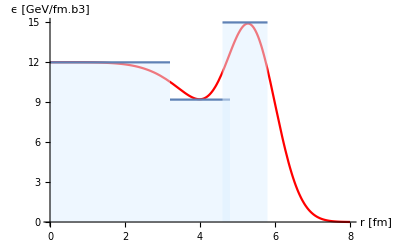

```mathematica
Show[{Plot[(12 Exp[-0.0004 r^5]+(34/(0.845 3.1415)) Exp[(-(r ^2)-(5.4^2)+2 r 5.4Cos[0])/0.845]),{r,0,8},PlotRange->All,PlotStyle->Red,AxesLabel->{"r [fm]","ϵ [GeV/fm.b3]"}, LabelStyle->{Black,Medium}],Plot[x=12,{x,0,3.2},Filling->Bottom,FillingStyle->Directive[Opacity[0.5],LightBlue]],Plot[x=9.2,{x,3.2,4.8},Filling->Bottom,FillingStyle->Directive[Opacity[0.5],LightBlue]],Plot[x=15,{x,4.6,5.8},Filling->Bottom,FillingStyle->Directive[Opacity[0.5],LightBlue]]}]
```

```mathematica
sketch1TubeModel=Show[
PolarPlot[5.2,{θ,0,2Pi},Frame->True,AxesStyle->Dashed,PlotStyle->Black,FrameLabel->{"X[fm]","Y[fm]"},PlotLabel->"E[GeV/fm^3]; τ=1 [fm]"],PolarPlot[3.4,{θ,-0.19,0.19},PlotStyle->Black],PolarPlot[5,{θ,-0.19,0.19},PlotStyle->Black],
FrameTicks->False,PlotRange->{{-7,7},{-7,7}},ImageSize->300
];
```

```mathematica
overlapedPlots=Legended[Show[{contourPlot1Tube,sketch1TubeModel}],bl];
```

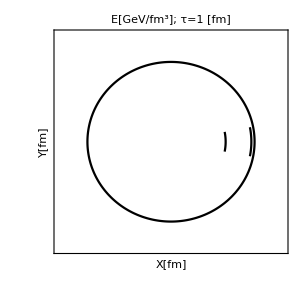
-Graphics--Graphics-

```mathematica
Row[{sketch1TubeModel,overlapedPlots}]
```

```mathematica
ColorBar["TemperatureMap"]
```

ColorBar[TemperatureMap]